# Epidemiological Model

Supplementary File for “Feedback between coevolution and epidemiology can help or hinder the maintenance of genetic variation in host-parasite models” 
Authors: MacPherson, Keeling, and Otto
Last Updated: November 15th, 2020

```mathematica
Clear["Global`*"]
```

## Deterministic Dynamics

Differential Equations

Symmetry and scaling assumption of transmission rates

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
```

Differential Equations

ds[h,t]/dt=f1[h,t]

```mathematica
f1[h_,t_]:=b(s[h,t]+Sum[i[h,l,t],{l,1,2}])(1-Sum[s[k,t]+Sum[i[k,l,t],{l,1,2}],{k,1,2}]/κ)-δ s[h,t]-Sum[β[h,p] s[h,t]Sum[i[k,p,t],{k,1,2}],{p,1,2}]+γ Sum[i[h,l,t],{l,1,2}]/.βSub
```

dsi[h,p,t]/dt=f2[h,p,t]

```mathematica
f2[h_,p_,t_]:=β[h,p]s[h,t]Sum[i[k,p,t],{k,1,2}]-(δ+α) i[h,p,t]-γ i[h,p,t]/.βSub
```

### Selection coefficients

```mathematica
σH=(f1[1,t]+f2[1,1,t]+f2[1,2,t])/(s[1,t]+i[1,1,t]+i[1,2,t])-(f1[2,t]+f2[2,1,t]+f2[2,2,t])/(s[2,t]+i[2,1,t]+i[2,2,t])//FullSimplify
```

-(α (i[1,1,t]+i[1,2,t]))/(i[1,1,t]+i[1,2,t]+s[1,t])+(α (i[2,1,t]+i[2,2,t]))/(i[2,1,t]+i[2,2,t]+s[2,t])

```mathematica
σP=Simplify[(f2[1,1,t]+f2[2,1,t])/(i[1,1,t]+i[2,1,t])-(f2[1,2,t]+f2[2,2,t])/(i[1,2,t]+i[2,2,t])]
```

((X-Y) (s[1,t]-s[2,t]))/κ

Transformation of Variables

```mathematica
DerivSub=Flatten[Join[Table[D[s[h,t],t]->f1[h,t],{h,1,2}],Table[D[i[h,p,t],t]->f2[h,p,t],{h,1,2},{p,1,2}]]];
```

```mathematica
VarTrans=Flatten[Solve[{nH[t]==Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}],nP[t]==Sum[i[h,p,t],{h,1,2},{p,1,2}],pH[t]==(s[1,t]+i[1,1,t]+i[1,2,t])/nH[t],pP[t]==(i[1,1,t]+i[2,1,t])/nP[t],ρH[t]==(i[1,1,t]+i[1,2,t])/nP[t],Δ[t]==i[1,1,t]-nP[t]ρH[t]pP[t]},Flatten[Join[Table[s[h,t],{h,1,2}],Table[i[h,p,t],{h,1,2},{p,1,2}]]]]];
```

```mathematica
g1[t_]:=D[Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}],t]/.DerivSub/.VarTrans//Simplify
```

```mathematica
g2[t_]:=D[Sum[i[h,p,t],{h,1,2},{p,1,2}],t]/.DerivSub/.VarTrans//Simplify
```

```mathematica
g3[t_]:=D[(s[1,t]+i[1,1,t]+i[1,2,t])/(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]),t]/.DerivSub/.VarTrans//Simplify
```

```mathematica
g4[t_]:=D[(i[1,1,t]+i[2,1,t])/Sum[i[h,p,t],{h,1,2},{p,1,2}],t]/.DerivSub/.VarTrans//Simplify
```

```mathematica
g5[t_]:=D[(i[1,1,t]+i[1,2,t])/Sum[i[h,p,t],{h,1,2},{p,1,2}],t]/.DerivSub/.VarTrans//Simplify
```

```mathematica
g6[t_]:=D[i[1,1,t]-((i[1,1,t]+i[1,2,t])(i[1,1,t]+i[2,1,t]))/Sum[i[h,p,t],{h,1,2},{p,1,2}],t]/.DerivSub/.VarTrans//FullSimplify
```

```mathematica
equListTrans={g1[t],g2[t],g3[t],g4[t],g5[t],g6[t]};
```

```mathematica
varsTrans={nH[t],nP[t],pH[t],pP[t],ρH[t],Δ[t]};
```

## Equilibria

```mathematica
equiSolTrans=Solve[equListTrans=={0,0,0,0,0,0},varsTrans]//Simplify;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
equiSolTrans//Length
```

13

Equilibria 1-3 are disease extinction

Equilibria 4,5,6,7,10,11,12,13 are fixation equilibria

Equilibria  8 and 9 however are endemic and polymorphic.

```mathematica
equiSolTrans[[8]]
```

{nH[t]→((b X+b Y-X α-Y α-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(2 b (X+Y)),nP[t]→((b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(2 b (X+Y)),pH[t]→1/2,pP[t]→1/2,ρH[t]→1/2,Δ[t]→((X-Y) (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(8 b (X+Y)^2)}

```mathematica
varsTrans
```

{nH[t],nP[t],pH[t],pP[t],ρH[t],Δ[t]}

```mathematica
gx[e_]:=ToExpression["g"<>ToString[e]<>"[t]"]
```

```mathematica
Table[{v1,v2},{v1,1,6},{v2,1,6}]//MatrixForm;
```

```mathematica
jMtrxTrans=Table[D[gx[v1],varsTrans[[v2]]],{v1,1,6},{v2,1,6}];
```

```mathematica
testPars={b->1,X->0.5,Y->0.2,α->0.1,δ->0.1,γ->0,κ->1};
```

```mathematica
equiSolTrans[[8]]/.testPars
```

{nH[t]→0.865986,nP[t]→0.294557,pH[t]→1/2,pP[t]→1/2,ρH[t]→1/2,Δ[t]→0.0315597}

```mathematica
esys=Simplify[jMtrxTrans/.equiSolTrans[[8]]]/.testPars//Eigensystem//Chop
```

{{-0.817542,-0.258161,-0.2,-0.117525,-0.0054601+0.0306298 ⅈ,-0.0054601-0.0306298 ⅈ},{{0.989633,-0.142805,0,0,0,-0.0153005},{0,0,0.11492,0.111123,0.98714,0},{0,0,0,0,0,1.},{-0.137843,0.984818,0,0,0,0.105516},{0,0,0.0861208+0.286423 ⅈ,0.847069,0.35787+0.254849 ⅈ,0},{0,0,0.0861208-0.286423 ⅈ,0.847069,0.35787-0.254849 ⅈ,0}}}

```mathematica
esys[[1]]
```

{-0.817542,-0.258161,-0.2,-0.117525,-0.0054601+0.0306298 ⅈ,-0.0054601-0.0306298 ⅈ}

```mathematica
esys[[2]]//MatrixForm
```

(0.989633 | -0.142805 | 0 | 0 | 0 | -0.0153005
0 | 0 | 0.11492 | 0.111123 | 0.98714 | 0
0 | 0 | 0 | 0 | 0 | 1.
-0.137843 | 0.984818 | 0 | 0 | 0 | 0.105516
0 | 0 | 0.0861208+0.286423 ⅈ | 0.847069 | 0.35787+0.254849 ⅈ | 0
0 | 0 | 0.0861208-0.286423 ⅈ | 0.847069 | 0.35787-0.254849 ⅈ | 0)

```mathematica
equiSolTrans[[8]]
```

{nH[t]→((b X+b Y-X α-Y α-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(2 b (X+Y)),nP[t]→((b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(2 b (X+Y)),pH[t]→1/2,pP[t]→1/2,ρH[t]→1/2,Δ[t]→((X-Y) (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√(X+Y) √(b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))) κ)/(8 b (X+Y)^2)}

```mathematica
equTemp={nH[t]->((b X+b Y-X α-Y α-X δ-Y δ+AA) κ)/(2 b (X+Y)),nP[t]->((b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+AA) κ)/(2 b (X+Y)),pH[t]->1/2,pP[t]->1/2,ρH[t]->1/2,Δ[t]->((X-Y) (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+AA) κ)/(8 b (X+Y)^2)};
```

```mathematica
CPTrans=Factor[CharacteristicPolynomial[jMtrxTrans/.equTemp,λ]]
```

((α+γ+δ+λ) (AA^2+AA b X+AA b Y-4 AA b α-AA X α-AA Y α-4 AA b γ-4 AA b δ-AA X δ-AA Y δ+4 AA b λ+AA X λ+b X^2 λ+AA Y λ+2 b X Y λ+b Y^2 λ-8 b X α λ-X^2 α λ-8 b Y α λ-2 X Y α λ-Y^2 α λ-4 b X γ λ-4 b Y γ λ-4 b X δ λ-X^2 δ λ-4 b Y δ λ-2 X Y δ λ-Y^2 δ λ+4 b X λ^2+4 b Y λ^2) (4 AA b X^2 α^3+4 b^2 X^3 α^3-8 AA b X Y α^3-4 b^2 X^2 Y α^3+4 AA b Y^2 α^3-4 b^2 X Y^2 α^3+4 b^2 Y^3 α^3-16 b^2 X^2 α^4-4 b X^3 α^4+32 b^2 X Y α^4+4 b X^2 Y α^4-16 b^2 Y^2 α^4+4 b X Y^2 α^4-4 b Y^3 α^4+8 AA b X^2 α^2 γ+8 b^2 X^3 α^2 γ-16 AA b X Y α^2 γ-8 b^2 X^2 Y α^2 γ+8 AA b Y^2 α^2 γ-8 b^2 X Y^2 α^2 γ+8 b^2 Y^3 α^2 γ-48 b^2 X^2 α^3 γ-8 b X^3 α^3 γ+96 b^2 X Y α^3 γ+8 b X^2 Y α^3 γ-48 b^2 Y^2 α^3 γ+8 b X Y^2 α^3 γ-8 b Y^3 α^3 γ+4 AA b X^2 α γ^2+4 b^2 X^3 α γ^2-8 AA b X Y α γ^2-4 b^2 X^2 Y α γ^2+4 AA b Y^2 α γ^2-4 b^2 X Y^2 α γ^2+4 b^2 Y^3 α γ^2-48 b^2 X^2 α^2 γ^2-4 b X^3 α^2 γ^2+96 b^2 X Y α^2 γ^2+4 b X^2 Y α^2 γ^2-48 b^2 Y^2 α^2 γ^2+4 b X Y^2 α^2 γ^2-4 b Y^3 α^2 γ^2-16 b^2 X^2 α γ^3+32 b^2 X Y α γ^3-16 b^2 Y^2 α γ^3+8 AA b X^2 α^2 δ+8 b^2 X^3 α^2 δ-16 AA b X Y α^2 δ-8 b^2 X^2 Y α^2 δ+8 AA b Y^2 α^2 δ-8 b^2 X Y^2 α^2 δ+8 b^2 Y^3 α^2 δ-48 b^2 X^2 α^3 δ-12 b X^3 α^3 δ+96 b^2 X Y α^3 δ+12 b X^2 Y α^3 δ-48 b^2 Y^2 α^3 δ+12 b X Y^2 α^3 δ-12 b Y^3 α^3 δ+8 AA b X^2 α γ δ+8 b^2 X^3 α γ δ-16 AA b X Y α γ δ-8 b^2 X^2 Y α γ δ+8 AA b Y^2 α γ δ-8 b^2 X Y^2 α γ δ+8 b^2 Y^3 α γ δ-96 b^2 X^2 α^2 γ δ-16 b X^3 α^2 γ δ+192 b^2 X Y α^2 γ δ+16 b X^2 Y α^2 γ δ-96 b^2 Y^2 α^2 γ δ+16 b X Y^2 α^2 γ δ-16 b Y^3 α^2 γ δ-48 b^2 X^2 α γ^2 δ-4 b X^3 α γ^2 δ+96 b^2 X Y α γ^2 δ+4 b X^2 Y α γ^2 δ-48 b^2 Y^2 α γ^2 δ+4 b X Y^2 α γ^2 δ-4 b Y^3 α γ^2 δ+4 AA b X^2 α δ^2+4 b^2 X^3 α δ^2-8 AA b X Y α δ^2-4 b^2 X^2 Y α δ^2+4 AA b Y^2 α δ^2-4 b^2 X Y^2 α δ^2+4 b^2 Y^3 α δ^2-48 b^2 X^2 α^2 δ^2-12 b X^3 α^2 δ^2+96 b^2 X Y α^2 δ^2+12 b X^2 Y α^2 δ^2-48 b^2 Y^2 α^2 δ^2+12 b X Y^2 α^2 δ^2-12 b Y^3 α^2 δ^2-48 b^2 X^2 α γ δ^2-8 b X^3 α γ δ^2+96 b^2 X Y α γ δ^2+8 b X^2 Y α γ δ^2-48 b^2 Y^2 α γ δ^2+8 b X Y^2 α γ δ^2-8 b Y^3 α γ δ^2-16 b^2 X^2 α δ^3-4 b X^3 α δ^3+32 b^2 X Y α δ^3+4 b X^2 Y α δ^3-16 b^2 Y^2 α δ^3+4 b X Y^2 α δ^3-4 b Y^3 α δ^3+AA^2 X^2 α λ+2 AA b X^3 α λ+b^2 X^4 α λ-2 AA^2 X Y α λ-2 AA b X^2 Y α λ+AA^2 Y^2 α λ-2 AA b X Y^2 α λ-2 b^2 X^2 Y^2 α λ+2 AA b Y^3 α λ+b^2 Y^4 α λ-4 AA b X^2 α^2 λ-2 AA X^3 α^2 λ-4 b^2 X^3 α^2 λ-2 b X^4 α^2 λ+8 AA b X Y α^2 λ+2 AA X^2 Y α^2 λ+4 b^2 X^2 Y α^2 λ-4 AA b Y^2 α^2 λ+2 AA X Y^2 α^2 λ+4 b^2 X Y^2 α^2 λ+4 b X^2 Y^2 α^2 λ-2 AA Y^3 α^2 λ-4 b^2 Y^3 α^2 λ-2 b Y^4 α^2 λ+4 b X^3 α^3 λ+X^4 α^3 λ-4 b X^2 Y α^3 λ-4 b X Y^2 α^3 λ-2 X^2 Y^2 α^3 λ+4 b Y^3 α^3 λ+Y^4 α^3 λ+AA^2 X^2 γ λ+2 AA b X^3 γ λ+b^2 X^4 γ λ-2 AA^2 X Y γ λ-2 AA b X^2 Y γ λ+AA^2 Y^2 γ λ-2 AA b X Y^2 γ λ-2 b^2 X^2 Y^2 γ λ+2 AA b Y^3 γ λ+b^2 Y^4 γ λ-8 AA b X^2 α γ λ-2 AA X^3 α γ λ-8 b^2 X^3 α γ λ-2 b X^4 α γ λ+16 AA b X Y α γ λ+2 AA X^2 Y α γ λ+8 b^2 X^2 Y α γ λ-8 AA b Y^2 α γ λ+2 AA X Y^2 α γ λ+8 b^2 X Y^2 α γ λ+4 b X^2 Y^2 α γ λ-2 AA Y^3 α γ λ-8 b^2 Y^3 α γ λ-2 b Y^4 α γ λ+8 b X^3 α^2 γ λ+X^4 α^2 γ λ-8 b X^2 Y α^2 γ λ-8 b X Y^2 α^2 γ λ-2 X^2 Y^2 α^2 γ λ+8 b Y^3 α^2 γ λ+Y^4 α^2 γ λ-4 AA b X^2 γ^2 λ-4 b^2 X^3 γ^2 λ+8 AA b X Y γ^2 λ+4 b^2 X^2 Y γ^2 λ-4 AA b Y^2 γ^2 λ+4 b^2 X Y^2 γ^2 λ-4 b^2 Y^3 γ^2 λ+4 b X^3 α γ^2 λ-4 b X^2 Y α γ^2 λ-4 b X Y^2 α γ^2 λ+4 b Y^3 α γ^2 λ+AA^2 X^2 δ λ+2 AA b X^3 δ λ+b^2 X^4 δ λ-2 AA^2 X Y δ λ-2 AA b X^2 Y δ λ+AA^2 Y^2 δ λ-2 AA b X Y^2 δ λ-2 b^2 X^2 Y^2 δ λ+2 AA b Y^3 δ λ+b^2 Y^4 δ λ-8 AA b X^2 α δ λ-4 AA X^3 α δ λ-8 b^2 X^3 α δ λ-4 b X^4 α δ λ+16 AA b X Y α δ λ+4 AA X^2 Y α δ λ+8 b^2 X^2 Y α δ λ-8 AA b Y^2 α δ λ+4 AA X Y^2 α δ λ+8 b^2 X Y^2 α δ λ+8 b X^2 Y^2 α δ λ-4 AA Y^3 α δ λ-8 b^2 Y^3 α δ λ-4 b Y^4 α δ λ+12 b X^3 α^2 δ λ+3 X^4 α^2 δ λ-12 b X^2 Y α^2 δ λ-12 b X Y^2 α^2 δ λ-6 X^2 Y^2 α^2 δ λ+12 b Y^3 α^2 δ λ+3 Y^4 α^2 δ λ-8 AA b X^2 γ δ λ-2 AA X^3 γ δ λ-8 b^2 X^3 γ δ λ-2 b X^4 γ δ λ+16 AA b X Y γ δ λ+2 AA X^2 Y γ δ λ+8 b^2 X^2 Y γ δ λ-8 AA b Y^2 γ δ λ+2 AA X Y^2 γ δ λ+8 b^2 X Y^2 γ δ λ+4 b X^2 Y^2 γ δ λ-2 AA Y^3 γ δ λ-8 b^2 Y^3 γ δ λ-2 b Y^4 γ δ λ+16 b X^3 α γ δ λ+2 X^4 α γ δ λ-16 b X^2 Y α γ δ λ-16 b X Y^2 α γ δ λ-4 X^2 Y^2 α γ δ λ+16 b Y^3 α γ δ λ+2 Y^4 α γ δ λ+4 b X^3 γ^2 δ λ-4 b X^2 Y γ^2 δ λ-4 b X Y^2 γ^2 δ λ+4 b Y^3 γ^2 δ λ-4 AA b X^2 δ^2 λ-2 AA X^3 δ^2 λ-4 b^2 X^3 δ^2 λ-2 b X^4 δ^2 λ+8 AA b X Y δ^2 λ+2 AA X^2 Y δ^2 λ+4 b^2 X^2 Y δ^2 λ-4 AA b Y^2 δ^2 λ+2 AA X Y^2 δ^2 λ+4 b^2 X Y^2 δ^2 λ+4 b X^2 Y^2 δ^2 λ-2 AA Y^3 δ^2 λ-4 b^2 Y^3 δ^2 λ-2 b Y^4 δ^2 λ+12 b X^3 α δ^2 λ+3 X^4 α δ^2 λ-12 b X^2 Y α δ^2 λ-12 b X Y^2 α δ^2 λ-6 X^2 Y^2 α δ^2 λ+12 b Y^3 α δ^2 λ+3 Y^4 α δ^2 λ+8 b X^3 γ δ^2 λ+X^4 γ δ^2 λ-8 b X^2 Y γ δ^2 λ-8 b X Y^2 γ δ^2 λ-2 X^2 Y^2 γ δ^2 λ+8 b Y^3 γ δ^2 λ+Y^4 γ δ^2 λ+4 b X^3 δ^3 λ+X^4 δ^3 λ-4 b X^2 Y δ^3 λ-4 b X Y^2 δ^3 λ-2 X^2 Y^2 δ^3 λ+4 b Y^3 δ^3 λ+Y^4 δ^3 λ+AA^2 X^2 λ^2+2 AA b X^3 λ^2+b^2 X^4 λ^2+2 AA^2 X Y λ^2+6 AA b X^2 Y λ^2+4 b^2 X^3 Y λ^2+AA^2 Y^2 λ^2+6 AA b X Y^2 λ^2+6 b^2 X^2 Y^2 λ^2+2 AA b Y^3 λ^2+4 b^2 X Y^3 λ^2+b^2 Y^4 λ^2-4 AA b X^2 α λ^2-2 AA X^3 α λ^2-4 b^2 X^3 α λ^2-2 b X^4 α λ^2-8 AA b X Y α λ^2-6 AA X^2 Y α λ^2-12 b^2 X^2 Y α λ^2-8 b X^3 Y α λ^2-4 AA b Y^2 α λ^2-6 AA X Y^2 α λ^2-12 b^2 X Y^2 α λ^2-12 b X^2 Y^2 α λ^2-2 AA Y^3 α λ^2-4 b^2 Y^3 α λ^2-8 b X Y^3 α λ^2-2 b Y^4 α λ^2+16 b^2 X^2 α^2 λ^2+4 b X^3 α^2 λ^2+X^4 α^2 λ^2+32 b^2 X Y α^2 λ^2+12 b X^2 Y α^2 λ^2+4 X^3 Y α^2 λ^2+16 b^2 Y^2 α^2 λ^2+12 b X Y^2 α^2 λ^2+6 X^2 Y^2 α^2 λ^2+4 b Y^3 α^2 λ^2+4 X Y^3 α^2 λ^2+Y^4 α^2 λ^2+16 b^2 X^2 α γ λ^2+32 b^2 X Y α γ λ^2+16 b^2 Y^2 α γ λ^2-2 AA X^3 δ λ^2-2 b X^4 δ λ^2-6 AA X^2 Y δ λ^2-8 b X^3 Y δ λ^2-6 AA X Y^2 δ λ^2-12 b X^2 Y^2 δ λ^2-2 AA Y^3 δ λ^2-8 b X Y^3 δ λ^2-2 b Y^4 δ λ^2+16 b^2 X^2 α δ λ^2+4 b X^3 α δ λ^2+2 X^4 α δ λ^2+32 b^2 X Y α δ λ^2+12 b X^2 Y α δ λ^2+8 X^3 Y α δ λ^2+16 b^2 Y^2 α δ λ^2+12 b X Y^2 α δ λ^2+12 X^2 Y^2 α δ λ^2+4 b Y^3 α δ λ^2+8 X Y^3 α δ λ^2+2 Y^4 α δ λ^2+X^4 δ^2 λ^2+4 X^3 Y δ^2 λ^2+6 X^2 Y^2 δ^2 λ^2+4 X Y^3 δ^2 λ^2+Y^4 δ^2 λ^2+4 AA b X^2 λ^3+4 b^2 X^3 λ^3+8 AA b X Y λ^3+12 b^2 X^2 Y λ^3+4 AA b Y^2 λ^3+12 b^2 X Y^2 λ^3+4 b^2 Y^3 λ^3-4 b X^3 α λ^3-12 b X^2 Y α λ^3-12 b X Y^2 α λ^3-4 b Y^3 α λ^3-4 b X^3 δ λ^3-12 b X^2 Y δ λ^3-12 b X Y^2 δ λ^3-4 b Y^3 δ λ^3))/(16 b^2 (X+Y)^3 (AA+b X+b Y-X α-Y α-X δ-Y δ))

```mathematica
Collect[CPTrans[[6]],λ]
```

AA^2+AA b X+AA b Y-4 AA b α-AA X α-AA Y α-4 AA b γ-4 AA b δ-AA X δ-AA Y δ+(4 AA b+AA X+b X^2+AA Y+2 b X Y+b Y^2-8 b X α-X^2 α-8 b Y α-2 X Y α-Y^2 α-4 b X γ-4 b Y γ-4 b X δ-X^2 δ-4 b Y δ-2 X Y δ-Y^2 δ) λ+(4 b X+4 b Y) λ^2

```mathematica
Collect[CPTrans[[7]],λ,Simplify]
```

-4 b (X-Y)^2 α (α+γ+δ)^2 (-AA+(X+Y) (α+δ)-b (X+Y-4 (α+γ+δ)))+(X-Y)^2 (AA+(X+Y) (b-α-δ)) (α+γ+δ) (AA-(X+Y) (α+δ)+b (X+Y-4 (α+γ+δ))) λ+(X+Y)^2 (AA^2-2 b (X+Y) (X+Y-2 α) (α+δ)+(X+Y)^2 (α+δ)^2+2 AA (b (X+Y-2 α)-(X+Y) (α+δ))+b^2 (X^2+Y^2+2 X (Y-2 α)-4 Y α+16 α (α+γ+δ))) λ^2+4 b (X+Y)^2 (AA+(X+Y) (b-α-δ)) λ^3

Equilibria

### The list of differential equations and variables

```mathematica
equList=Join[Table[f1[h,t],{h,1,2}],Table[f2[h,p,t],{h,1,2},{p,1,2}]]//Flatten;
```

```mathematica
vars=Join[Table[s[h,t],{h,1,2}],Table[i[h,p,t],{h,1,2},{p,1,2}]]//Flatten;
```

### Jacobian Matrix

```mathematica
jMtrx=Join[Table[{D[f1[h1,t],s[1,t]],D[f1[h1,t],s[2,t]],D[f1[h1,t],i[1,1,t]],D[f1[h1,t],i[1,2,t]],D[f1[h1,t],i[2,1,t]],D[f1[h1,t],i[2,2,t]]},{h1,1,2}],Flatten[Table[{D[f2[h1,p1,t],s[1,t]],D[f2[h1,p1,t],s[2,t]],D[f2[h1,p1,t],i[1,1,t]],D[f2[h1,p1,t],i[1,2,t]],D[f2[h1,p1,t],i[2,1,t]],D[f2[h1,p1,t],i[2,2,t]]},{h1,1,2},{p1,1,2}],1]]//Simplify;
```

## Extinction equilibrium

```mathematica
equList/.{s[1,t]->0,s[2,t]->0,i[1,1,t]->0,i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0}
```

{0,0,0,0,0,0}

```mathematica
jMtrx/.{s[1,t]->0,s[2,t]->0,i[1,1,t]->0,i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0}//Eigenvalues
```

{b-δ,b-δ,-α-γ-δ,-α-γ-δ,-α-γ-δ,-α-γ-δ}

## Disease Extinction equilibrium

```mathematica
assump={(*s[1,t]->0,s[2,t]->0,*)i[1,1,t]->0,i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0};
```

```mathematica
temp=equList/.{(*s[1,t]->0,s[2,t]->0,*)i[1,1,t]->0,i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0}
```

{-δ s[1,t]+b s[1,t] (1-(s[1,t]+s[2,t])/κ),-δ s[2,t]+b s[2,t] (1-(s[1,t]+s[2,t])/κ),0,0,0,0}

```mathematica
equilSol=Solve[temp[[{1,2}]]=={0,0},{s[1,t],s[2,t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s[2,t]→((b-δ) κ)/b-s[1,t]},{s[1,t]→0,s[2,t]→0}}

### Stability

```mathematica
λs=Eigenvalues[jMtrx/.assump]//Simplify
```

{-α-γ-δ,-α-γ-δ,(b κ-δ κ-2 b s[1,t]-2 b s[2,t])/κ,(b κ-δ κ-b s[1,t]-b s[2,t])/κ,(-(α+γ+δ) κ+Y s[1,t]+X s[2,t])/κ,(-(α+γ+δ) κ+X s[1,t]+Y s[2,t])/κ}

#### Eigenvalue 3: Escape from extinction

For eigenvalue 3 this reduces to:

```mathematica
(b κ-δ κ)/κ-2 b (((b-δ) κ)/b)/κ//Simplify
```

-b+δ

#### Eigenvalue 4: Equilibrium “manifold”

For eigenvalue 4 this reduces to:

```mathematica
(b κ-δ κ-b(((b-δ) κ)/b))/κ//Simplify
```

0

#### Eigenvalue 5 and 6: R0

For eigenvalue 5

Let φ be the proportion of the population that is host type 1.

```mathematica
temp=λs[[5]]/.{s[1,t]->ψ (((b-δ) κ)/b),s[2,t]->(1-ψ) (((b-δ) κ)/b)}//FullSimplify
```

(δ (X (-1+ψ)-Y ψ)-b (α+γ+δ+X (-1+ψ)-Y ψ))/b

```mathematica
Reduce[{temp<0,0<δ<b,0<Y<X,0<κ,0<α,0<γ,0<ψ<1},X,FullSimplify]
```

Reduce::bdomv: Warning: FullSimplify is not a valid domain specification. Assuming it is a variable to eliminate.

κ>0&&δ>0&&γ>0&&α>0&&b>δ&&0<Y<(b α+b γ+b δ)/(b-δ)&&0<ψ<1&&Y<X<(-b α-b γ-b δ+b Y ψ-Y δ ψ)/(-b+δ+b ψ-δ ψ)

Looking at the condition: X<(-b α-b γ-b δ+b Y ψ-Y δ ψ)/(-b+δ+b ψ-δ ψ)

```mathematica
Collect[(-b α-b γ-b δ+b Y ψ-Y δ ψ)/(-b+δ+b ψ-δ ψ),Y,Simplify]
```

-(b (α+γ+δ))/((b-δ) (-1+ψ))+(Y ψ)/(-1+ψ)

Hence this condition can be rewritten as:

```mathematica
(1-ψ)X+ψ Y<(b (α+γ+δ))/(b-δ)=(κ(α+ γ+ δ))/sEqu
```

Set::write: Tag Less in X (1-ψ)+Y ψ<(b (α+γ+δ))/(b-δ) is Protected.

((α+γ+δ) κ)/sEqu

For eigenvalue 6

```mathematica
temp=λs[[6]]/.{s[1,t]->ψ (((b-δ) κ)/b),s[2,t]->(1-ψ) (((b-δ) κ)/b)}//FullSimplify
```

(δ (Y (-1+ψ)-X ψ)-b (α+γ+δ+Y (-1+ψ)-X ψ))/b

```mathematica
Reduce[{temp<0,0<δ<b,0<Y<X,0<κ,0<α,0<γ,0<ψ<1},X,FullSimplify]
```

Reduce::bdomv: Warning: FullSimplify is not a valid domain specification. Assuming it is a variable to eliminate.

κ>0&&δ>0&&γ>0&&α>0&&b>δ&&0<Y<(b α+b γ+b δ)/(b-δ)&&0<ψ<1&&Y<X<(-b Y+b α+b γ+b δ+Y δ+b Y ψ-Y δ ψ)/(b ψ-δ ψ)

```mathematica
Collect[(-b Y+b α+b γ+b δ+Y δ+b Y ψ-Y δ ψ)/(b ψ-δ ψ),Y,Simplify]
```

(b (α+γ+δ))/((b-δ) ψ)+(Y (-1+ψ))/ψ

Hence this condition can be rewritten as:

```mathematica
ψ X+(1-ψ) Y<(b (α+γ+δ))/(b-δ)=(κ(α+ γ+ δ))/sEqu
```

Set::write: Tag Less in Y (1-ψ)+X ψ<(b (α+γ+δ))/(b-δ) is Protected.

((α+γ+δ) κ)/sEqu

## Single Host Single Pathogen (Matching)

### Solving for equilibrium

```mathematica
assump={(*s[1,t]->0,*)s[2,t]->0,(*i[1,1,t]->0,*)i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0};
```

```mathematica
temp=equList/.{(*s[1,t]->0,*)s[2,t]->0,(*i[1,1,t]->0,*)i[1,2,t]->0,i[2,1,t]->0,i[2,2,t]->0}
```

{γ i[1,1,t]-δ s[1,t]-(X i[1,1,t] s[1,t])/κ+b (i[1,1,t]+s[1,t]) (1-(i[1,1,t]+s[1,t])/κ),0,-γ i[1,1,t]-(α+δ) i[1,1,t]+(X i[1,1,t] s[1,t])/κ,0,0,0}

```mathematica
s1sol=Flatten[Solve[temp[[3]]==0,s[1,t]]]
```

{s[1,t]→((α+γ+δ) κ)/X}

```mathematica
Factor[temp/.s1sol][[1]]
```

-1/(X^2 κ)(-b X α κ^2+b α^2 κ^2-b X γ κ^2+2 b α γ κ^2+b γ^2 κ^2-b X δ κ^2+2 b α δ κ^2+X α δ κ^2+2 b γ δ κ^2+X γ δ κ^2+b δ^2 κ^2+X δ^2 κ^2-b X^2 κ i[1,1,t]+2 b X α κ i[1,1,t]+X^2 α κ i[1,1,t]+2 b X γ κ i[1,1,t]+2 b X δ κ i[1,1,t]+X^2 δ κ i[1,1,t]+b X^2 i[1,1,t]^2)

This is a square in i[1,1,t].  Solving for a variable may be useful instead

```mathematica
bSol=Flatten[FullSimplify[Solve[Factor[temp/.s1sol][[1]]==0,b]]]
```

{b→-(X κ (δ (α+γ+δ) κ+X (α+δ) i[1,1,t]))/(((α+γ+δ) κ+X i[1,1,t]) ((-X+α+γ+δ) κ+X i[1,1,t]))}

```mathematica
i11sol=FullSimplify[Solve[Factor[temp/.s1sol][[1]]==0,i[1,1,t]],Assumptions->{0<Y<X,0<δ<b,0<α,0<γ,0<κ}]
```

{{i[1,1,t]→1/(2 b X)(-X (α+δ)+b (X-2 (α+γ+δ))+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))) κ},{i[1,1,t]→-1/(2 b X)(X (-b+α+δ)+2 b (α+γ+δ)+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))) κ}}

```mathematica
equ1=Join[s1sol/.i11sol[[1]],i11sol[[1]],assump]
```

{s[1,t]→((α+γ+δ) κ)/X,i[1,1,t]→1/(2 b X)(-X (α+δ)+b (X-2 (α+γ+δ))+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))) κ,s[2,t]→0,i[1,2,t]→0,i[2,1,t]→0,i[2,2,t]→0}

```mathematica
equ2=Join[s1sol/.i11sol[[1]],i11sol[[1]],assump]
```

{s[1,t]→((α+γ+δ) κ)/X,i[1,1,t]→1/(2 b X)(-X (α+δ)+b (X-2 (α+γ+δ))+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))) κ,s[2,t]→0,i[1,2,t]→0,i[2,1,t]→0,i[2,2,t]→0}

### Biological Validity

```mathematica
Reduce[{0<(i[1,1,t]/.i11sol[[1]]),0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//FullSimplify
```

δ>0&&α>0&&b>δ&&γ>0&&X>(b (α+γ+δ))/(b-δ)&&0<Y<X&&κ>0

```mathematica
Reduce[{0<(i[1,1,t]/.i11sol[[2]]),0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//Simplify
```

False

### Stability

```mathematica
jMtrx[[{1,4},{1,4}]]/.{s[2,t]->0,i[1,1,t]->0,i[2,1,t]->0,i[2,2,t]->0}
```

{{-(-b κ+δ κ+(2 b+Y) i[1,2,t]+2 b s[1,t])/κ,-(-b κ-γ κ+2 b i[1,2,t]+2 b s[1,t]+Y s[1,t])/κ},{(Y i[1,2,t])/κ,(-(α+γ+δ) κ+Y s[1,t])/κ}}

```mathematica
equilibraMM={s[1,t]->((α+γ+δ) κ)/Y,i[1,1,t]->1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ}
```

{s[1,t]→((α+γ+δ) κ)/Y,i[1,1,t]→1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ}

```mathematica
jMtrx[[{1,3},{1,3}]]
```

{{-1/κ(-b κ+δ κ+(2 b+X) i[1,1,t]+(2 b+Y) i[1,2,t]+b i[2,1,t]+X i[2,1,t]+b i[2,2,t]+Y i[2,2,t]+2 b s[1,t]+b s[2,t]),-1/κ(-b κ-γ κ+2 b i[1,1,t]+2 b i[1,2,t]+b i[2,1,t]+b i[2,2,t]+2 b s[1,t]+X s[1,t]+b s[2,t])},{(X (i[1,1,t]+i[2,1,t]))/κ,(-(α+γ+δ) κ+X s[1,t])/κ}}

```mathematica
temp=jMtrx/.assump/.s1sol/.bSol//Simplify;
```

```mathematica
jmtrxInteral=jMtrx[[{1,3},{1,3}]]/.equ1//Simplify
```

{{1/2 (2 b-2 δ-(4 b (α+γ+δ))/X-1/(b X)(2 b+X) (-X (α+δ)+b (X-2 (α+γ+δ))+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))),-(√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))/X},{1/(2 b)(-X (α+δ)+b (X-2 (α+γ+δ))+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))),0}}

```mathematica
Simplify[jmtrxInteral//Eigenvalues]/.{b->1,X->6,δ->0.5,α->1.5,γ->0.1}
```

{-0.221363-0.521077 ⅈ,-0.221363+0.521077 ⅈ}

```mathematica
Simplify[jmtrxInteral//Eigenvalues]/.{b->1,X->7,δ->0.5,α->1.5,γ->0.1}
```

{-0.21497-0.619028 ⅈ,-0.21497+0.619028 ⅈ}

```mathematica
Simplify[jmtrxInteral//Eigenvectors]/.{b->1,X->7,Y->3.5,δ->0.05,α->0.1,γ->0.1}
```

{{-0.979394,1},{-0.152973,1}}

```mathematica
Collect[CharacteristicPolynomial[jmtrxInteral,λ],λ,Simplify]
```

1/(2 b X)(b^2 X^2+X (α+δ) (X (α+δ)-√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))+b (-2 X^2 (α+δ)-2 (α+γ+δ) √(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ))))+X (4 α^2+4 α (γ+δ)+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))))+1/(2 b X)(X (-X (α+δ)+√(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))+b (X^2-2 X (2 α+γ+δ)+2 √(X (b^2 X+X (α+δ)^2+b (-2 X (α+δ)+4 α (α+γ+δ)))))) λ+λ^2

```mathematica
CP=CharacteristicPolynomial[temp,λ];
```

```mathematica
crit=Numerator[Factor[CP/.λ->0]]
```

-(X-Y)^2 α (α+γ+δ)^3 i[1,1,t]^2 (X α^2 κ^2-α^3 κ^2+X α γ κ^2-2 α^2 γ κ^2-α γ^2 κ^2+X α δ κ^2-α^2 δ κ^2+γ^2 δ κ^2+α δ^2 κ^2+2 γ δ^2 κ^2+δ^3 κ^2+2 X α δ κ i[1,1,t]+2 X γ δ κ i[1,1,t]+2 X δ^2 κ i[1,1,t]+X^2 α i[1,1,t]^2+X^2 δ i[1,1,t]^2)

```mathematica
Reduce[{(crit[[5]]/.i11sol[[1]])>0,0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//FullSimplify
```

(X<(b (α+γ+δ))/(b-δ)||X>(b (α+γ+δ))/(b-δ))&&0<Y<X&&b>δ&&α>0&&γ>0&&δ>0&&κ>0

```mathematica
temp2=Numerator[Factor[CP]]
```

-(α+γ+δ+λ) (X α-Y α+X γ-Y γ+X δ-Y δ+X λ) (-α^2 κ^2 λ-2 α γ κ^2 λ-γ^2 κ^2 λ-2 α δ κ^2 λ-2 γ δ κ^2 λ-δ^2 κ^2 λ-α κ^2 λ^2-γ κ^2 λ^2-δ κ^2 λ^2+X α^2 κ i[1,1,t]-Y α^2 κ i[1,1,t]+X α γ κ i[1,1,t]-Y α γ κ i[1,1,t]+X α δ κ i[1,1,t]-Y α δ κ i[1,1,t]-Y α κ λ i[1,1,t]-X γ κ λ i[1,1,t]-Y γ κ λ i[1,1,t]-X δ κ λ i[1,1,t]-Y δ κ λ i[1,1,t]-X κ λ^2 i[1,1,t]-X Y λ i[1,1,t]^2) (α^2 δ κ^3 λ+2 α γ δ κ^3 λ+γ^2 δ κ^3 λ+2 α δ^2 κ^3 λ+2 γ δ^2 κ^3 λ+δ^3 κ^3 λ+X α κ^3 λ^2-α^2 κ^3 λ^2+X γ κ^3 λ^2-2 α γ κ^3 λ^2-γ^2 κ^3 λ^2+X δ κ^3 λ^2-2 α δ κ^3 λ^2-2 γ δ κ^3 λ^2-δ^2 κ^3 λ^2+X^2 α^2 κ^2 i[1,1,t]-X α^3 κ^2 i[1,1,t]+X^2 α γ κ^2 i[1,1,t]-2 X α^2 γ κ^2 i[1,1,t]-X α γ^2 κ^2 i[1,1,t]+X^2 α δ κ^2 i[1,1,t]-X α^2 δ κ^2 i[1,1,t]+X γ^2 δ κ^2 i[1,1,t]+X α δ^2 κ^2 i[1,1,t]+2 X γ δ^2 κ^2 i[1,1,t]+X δ^3 κ^2 i[1,1,t]+X α^2 κ^2 λ i[1,1,t]+X^2 γ κ^2 λ i[1,1,t]-X γ^2 κ^2 λ i[1,1,t]+X^2 δ κ^2 λ i[1,1,t]+2 X α δ κ^2 λ i[1,1,t]+X δ^2 κ^2 λ i[1,1,t]+X^2 κ^2 λ^2 i[1,1,t]-2 X α κ^2 λ^2 i[1,1,t]-2 X γ κ^2 λ^2 i[1,1,t]-2 X δ κ^2 λ^2 i[1,1,t]+2 X^2 α δ κ i[1,1,t]^2+2 X^2 γ δ κ i[1,1,t]^2+2 X^2 δ^2 κ i[1,1,t]^2+X^3 κ λ i[1,1,t]^2-2 X^2 γ κ λ i[1,1,t]^2-X^2 δ κ λ i[1,1,t]^2-X^2 κ λ^2 i[1,1,t]^2+X^3 α i[1,1,t]^3+X^3 δ i[1,1,t]^3-X^3 λ i[1,1,t]^3)

```mathematica
Solve[temp2[[3]]==0,λ]//Simplify
```

{{λ→-((X-Y) (α+γ+δ))/X}}

```mathematica
temp3=Solve[temp2[[4]]==0,λ]//Simplify
```

{{λ→-1/(2 κ ((α+γ+δ) κ+X i[1,1,t]))(α^2 κ^2+2 α γ κ^2+γ^2 κ^2+2 α δ κ^2+2 γ δ κ^2+δ^2 κ^2+Y α κ i[1,1,t]+X γ κ i[1,1,t]+Y γ κ i[1,1,t]+X δ κ i[1,1,t]+Y δ κ i[1,1,t]+X Y i[1,1,t]^2-√(4 (X-Y) α (α+γ+δ) κ^2 i[1,1,t] ((α+γ+δ) κ+X i[1,1,t])+((α+γ+δ)^2 κ^2+(X (γ+δ)+Y (α+γ+δ)) κ i[1,1,t]+X Y i[1,1,t]^2)^2))},{λ→-1/(2 κ ((α+γ+δ) κ+X i[1,1,t]))(α^2 κ^2+2 α γ κ^2+γ^2 κ^2+2 α δ κ^2+2 γ δ κ^2+δ^2 κ^2+Y α κ i[1,1,t]+X γ κ i[1,1,t]+Y γ κ i[1,1,t]+X δ κ i[1,1,t]+Y δ κ i[1,1,t]+X Y i[1,1,t]^2+√(4 (X-Y) α (α+γ+δ) κ^2 i[1,1,t] ((α+γ+δ) κ+X i[1,1,t])+((α+γ+δ)^2 κ^2+(X (γ+δ)+Y (α+γ+δ)) κ i[1,1,t]+X Y i[1,1,t]^2)^2))}}

```mathematica
Reduce[{(λ/.temp3[[1]])<0,0<Y<X,0<δ<b,0<α,0<γ,0<κ,0<i[1,1,t]}]
```

False

```mathematica
Reduce[{(λ/.temp3[[2]])<0,0<Y<X,0<δ<b,0<α,0<γ,0<κ,0<i[1,1,t]}]
```

δ>0&&γ>0&&α>0&&i[1,1,t]>0&&κ>0&&X>0&&0<Y<X&&b>δ

## Single Host Single Pathogen (Mismatching)

### Solving for equilibrium

```mathematica
assump={(*s[1,t]->0,*)s[2,t]->0,i[1,1,t]->0,(*i[1,2,t]->0,*)i[2,1,t]->0,i[2,2,t]->0};
```

```mathematica
temp=equList/.assump
```

{γ i[1,2,t]-δ s[1,t]-(Y i[1,2,t] s[1,t])/κ+b (i[1,2,t]+s[1,t]) (1-(i[1,2,t]+s[1,t])/κ),0,0,-γ i[1,2,t]-(α+δ) i[1,2,t]+(Y i[1,2,t] s[1,t])/κ,0,0}

```mathematica
s1sol=Flatten[Solve[temp[[4]]==0,s[1,t]]]
```

{s[1,t]→((α+γ+δ) κ)/Y}

```mathematica
Factor[temp/.s1sol][[1]]
```

-1/(Y^2 κ)(-b Y α κ^2+b α^2 κ^2-b Y γ κ^2+2 b α γ κ^2+b γ^2 κ^2-b Y δ κ^2+2 b α δ κ^2+Y α δ κ^2+2 b γ δ κ^2+Y γ δ κ^2+b δ^2 κ^2+Y δ^2 κ^2-b Y^2 κ i[1,2,t]+2 b Y α κ i[1,2,t]+Y^2 α κ i[1,2,t]+2 b Y γ κ i[1,2,t]+2 b Y δ κ i[1,2,t]+Y^2 δ κ i[1,2,t]+b Y^2 i[1,2,t]^2)

This is a square in i[1,1,t].  Solving for a variable may be useful instead

```mathematica
bSol=Flatten[FullSimplify[Solve[Factor[temp/.s1sol][[1]]==0,b]]]
```

{b→-(Y κ (δ (α+γ+δ) κ+Y (α+δ) i[1,2,t]))/(((α+γ+δ) κ+Y i[1,2,t]) ((-Y+α+γ+δ) κ+Y i[1,2,t]))}

```mathematica
i12sol=FullSimplify[Solve[Factor[temp/.s1sol][[1]]==0,i[1,2,t]],Assumptions->{0<Y<X,0<δ<b,0<α,0<γ,0<κ}]
```

{{i[1,2,t]→1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ},{i[1,2,t]→-1/(2 b Y)(Y (-b+α+δ)+2 b (α+γ+δ)+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ}}

```mathematica
equ1=Join[s1sol/.i12sol[[1]],i12sol[[1]],assump]
```

{s[1,t]→((α+γ+δ) κ)/Y,i[1,2,t]→1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ,s[2,t]→0,i[1,1,t]→0,i[2,1,t]→0,i[2,2,t]→0}

```mathematica
equ2=Join[s1sol/.i12sol[[1]],i12sol[[1]],assump]
```

{s[1,t]→((α+γ+δ) κ)/Y,i[1,2,t]→1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ,s[2,t]→0,i[1,1,t]→0,i[2,1,t]→0,i[2,2,t]→0}

### Biological Validity

```mathematica
Reduce[{0<(i[1,2,t]/.i12sol[[1]]),0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//FullSimplify
```

δ>0&&α>0&&b>δ&&γ>0&&Y>(b (α+γ+δ))/(b-δ)&&X>Y&&κ>0

```mathematica
Reduce[{0<(i[1,2,t]/.i12sol[[2]]),0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//Simplify
```

False

### Stability

```mathematica
jMtrx[[{1,4},{1,4}]]/.{s[2,t]->0,i[1,1,t]->0,i[2,1,t]->0,i[2,2,t]->0}
```

{{-(-b κ+δ κ+(2 b+Y) i[1,2,t]+2 b s[1,t])/κ,-(-b κ-γ κ+2 b i[1,2,t]+2 b s[1,t]+Y s[1,t])/κ},{(Y i[1,2,t])/κ,(-(α+γ+δ) κ+Y s[1,t])/κ}}

```mathematica
equilibraMM={s[1,t]->((α+γ+δ) κ)/Y,i[1,1,t]->1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ}
```

{s[1,t]→((α+γ+δ) κ)/Y,i[1,1,t]→1/(2 b Y)(-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))) κ}

```mathematica
jMtrx[[{1,3},{1,3}]]
```

{{-1/κ(-b κ+δ κ+(2 b+X) i[1,1,t]+(2 b+Y) i[1,2,t]+b i[2,1,t]+X i[2,1,t]+b i[2,2,t]+Y i[2,2,t]+2 b s[1,t]+b s[2,t]),-1/κ(-b κ-γ κ+2 b i[1,1,t]+2 b i[1,2,t]+b i[2,1,t]+b i[2,2,t]+2 b s[1,t]+X s[1,t]+b s[2,t])},{(X (i[1,1,t]+i[2,1,t]))/κ,(-(α+γ+δ) κ+X s[1,t])/κ}}

```mathematica
temp=jMtrx/.assump/.s1sol/.bSol//Simplify;
```

```mathematica
jmtrxInteral=jMtrx[[{1,3},{1,3}]]/.equ1//Simplify
```

{{1/2 (2 b-2 δ-(4 b (α+γ+δ))/Y-1/(b Y)(2 b+Y) (-Y (α+δ)+b (Y-2 (α+γ+δ))+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ)))))),1/Y(Y α+Y γ+Y δ-X (α+γ+δ)-√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ)))))},{0,((X-Y) (α+γ+δ))/Y}}

```mathematica
Simplify[jmtrxInteral//Eigenvalues]/.{b->1,X->6,δ->0.5,α->1.5,γ->0.1}
```

{(2.1 (6-Y))/Y,(7.2 Y-Y^2-2 √(Y (12.6+1. Y))+Y (2. Y-√(Y (12.6+1. Y))))/(2 Y)}

```mathematica
Simplify[jmtrxInteral//Eigenvalues]/.{b->1,X->7,δ->0.5,α->1.5,γ->0.1}
```

{(2.1 (7-Y))/Y,(7.2 Y-Y^2-2 √(Y (12.6+1. Y))+Y (2. Y-√(Y (12.6+1. Y))))/(2 Y)}

```mathematica
Simplify[jmtrxInteral//Eigenvectors]/.{b->1,X->7,Y->3.5,δ->0.05,α->0.1,γ->0.1}
```

{{-0.296131,1},{1,0}}

```mathematica
Collect[CharacteristicPolynomial[jmtrxInteral,λ],λ,Simplify]
```

1/(2 b Y^2)(X-Y) (α+γ+δ) (Y (Y (α+δ)-√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ)))))-b (Y^2-2 Y (2 α+γ+δ)+2 √(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ))))))+1/(2 b Y)(Y (-Y (α+δ)+√(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ)))))+b (Y^2-2 X α-2 Y α-2 X γ-2 X δ+2 √(Y (b^2 Y+Y (α+δ)^2+b (-2 Y (α+δ)+4 α (α+γ+δ)))))) λ+λ^2

```mathematica
CP=CharacteristicPolynomial[temp,λ];
```

```mathematica
crit=Numerator[Factor[CP/.λ->0]]
```

-(-X+Y)^2 α (α+γ+δ)^3 i[1,2,t]^2 (Y α^2 κ^2-α^3 κ^2+Y α γ κ^2-2 α^2 γ κ^2-α γ^2 κ^2+Y α δ κ^2-α^2 δ κ^2+γ^2 δ κ^2+α δ^2 κ^2+2 γ δ^2 κ^2+δ^3 κ^2+2 Y α δ κ i[1,2,t]+2 Y γ δ κ i[1,2,t]+2 Y δ^2 κ i[1,2,t]+Y^2 α i[1,2,t]^2+Y^2 δ i[1,2,t]^2)

```mathematica
Reduce[{(crit[[5]]/.i11sol[[1]])>0,0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//FullSimplify
```

0<Y<X&&α>0&&κ>0&&γ>0&&0<δ<b&&i[1,2,t]≠0

```mathematica
temp2=Numerator[Factor[CP]]
```

-(α+γ+δ+λ) (-X α+Y α-X γ+Y γ-X δ+Y δ+Y λ) (-α^2 κ^2 λ-2 α γ κ^2 λ-γ^2 κ^2 λ-2 α δ κ^2 λ-2 γ δ κ^2 λ-δ^2 κ^2 λ-α κ^2 λ^2-γ κ^2 λ^2-δ κ^2 λ^2-X α^2 κ i[1,2,t]+Y α^2 κ i[1,2,t]-X α γ κ i[1,2,t]+Y α γ κ i[1,2,t]-X α δ κ i[1,2,t]+Y α δ κ i[1,2,t]-X α κ λ i[1,2,t]-X γ κ λ i[1,2,t]-Y γ κ λ i[1,2,t]-X δ κ λ i[1,2,t]-Y δ κ λ i[1,2,t]-Y κ λ^2 i[1,2,t]-X Y λ i[1,2,t]^2) (α^2 δ κ^3 λ+2 α γ δ κ^3 λ+γ^2 δ κ^3 λ+2 α δ^2 κ^3 λ+2 γ δ^2 κ^3 λ+δ^3 κ^3 λ+Y α κ^3 λ^2-α^2 κ^3 λ^2+Y γ κ^3 λ^2-2 α γ κ^3 λ^2-γ^2 κ^3 λ^2+Y δ κ^3 λ^2-2 α δ κ^3 λ^2-2 γ δ κ^3 λ^2-δ^2 κ^3 λ^2+Y^2 α^2 κ^2 i[1,2,t]-Y α^3 κ^2 i[1,2,t]+Y^2 α γ κ^2 i[1,2,t]-2 Y α^2 γ κ^2 i[1,2,t]-Y α γ^2 κ^2 i[1,2,t]+Y^2 α δ κ^2 i[1,2,t]-Y α^2 δ κ^2 i[1,2,t]+Y γ^2 δ κ^2 i[1,2,t]+Y α δ^2 κ^2 i[1,2,t]+2 Y γ δ^2 κ^2 i[1,2,t]+Y δ^3 κ^2 i[1,2,t]+Y α^2 κ^2 λ i[1,2,t]+Y^2 γ κ^2 λ i[1,2,t]-Y γ^2 κ^2 λ i[1,2,t]+Y^2 δ κ^2 λ i[1,2,t]+2 Y α δ κ^2 λ i[1,2,t]+Y δ^2 κ^2 λ i[1,2,t]+Y^2 κ^2 λ^2 i[1,2,t]-2 Y α κ^2 λ^2 i[1,2,t]-2 Y γ κ^2 λ^2 i[1,2,t]-2 Y δ κ^2 λ^2 i[1,2,t]+2 Y^2 α δ κ i[1,2,t]^2+2 Y^2 γ δ κ i[1,2,t]^2+2 Y^2 δ^2 κ i[1,2,t]^2+Y^3 κ λ i[1,2,t]^2-2 Y^2 γ κ λ i[1,2,t]^2-Y^2 δ κ λ i[1,2,t]^2-Y^2 κ λ^2 i[1,2,t]^2+Y^3 α i[1,2,t]^3+Y^3 δ i[1,2,t]^3-Y^3 λ i[1,2,t]^3)

```mathematica
Solve[temp2[[3]]==0,λ]//Simplify
```

{{λ→((X-Y) (α+γ+δ))/Y}}

```mathematica
temp3=Solve[temp2[[4]]==0,λ]//Simplify
```

{{λ→-1/(2 κ ((α+γ+δ) κ+Y i[1,2,t]))(α^2 κ^2+2 α γ κ^2+γ^2 κ^2+2 α δ κ^2+2 γ δ κ^2+δ^2 κ^2+X α κ i[1,2,t]+X γ κ i[1,2,t]+Y γ κ i[1,2,t]+X δ κ i[1,2,t]+Y δ κ i[1,2,t]+X Y i[1,2,t]^2-√(-4 (X-Y) α (α+γ+δ) κ^2 i[1,2,t] ((α+γ+δ) κ+Y i[1,2,t])+((α+γ+δ)^2 κ^2+(Y (γ+δ)+X (α+γ+δ)) κ i[1,2,t]+X Y i[1,2,t]^2)^2))},{λ→-1/(2 κ ((α+γ+δ) κ+Y i[1,2,t]))(α^2 κ^2+2 α γ κ^2+γ^2 κ^2+2 α δ κ^2+2 γ δ κ^2+δ^2 κ^2+X α κ i[1,2,t]+X γ κ i[1,2,t]+Y γ κ i[1,2,t]+X δ κ i[1,2,t]+Y δ κ i[1,2,t]+X Y i[1,2,t]^2+√(-4 (X-Y) α (α+γ+δ) κ^2 i[1,2,t] ((α+γ+δ) κ+Y i[1,2,t])+((α+γ+δ)^2 κ^2+(Y (γ+δ)+X (α+γ+δ)) κ i[1,2,t]+X Y i[1,2,t]^2)^2))}}

```mathematica
Reduce[{(λ/.temp3[[1]])<0,0<Y<X,0<δ<b,0<α,0<γ,0<κ,0<i[1,1,t]}]
```

i[1,1,t]>0&&δ>0&&γ>0&&α>0&&i[1,2,t]>0&&κ>0&&Y>0&&X>Y&&b>δ

```mathematica
Reduce[{(λ/.temp3[[2]])<0,0<Y<X,0<δ<b,0<α,0<γ,0<κ,0<i[1,1,t]}]
```

i[1,1,t]>0&&δ>0&&γ>0&&α>0&&((i[1,2,t]<0&&κ>0&&0<Y<(-α κ-γ κ-δ κ)/i[1,2,t]&&X>Y&&b>δ)||(i[1,2,t]≥0&&κ>0&&Y>0&&X>Y&&b>δ))

## Single host two pathogens- No solutions

```mathematica
temp=equList/.{(*s[1,t]->0,*)s[2,t]->0,(*i[1,1,t]->0,*)(*i[1,2,t]->0,*)i[2,1,t]->0,i[2,2,t]->0}//Factor
```

{1/κ(b κ i[1,1,t]+γ κ i[1,1,t]-b i[1,1,t]^2+b κ i[1,2,t]+γ κ i[1,2,t]-2 b i[1,1,t] i[1,2,t]-b i[1,2,t]^2+b κ s[1,t]-δ κ s[1,t]-2 b i[1,1,t] s[1,t]-X i[1,1,t] s[1,t]-2 b i[1,2,t] s[1,t]-Y i[1,2,t] s[1,t]-b s[1,t]^2),0,-(i[1,1,t] (α κ+γ κ+δ κ-X s[1,t]))/κ,-(i[1,2,t] (α κ+γ κ+δ κ-Y s[1,t]))/κ,0,0}

```mathematica
s1sol=Flatten[Solve[temp[[3]]==0,s[1,t]]]
```

{s[1,t]→((α+γ+δ) κ)/X}

```mathematica
temp[[4]]/.s1sol//Factor
```

-((X-Y) (α+γ+δ) i[1,2,t])/X

Implies i[1,2,t]=0 which is not allowed

## Two host one pathogen- No solution

```mathematica
temp=equList/.{(*s[1,t]->0,*)(*s[2,t]->0,*)(*i[1,1,t]->0,*)i[1,2,t]->0,(*i[2,1,t]->0,*)i[2,2,t]->0}//Factor
```

{1/κ(b κ i[1,1,t]+γ κ i[1,1,t]-b i[1,1,t]^2-b i[1,1,t] i[2,1,t]+b κ s[1,t]-δ κ s[1,t]-2 b i[1,1,t] s[1,t]-X i[1,1,t] s[1,t]-b i[2,1,t] s[1,t]-X i[2,1,t] s[1,t]-b s[1,t]^2-b i[1,1,t] s[2,t]-b s[1,t] s[2,t]),1/κ(b κ i[2,1,t]+γ κ i[2,1,t]-b i[1,1,t] i[2,1,t]-b i[2,1,t]^2-b i[2,1,t] s[1,t]+b κ s[2,t]-δ κ s[2,t]-b i[1,1,t] s[2,t]-Y i[1,1,t] s[2,t]-2 b i[2,1,t] s[2,t]-Y i[2,1,t] s[2,t]-b s[1,t] s[2,t]-b s[2,t]^2),-1/κ(α κ i[1,1,t]+γ κ i[1,1,t]+δ κ i[1,1,t]-X i[1,1,t] s[1,t]-X i[2,1,t] s[1,t]),0,-1/κ(α κ i[2,1,t]+γ κ i[2,1,t]+δ κ i[2,1,t]-Y i[1,1,t] s[2,t]-Y i[2,1,t] s[2,t]),0}

```mathematica
i11sol=Flatten[Simplify[Solve[temp[[3]]==0,i[1,1,t]]]]
```

{i[1,1,t]→-(X i[2,1,t] s[1,t])/(-(α+γ+δ) κ+X s[1,t])}

```mathematica
Factor[temp[[5]]/.i11sol]
```

-((α+γ+δ) i[2,1,t] (α κ+γ κ+δ κ-X s[1,t]-Y s[2,t]))/(α κ+γ κ+δ κ-X s[1,t])

```mathematica
s2sol=Flatten[Simplify[Solve[Factor[temp[[5]]/.i11sol]==0,s[2,t]]]]
```

{s[2,t]→((α+γ+δ) κ-X s[1,t])/Y}

All the variables are squares so solving for a parameter.

```mathematica
bSol=Flatten[Solve[Numerator[Factor[temp/.i11sol/.s2sol][[2]]]==0,b]]
```

{b→(Y α^2 δ κ^3+2 Y α γ δ κ^3+Y γ^2 δ κ^3+2 Y α δ^2 κ^3+2 Y γ δ^2 κ^3+Y δ^3 κ^3+Y^2 α^2 κ^2 i[2,1,t]+Y^2 α γ κ^2 i[2,1,t]+2 Y^2 α δ κ^2 i[2,1,t]+Y^2 γ δ κ^2 i[2,1,t]+Y^2 δ^2 κ^2 i[2,1,t]-2 X Y α δ κ^2 s[1,t]-2 X Y γ δ κ^2 s[1,t]-2 X Y δ^2 κ^2 s[1,t]-X Y^2 α κ i[2,1,t] s[1,t]-X Y^2 δ κ i[2,1,t] s[1,t]+X^2 Y δ κ s[1,t]^2)/(Y α^2 κ^3-α^3 κ^3+2 Y α γ κ^3-3 α^2 γ κ^3+Y γ^2 κ^3-3 α γ^2 κ^3-γ^3 κ^3+2 Y α δ κ^3-3 α^2 δ κ^3+2 Y γ δ κ^3-6 α γ δ κ^3-3 γ^2 δ κ^3+Y δ^2 κ^3-3 α δ^2 κ^3-3 γ δ^2 κ^3-δ^3 κ^3+Y^2 α κ^2 i[2,1,t]-2 Y α^2 κ^2 i[2,1,t]+Y^2 γ κ^2 i[2,1,t]-4 Y α γ κ^2 i[2,1,t]-2 Y γ^2 κ^2 i[2,1,t]+Y^2 δ κ^2 i[2,1,t]-4 Y α δ κ^2 i[2,1,t]-4 Y γ δ κ^2 i[2,1,t]-2 Y δ^2 κ^2 i[2,1,t]-Y^2 α κ i[2,1,t]^2-Y^2 γ κ i[2,1,t]^2-Y^2 δ κ i[2,1,t]^2-2 X Y α κ^2 s[1,t]+3 X α^2 κ^2 s[1,t]-Y α^2 κ^2 s[1,t]-2 X Y γ κ^2 s[1,t]+6 X α γ κ^2 s[1,t]-2 Y α γ κ^2 s[1,t]+3 X γ^2 κ^2 s[1,t]-Y γ^2 κ^2 s[1,t]-2 X Y δ κ^2 s[1,t]+6 X α δ κ^2 s[1,t]-2 Y α δ κ^2 s[1,t]+6 X γ δ κ^2 s[1,t]-2 Y γ δ κ^2 s[1,t]+3 X δ^2 κ^2 s[1,t]-Y δ^2 κ^2 s[1,t]-X Y^2 κ i[2,1,t] s[1,t]+3 X Y α κ i[2,1,t] s[1,t]-Y^2 α κ i[2,1,t] s[1,t]+3 X Y γ κ i[2,1,t] s[1,t]-Y^2 γ κ i[2,1,t] s[1,t]+3 X Y δ κ i[2,1,t] s[1,t]-Y^2 δ κ i[2,1,t] s[1,t]+X^2 Y κ s[1,t]^2-3 X^2 α κ s[1,t]^2+2 X Y α κ s[1,t]^2-3 X^2 γ κ s[1,t]^2+2 X Y γ κ s[1,t]^2-3 X^2 δ κ s[1,t]^2+2 X Y δ κ s[1,t]^2-X^2 Y i[2,1,t] s[1,t]^2+X Y^2 i[2,1,t] s[1,t]^2+X^3 s[1,t]^3-X^2 Y s[1,t]^3)}

```mathematica
Factor[temp/.i11sol/.s2sol/.bSol]
```

{-((X-Y) α i[2,1,t] s[1,t])/(α κ+γ κ+δ κ+Y i[2,1,t]-X s[1,t]),0,0,0,0,0}

Implies i[2,1,t]=0 or s[1,t]=0 which are not allowed.

## All variables

### Solving for Equilibrium

```mathematica
i22sol=Flatten[Simplify[Solve[Factor[equList[[6]]]==0,i[2,2,t]]]]
```

{i[2,2,t]→-(X i[1,2,t] s[2,t])/(-(α+γ+δ) κ+X s[2,t])}

```mathematica
s2sol=Simplify[Flatten[Solve[Factor[equList[[5]]/.i22sol]==0,s[2,t]]]]
```

{s[2,t]→((α+γ+δ) κ i[2,1,t])/(Y (i[1,1,t]+i[2,1,t]))}

```mathematica
i11sol=Flatten[Simplify[Solve[Numerator[Factor[equList[[3]]/.i22sol/.s2sol]]==0,i[1,1,t]]]]
```

{i[1,1,t]→-(X i[2,1,t] s[1,t])/(-(α+γ+δ) κ+X s[1,t])}

```mathematica
s1sol=Simplify[Flatten[Solve[Numerator[Factor[equList[[4]]/.i22sol/.s2sol/.i11sol]]==0,s[1,t]]]]
```

{s[1,t]→((α+γ+δ) κ)/(X+Y)}

All variables are squares so solving for a parameter

```mathematica
bSol=Flatten[Simplify[Solve[Numerator[Factor[equList[[2]]/.i22sol/.s2sol/.i11sol/.s1sol]]==0,b]]]
```

{b→-((Y (X+Y) κ (X (X+Y) (α+δ) i[1,2,t]+Y (δ (α+γ+δ) κ+(X+Y) (α+δ) i[2,1,t])))/(X (X+Y)^3 i[1,2,t]^2+(X+Y) i[1,2,t] (Y (-X^2+Y (α+γ+δ)+X (-Y+3 (α+γ+δ))) κ+(X+Y)^3 i[2,1,t])+Y (-Y (α+γ+δ) (X+Y-2 (α+γ+δ)) κ^2-(X+Y) (X (Y-α-γ-δ)+Y (Y-3 (α+γ+δ))) κ i[2,1,t]+(X+Y)^3 i[2,1,t]^2)))}

```mathematica
i12sol=Flatten[Solve[Numerator[Factor[equList[[1]]/.i22sol/.s2sol/.i11sol/.s1sol/.bSol]]==0,i[1,2,t]]]
```

{i[1,2,t]→i[2,1,t]}

```mathematica
i21sol=Simplify[Solve[b==(b/.bSol/.i12sol),i[2,1,t]],Assumptions->{0<Y<X,0<δ<b,0<α,0<γ,0<κ}]
```

{{i[2,1,t]→(Y (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ)/(4 b (X+Y)^2)},{i[2,1,t]→(Y (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ-√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ)/(4 b (X+Y)^2)}}

```mathematica
equ1=Join[i21sol[[1]],i12sol/.i21sol[[1]],s1sol/.i12sol/.i21sol[[1]],i11sol/.s1sol/.i12sol/.i21sol[[1]],s2sol/.i11sol/.s1sol/.i12sol/.i21sol[[1]],i22sol/.s2sol/.i11sol/.s1sol/.i12sol/.i21sol[[1]]]//Simplify;
```

```mathematica
equ2=Join[i21sol[[2]],i12sol/.i21sol[[2]],s1sol/.i12sol/.i21sol[[2]],i11sol/.s1sol/.i12sol/.i21sol[[2]],s2sol/.i11sol/.s1sol/.i12sol/.i21sol[[2]],i22sol/.s2sol/.i11sol/.s1sol/.i12sol/.i21sol[[2]]]//Simplify;
```

```mathematica
test={b->1,(*κ->3000,*)δ->0.5,α->0.4,X->6,Y->5,γ->0.75};
```

```mathematica
s[1,t]+s[2,t]+i[1,2,t]+i[1,2,t]+i[2,1,t]+i[2,2,t]/.equ1/.test
```

0.395455 κ

```mathematica
Solve[(s[1,t]+s[2,t]+i[1,2,t]+i[1,2,t]+i[2,1,t]+i[2,2,t]/.equ1/.test)==500,κ]
```

{{κ→1264.37}}

```mathematica
Solve[(i[1,2,t]+i[1,2,t]+i[2,1,t]+i[2,2,t]/.equ1/.test)==250,κ]
```

{{κ→2619.05}}

```mathematica
equ1//FullSimplify
```

{i[2,1,t]→(Y (-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))+b (X+Y-4 (α+γ+δ))) κ)/(4 b (X+Y)^2),i[1,2,t]→(Y (-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))+b (X+Y-4 (α+γ+δ))) κ)/(4 b (X+Y)^2),s[1,t]→((α+γ+δ) κ)/(X+Y),i[1,1,t]→(X (-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))+b (X+Y-4 (α+γ+δ))) κ)/(4 b (X+Y)^2),s[2,t]→((α+γ+δ) κ)/(X+Y),i[2,2,t]→(X (-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))+b (X+Y-4 (α+γ+δ))) κ)/(4 b (X+Y)^2)}

```mathematica
equEnd={i[2,1,t]->1/(4 b (X+Y)^2)Y (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ,i[1,2,t]->1/(4 b (X+Y)^2)Y (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ,s[1,t]->((α+γ+δ) κ)/(X+Y),i[1,1,t]->1/(4 b (X+Y)^2)X (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ,s[2,t]->((α+γ+δ) κ)/(X+Y),i[2,2,t]->1/(4 b (X+Y)^2)X (b X+b Y-4 b α-X α-Y α-4 b γ-4 b δ-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ))))) κ};
```

### Biological Validity

```mathematica
temp=Reduce[{0<(s[1,t]/.equ1),0<(s[2,t]/.equ1),0<(i[1,1,t]/.equ1),0<(i[1,2,t]/.equ1),0<(i[2,1,t]/.equ1),0<(i[2,2,t]/.equ1),0<Y<X,0<δ<b,0<α,0<γ,0<κ},Y]//FullSimplify
```

b>δ&&α>0&&γ>0&&δ>0&&κ>0&&Y<X&&((X≥(2 b (α+γ+δ))/(b-δ)&&Y>0)||(X<(2 b (α+γ+δ))/(b-δ)&&(b (α+γ+δ))/(b-δ)<X&&(b-δ) ((X+Y) δ-b (X+Y-2 (α+γ+δ)))<0))

Let ν be the average transmission rate (ν=(X+Y)/2 hence X=2ν-Y).  Given that Y<X we also have that Y<ν

```mathematica
Reduce[Join[{0<(s[1,t]/.equ1),0<(s[2,t]/.equ1),0<(i[1,1,t]/.equ1),0<(i[1,2,t]/.equ1),0<(i[2,1,t]/.equ1),0<(i[2,2,t]/.equ1),0<Y<X,0<δ<b,0<α,0<γ,0<κ}/.{X->2 ν-Y},{Y<ν}]]//FullSimplify
```

δ>0&&α>0&&b>δ&&γ>0&&ν>(b (α+γ+δ))/(b-δ)&&0<Y<ν&&κ>0

```mathematica
Reduce[{0<(i[1,1,t]/.equ2),0<(i[1,2,t]/.equ2),0<(i[2,1,t]/.equ2),0<(i[2,2,t]/.equ2),0<Y<X,0<δ<b,0<α,0<γ,0<κ}]//Simplify
```

False

### Allele Frequency

#### Pathogen AF

```mathematica
Simplify[(i[1,1,t]+i[2,1,t])/(i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])/.equ2]
```

1/2

#### Host AF

```mathematica
Simplify[(s[1,t]+i[1,1,t]+i[2,1,t])/(s[1,t]+s[2,t]+i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])/.equ2]
```

1/2

### Stability

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
```

An alternative set of conditions that satisfy the endemic equilibrium is:

```mathematica
equSub={s[1,t]->H/2,s[2,t]->H/2,i[1,1,t]-> IX/2,i[1,2,t]-> IY/2,i[2,1,t]-> IY/2,i[2,2,t]->IX/2};
```

```mathematica
bequ=Flatten[Solve[(f1[1,t]/.βSub/.equSub)==0,b]]
```

{b→(-H IX X-H IY X-H IX Y-H IY Y+2 IX γ κ+2 IY γ κ-2 H δ κ)/(2 (H+IX+IY) (H+IX+IY-κ))}

```mathematica
Xequ=Flatten[Solve[(f2[1,1,t]/.βSub/.equSub)==0,X]]//Simplify
```

{X→(2 IX (α+γ+δ) κ)/(H (IX+IY))}

```mathematica
Yequ=Flatten[Solve[(f2[1,2,t]/.βSub/.equSub)==0,Y]]//Simplify
```

{Y→(2 IY (α+γ+δ) κ)/(H (IX+IY))}

```mathematica
jMtrx1=Simplify[jMtrx/.equSub];
CP=CharacteristicPolynomial[Simplify[jMtrx1],λ]//Factor//Numerator;
```

The characteristic polynomial consists of 3 factors.  The first one is boring

Playing with the second polynomial

```mathematica
temp=Collect[CP[[2]]/.bequ/.Xequ/.Yequ//Simplify,λ,FullSimplify]
```

(2 (IX+IY) (α+γ+δ) κ^2 ((H+IX+IY) (H (-α+δ)+(IX+IY) (α+δ))+H α κ))/(H (H+IX+IY) (H+IX+IY-κ))+(2 κ^2 (H^3 δ+H^2 (IX+IY) (α-γ+δ)-(IX+IY)^2 (α+γ+δ) (IX+IY-κ)+H (IX+IY) (-(IX+IY) (2 γ+δ)+(γ+δ) κ)) λ)/(H (H+IX+IY) (H+IX+IY-κ))-2 κ^2 λ^2

```mathematica
coeffs=CoefficientList[temp/Coefficient[temp,λ^2],λ](*/.bequ*)//FullSimplify
```

{-((IX+IY) (α+γ+δ) ((H+IX+IY) (H (-α+δ)+(IX+IY) (α+δ))+H α κ))/(H (H+IX+IY) (H+IX+IY-κ)),((IX+IY) (H (γ+δ)+(IX+IY) (α+γ+δ)))/(H (H+IX+IY))-(H δ+(IX+IY) (α+δ))/(H+IX+IY-κ),1}

Using the R-H conditions

```mathematica
Reduce[{coeffs[[1]]>0,coeffs[[2]]>0,0<α,0<γ,0<δ,0<κ,0<H,0<IY<IX,H+IX+IY<κ},κ]//FullSimplify
```

IY>0&&IX>IY&&H>0&&δ>0&&α>0&&γ>0&&κ>H+IX+IY

This polynomial always has all negative roots. (Given biologically valid)

Playing with the third polynomial

```mathematica
temp=Collect[CP[[3]]/.bequ/.Xequ/.Yequ,λ,FullSimplify]
```

-(2 (IX-IY)^2 α (α+γ+δ)^2 κ^3)/((IX+IY) (H+IX+IY))-(2 (IX-IY)^2 (α+γ+δ)^2 κ^3 λ)/(H (IX+IY))-(2 (H^2 (α+γ+δ)+(IX+IY)^2 (α+γ+δ)+H (IX+IY) (α+2 (γ+δ))) κ^3 λ^2)/(H (H+IX+IY))-2 κ^3 λ^3

```mathematica
coeffs=CoefficientList[temp/Coefficient[temp,λ^3],λ](*/.bequ*)//FullSimplify
```

{((IX-IY)^2 α (α+γ+δ)^2)/((IX+IY) (H+IX+IY)),((IX-IY)^2 (α+γ+δ)^2)/(H (IX+IY)),(H^2 (α+γ+δ)+(IX+IY)^2 (α+γ+δ)+H (IX+IY) (α+2 (γ+δ)))/(H (H+IX+IY)),1}

Using the R-H conditions

```mathematica
Reduce[{Simplify[coeffs[[1]]]>0,Simplify[coeffs[[3]]]>0,Simplify[coeffs[[3]]coeffs[[2]]]>Simplify[coeffs[[1]]],0<α,0<γ,0<δ<b,0<κ,0<H,0<IY<IX},κ]
```

IY>0&&IX>IY&&δ>0&&b>δ&&γ>0&&α>0&&H>0&&κ>0

The roots of this polynomial are always negative. (Given biologically valid)

Hence the conditions for stability are equivalent to those for biological validity.

### Special case of α->∞, X->∞,Y->∞,γ->0: Stability of the system as delay gets small.

```mathematica
sSub=Flatten[Solve[equList[[{3,5}]]=={0,0},{s[1,t],s[2,t]}]]
```

{s[1,t]→(κ (α i[1,1,t]+γ i[1,1,t]+δ i[1,1,t]))/(X (i[1,1,t]+i[2,1,t])),s[2,t]→(κ (α i[2,1,t]+γ i[2,1,t]+δ i[2,1,t]))/(Y (i[1,1,t]+i[2,1,t]))}

```mathematica
temp=Flatten[Solve[equList[[{3,4,5,6}]]=={0,0,0,0},{s[1,t],s[2,t],i[1,1,t],i[2,2,t]}]]
```

{s[1,t]→((α+γ+δ) κ)/(X+Y),s[2,t]→((α+γ+δ) κ)/(X+Y),i[1,1,t]→(X i[2,1,t])/Y,i[2,2,t]→(X i[1,2,t])/Y}

```mathematica
equList[[{1,2}]]/.temp/.{i[1,2,t]->iTot-i[2,1,t]}//Simplify
```

{-(δ (α+γ+δ) κ)/(X+Y)-(α+γ+δ) (iTot-i[2,1,t])-(X (α+γ+δ) i[2,1,t])/Y+γ (iTot+(-1+X/Y) i[2,1,t])-(b (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ) (Y (iTot (X+Y)+(α+γ+δ) κ)+(X^2-Y^2) i[2,1,t]))/(Y^2 (X+Y)^2 κ),-(δ (α+γ+δ) κ)/(X+Y)-(X (α+γ+δ) (iTot-i[2,1,t]))/Y-(α+γ+δ) i[2,1,t]+(γ (iTot X+(-X+Y) i[2,1,t]))/Y-(b (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ) (iTot X (X+Y)+Y (α+γ+δ) κ+(-X^2+Y^2) i[2,1,t]))/(Y^2 (X+Y)^2 κ)}

```mathematica
i21sol=Flatten[Solve[%[[1]]==0,i[2,1,t]]]
```

{i[2,1,t]→(-iTot γ+iTot (α+γ+δ)+(δ (α+γ+δ) κ)/(X+Y)+(b (iTot (X+Y)+(α+γ+δ) κ) (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ))/(Y (X+Y)^2 κ))/(α+γ+(-1+X/Y) γ+δ-(X (α+γ+δ))/Y-(b (X^2-Y^2) (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ))/(Y^2 (X+Y)^2 κ))}

```mathematica
lastequ=Factor[equList[[2]]/.temp /.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol]
```

-1/(Y^2 (X+Y)^2 κ)(b iTot^2 X^4+4 b iTot^2 X^3 Y+6 b iTot^2 X^2 Y^2+4 b iTot^2 X Y^3+b iTot^2 Y^4-b iTot X^3 Y κ-3 b iTot X^2 Y^2 κ-3 b iTot X Y^3 κ-b iTot Y^4 κ+4 b iTot X^2 Y α κ+iTot X^3 Y α κ+8 b iTot X Y^2 α κ+3 iTot X^2 Y^2 α κ+4 b iTot Y^3 α κ+3 iTot X Y^3 α κ+iTot Y^4 α κ+4 b iTot X^2 Y γ κ+8 b iTot X Y^2 γ κ+4 b iTot Y^3 γ κ+4 b iTot X^2 Y δ κ+iTot X^3 Y δ κ+8 b iTot X Y^2 δ κ+3 iTot X^2 Y^2 δ κ+4 b iTot Y^3 δ κ+3 iTot X Y^3 δ κ+iTot Y^4 δ κ-2 b X Y^2 α κ^2-2 b Y^3 α κ^2+4 b Y^2 α^2 κ^2-2 b X Y^2 γ κ^2-2 b Y^3 γ κ^2+8 b Y^2 α γ κ^2+4 b Y^2 γ^2 κ^2-2 b X Y^2 δ κ^2-2 b Y^3 δ κ^2+8 b Y^2 α δ κ^2+2 X Y^2 α δ κ^2+2 Y^3 α δ κ^2+8 b Y^2 γ δ κ^2+2 X Y^2 γ δ κ^2+2 Y^3 γ δ κ^2+4 b Y^2 δ^2 κ^2+2 X Y^2 δ^2 κ^2+2 Y^3 δ^2 κ^2)

We seek a limit such that infections last an infinitesimally short time but there remains selection.  This choice won’t give a finite number of infected individuals in the limit:

```mathematica
Collect[Numerator[lastequ]/.{α->Α f,X->x f,Y->y f,(*δ->0,*)γ->γ f},f,Factor]
```

-f^5 iTot y (x+y)^3 Α κ-4 b f^2 y^2 δ^2 κ^2-f^4 (iTot x^2+2 iTot x y+iTot y^2+2 y Α κ+2 y γ κ) (b iTot x^2+2 b iTot x y+b iTot y^2-b x y κ-b y^2 κ+2 b y Α κ+2 b y γ κ+x y δ κ+y^2 δ κ)-2 f^3 y δ κ (2 b iTot x^2+4 b iTot x y+2 b iTot y^2-b x y κ-b y^2 κ+4 b y Α κ+4 b y γ κ+x y δ κ+y^2 δ κ)

as the leading order term is -f^5 iTot y (x+y)^3 Α κ and requires iTot goes to zero in the limit as f goes to infinity.  Possibilities that appear to work and that retain selection are:

```mathematica
Collect[Numerator[lastequ]/.{α->Α,X->x f,Y->y f,(*δ->0,*)γ->γ},f,Factor]
```

-4 b f^2 y^2 (Α+γ+δ)^2 κ^2-2 f^3 y (x+y) (Α+γ+δ) κ (2 b iTot x+2 b iTot y-b y κ+y δ κ)-f^4 iTot (x+y)^3 (b iTot x+b iTot y-b y κ+y Α κ+y δ κ)

```mathematica
Solve[(b iTot x+b iTot y-b y κ+y Α κ+y δ κ)==0,iTot]//Simplify
```

{{iTot→(y (b-Α-δ) κ)/(b (x+y))}}

```mathematica
{s[1,t],s[2,t],i[1,1,t],i[1,2,t],i[2,1,t],i[2,2,t]}/.temp/.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol/.iTot->(Y (b-α-δ) κ)/(b (X+Y))//Simplify
```

{((α+γ+δ) κ)/(X+Y),((α+γ+δ) κ)/(X+Y),(X (X α+3 Y α+2 Y δ-2 b (Y+α+γ+δ)) κ)/(2 b (X-Y) (X+Y)),(Y (-3 X α-Y α-2 X δ+2 b (X+α+γ+δ)) κ)/(2 b (X-Y) (X+Y)),-(Y (-X α-3 Y α-2 Y δ+2 b (Y+α+γ+δ)) κ)/(2 b (X-Y) (X+Y)),(X (-3 X α-Y α-2 X δ+2 b (X+α+γ+δ)) κ)/(2 b (X-Y) (X+Y))}

where both clearance and selection are constant (is this really allowed??  not clear that the above solution is permissible as X and Y get large as some of the terms).

Alternatively, if clearance also gets large:

```mathematica
Collect[Numerator[lastequ]/.{α->Α,X->x f,Y->y f,(*δ->0,*)γ->γ f},f,Factor]
```

-4 b f^2 y^2 (Α+δ)^2 κ^2-2 f^3 y (Α+δ) κ (2 b iTot x^2+4 b iTot x y+2 b iTot y^2-b x y κ-b y^2 κ+4 b y γ κ+x y δ κ+y^2 δ κ)+f^4 (-b iTot^2 x^4-4 b iTot^2 x^3 y-6 b iTot^2 x^2 y^2-4 b iTot^2 x y^3-b iTot^2 y^4+b iTot x^3 y κ+3 b iTot x^2 y^2 κ+3 b iTot x y^3 κ+b iTot y^4 κ-iTot x^3 y Α κ-3 iTot x^2 y^2 Α κ-3 iTot x y^3 Α κ-iTot y^4 Α κ-4 b iTot x^2 y γ κ-8 b iTot x y^2 γ κ-4 b iTot y^3 γ κ-iTot x^3 y δ κ-3 iTot x^2 y^2 δ κ-3 iTot x y^3 δ κ-iTot y^4 δ κ+2 b x y^2 γ κ^2+2 b y^3 γ κ^2-4 b y^2 γ^2 κ^2-2 x y^2 γ δ κ^2-2 y^3 γ δ κ^2)

```mathematica
iTotsol=Solve[ (-b iTot^2 x^4-4 b iTot^2 x^3 y-6 b iTot^2 x^2 y^2-4 b iTot^2 x y^3-b iTot^2 y^4+b iTot x^3 y κ+3 b iTot x^2 y^2 κ+3 b iTot x y^3 κ+b iTot y^4 κ-iTot x^3 y Α κ-3 iTot x^2 y^2 Α κ-3 iTot x y^3 Α κ-iTot y^4 Α κ-4 b iTot x^2 y γ κ-8 b iTot x y^2 γ κ-4 b iTot y^3 γ κ-iTot x^3 y δ κ-3 iTot x^2 y^2 δ κ-3 iTot x y^3 δ κ-iTot y^4 δ κ+2 b x y^2 γ κ^2+2 b y^3 γ κ^2-4 b y^2 γ^2 κ^2-2 x y^2 γ δ κ^2-2 y^3 γ δ κ^2)==0,iTot]//Simplify
```

{{iTot→(y (-x Α-y Α+b (x+y-4 γ)-x δ-y δ+√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ)))) κ)/(2 b (x+y)^2)},{iTot→-(y (x Α+y Α-b (x+y-4 γ)+x δ+y δ+√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ)))) κ)/(2 b (x+y)^2)}}

which is the expected disease equilibrium but with γ assumed large relative to α and δ.

```mathematica
jMtrxTemp=Simplify[jMtrx/.temp/.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol];
```

```mathematica
CharacteristicPolynomial[jMtrxTemp/.{α->Α,X->x f,Y->y f,(*δ->0,*)γ->γ f},λ]
```

1/(f^2 (x-y)^3 y^3 (-x+y) (x+y)^6 κ^6 (1)^2 (b f iTot x^2+2 b f iTot x y+10+f x y δ κ+f y^2 δ κ)^4)
 |  |  |  |

```mathematica
Factor[CharacteristicPolynomial[jMtrxTemp/.{α->Α,X->x f,Y->y f,(*δ->0,*)γ->γ f},λ]];
```

```mathematica
%232
```

-((Α+f γ+δ+λ) (2 b^4 f^6 iTot^6 x^11 Α+20 b^4 f^6 iTot^6 x^10 y Α+90 b^4 f^6 iTot^6 x^9 y^2 Α+17553))/(f^2 y^3 (x+y)^2 κ^4 (b f iTot x^2+2 b f iTot x y+10+f x y δ κ+f y^2 δ κ)^2)
 |  |  |  |

```mathematica
Numerator[%232][[2]]
```

Α+f γ+δ+λ

```mathematica
Numerator[%232][[3]]
```

2 b^4 f^6 iTot^6 x^11 Α+20 b^4 f^6 iTot^6 x^10 y Α+90 b^4 f^6 iTot^6 x^9 y^2 Α+240 b^4 f^6 iTot^6 x^8 y^3 Α+420 b^4 f^6 iTot^6 x^7 y^4 Α+504 b^4 f^6 iTot^6 x^6 y^5 Α+420 b^4 f^6 iTot^6 x^5 y^6 Α+240 b^4 f^6 iTot^6 x^4 y^7 Α+17548
 |  |  |  |

```mathematica
Coefficient[%287,f^7]//Factor
```

γ (b iTot^2 x^3+3 b iTot^2 x^2 y+3 b iTot^2 x y^2+b iTot^2 y^3-b iTot x^2 y κ-2 b iTot x y^2 κ-b iTot y^3 κ+iTot x^2 y Α κ+2 iTot x y^2 Α κ+iTot y^3 Α κ+b iTot x^2 γ κ+4 b iTot x y γ κ+3 b iTot y^2 γ κ+iTot x^2 y δ κ+2 iTot x y^2 δ κ+iTot y^3 δ κ-b x y γ κ^2-b y^2 γ κ^2+2 b y γ^2 κ^2+x y γ δ κ^2+y^2 γ δ κ^2) (b iTot^2 x^4+3 b iTot^2 x^3 y+3 b iTot^2 x^2 y^2+b iTot^2 x y^3-b iTot x^3 y κ-2 b iTot x^2 y^2 κ-b iTot x y^3 κ+iTot x^3 y Α κ+2 iTot x^2 y^2 Α κ+iTot x y^3 Α κ+3 b iTot x^2 y γ κ+4 b iTot x y^2 γ κ+b iTot y^3 γ κ+iTot x^3 y δ κ+2 iTot x^2 y^2 δ κ+iTot x y^3 δ κ-b x y^2 γ κ^2-b y^3 γ κ^2+2 b y^2 γ^2 κ^2+x y^2 γ δ κ^2+y^3 γ δ κ^2) (b iTot x^2+2 b iTot x y+b iTot y^2-b x y κ-b y^2 κ+x y Α κ+y^2 Α κ+2 b y γ κ+x y δ κ+y^2 δ κ+x y κ λ+y^2 κ λ) (2 b iTot x^2+4 b iTot x y+2 b iTot y^2-b x y κ-b y^2 κ+x y Α κ+y^2 Α κ+4 b y γ κ+x y δ κ+y^2 δ κ+x y κ λ+y^2 κ λ)

```mathematica
Solve[%==0,λ]
```

{{λ→(-2 b iTot x^2-4 b iTot x y-2 b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-4 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ)},{λ→(-b iTot x^2-2 b iTot x y-b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-2 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ)}}

```mathematica
Collect[(-2 b iTot x^2-4 b iTot x y-2 b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-4 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ),{iTot,b},Factor]
```

-Α+(b (x+y-4 γ))/(x+y)-δ-(2 b iTot (x+y))/(y κ)

```mathematica
Collect[(-2 b iTot x^2-4 b iTot x y-2 b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-4 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ),{b, κ},Factor]
```

-Α-δ+b ((x+y-4 γ)/(x+y)-(2 iTot (x+y))/(y κ))

```mathematica
Solve[%==0,iTot]//Simplify
```

{{iTot→(y (b (x+y-4 γ)-(x+y) (Α+δ)) κ)/(2 b (x+y)^2)}}

```mathematica
(-b iTot^2 x^4-4 b iTot^2 x^3 y-6 b iTot^2 x^2 y^2-4 b iTot^2 x y^3-b iTot^2 y^4+b iTot x^3 y κ+3 b iTot x^2 y^2 κ+3 b iTot x y^3 κ+b iTot y^4 κ-iTot x^3 y Α κ-3 iTot x^2 y^2 Α κ-3 iTot x y^3 Α κ-iTot y^4 Α κ-4 b iTot x^2 y γ κ-8 b iTot x y^2 γ κ-4 b iTot y^3 γ κ-iTot x^3 y δ κ-3 iTot x^2 y^2 δ κ-3 iTot x y^3 δ κ-iTot y^4 δ κ+2 b x y^2 γ κ^2+2 b y^3 γ κ^2-4 b y^2 γ^2 κ^2-2 x y^2 γ δ κ^2-2 y^3 γ δ κ^2)/.iTot->(y (b (x+y-4 γ)-(x+y) (Α+δ)) κ)/(2 b (x+y)^2)//Factor
```

(y^2 (x+y) (b^2 x+b^2 y-2 b x Α-2 b y Α+x Α^2+y Α^2+8 b Α γ-2 b x δ-2 b y δ+2 x Α δ+2 y Α δ+x δ^2+y δ^2) κ^2)/(4 b)

```mathematica
Collect[CoefficientList[Numerator[%232][[3]],λ][[-1]],f]
```

f^2 (-4 b^2 x^2 y^5 Α^2 κ^6-8 b^2 x y^6 Α^2 κ^6-4 b^2 y^7 Α^2 κ^6-8 b^2 x^2 y^5 Α δ κ^6-16 b^2 x y^6 Α δ κ^6-8 b^2 y^7 Α δ κ^6-4 b^2 x^2 y^5 δ^2 κ^6-8 b^2 x y^6 δ^2 κ^6-4 b^2 y^7 δ^2 κ^6)+f^3 (-4 b^2 iTot x^4 y^4 Α κ^5-16 b^2 iTot x^3 y^5 Α κ^5-24 b^2 iTot x^2 y^6 Α κ^5-16 b^2 iTot x y^7 Α κ^5-4 b^2 iTot y^8 Α κ^5-4 b^2 iTot x^4 y^4 δ κ^5-16 b^2 iTot x^3 y^5 δ κ^5-24 b^2 iTot x^2 y^6 δ κ^5-16 b^2 iTot x y^7 δ κ^5-4 b^2 iTot y^8 δ κ^5+4 b^2 x^3 y^5 Α κ^6+12 b^2 x^2 y^6 Α κ^6+12 b^2 x y^7 Α κ^6+4 b^2 y^8 Α κ^6-4 b x^3 y^5 Α^2 κ^6-12 b x^2 y^6 Α^2 κ^6-12 b x y^7 Α^2 κ^6-4 b y^8 Α^2 κ^6-8 b^2 x^2 y^5 Α γ κ^6-16 b^2 x y^6 Α γ κ^6-8 b^2 y^7 Α γ κ^6+4 b^2 x^3 y^5 δ κ^6+12 b^2 x^2 y^6 δ κ^6+12 b^2 x y^7 δ κ^6+4 b^2 y^8 δ κ^6-8 b x^3 y^5 Α δ κ^6-24 b x^2 y^6 Α δ κ^6-24 b x y^7 Α δ κ^6-8 b y^8 Α δ κ^6-8 b^2 x^2 y^5 γ δ κ^6-16 b^2 x y^6 γ δ κ^6-8 b^2 y^7 γ δ κ^6-4 b x^3 y^5 δ^2 κ^6-12 b x^2 y^6 δ^2 κ^6-12 b x y^7 δ^2 κ^6-4 b y^8 δ^2 κ^6)+f^4 (-b^2 iTot^2 x^6 y^3 κ^4-6 b^2 iTot^2 x^5 y^4 κ^4-15 b^2 iTot^2 x^4 y^5 κ^4-20 b^2 iTot^2 x^3 y^6 κ^4-15 b^2 iTot^2 x^2 y^7 κ^4-6 b^2 iTot^2 x y^8 κ^4-b^2 iTot^2 y^9 κ^4+2 b^2 iTot x^5 y^4 κ^5+10 b^2 iTot x^4 y^5 κ^5+20 b^2 iTot x^3 y^6 κ^5+20 b^2 iTot x^2 y^7 κ^5+10 b^2 iTot x y^8 κ^5+2 b^2 iTot y^9 κ^5-2 b iTot x^5 y^4 Α κ^5-10 b iTot x^4 y^5 Α κ^5-20 b iTot x^3 y^6 Α κ^5-20 b iTot x^2 y^7 Α κ^5-10 b iTot x y^8 Α κ^5-2 b iTot y^9 Α κ^5-4 b^2 iTot x^4 y^4 γ κ^5-16 b^2 iTot x^3 y^5 γ κ^5-24 b^2 iTot x^2 y^6 γ κ^5-16 b^2 iTot x y^7 γ κ^5-4 b^2 iTot y^8 γ κ^5-2 b iTot x^5 y^4 δ κ^5-10 b iTot x^4 y^5 δ κ^5-20 b iTot x^3 y^6 δ κ^5-20 b iTot x^2 y^7 δ κ^5-10 b iTot x y^8 δ κ^5-2 b iTot y^9 δ κ^5-b^2 x^4 y^5 κ^6-4 b^2 x^3 y^6 κ^6-6 b^2 x^2 y^7 κ^6-4 b^2 x y^8 κ^6-b^2 y^9 κ^6+2 b x^4 y^5 Α κ^6+8 b x^3 y^6 Α κ^6+12 b x^2 y^7 Α κ^6+8 b x y^8 Α κ^6+2 b y^9 Α κ^6-x^4 y^5 Α^2 κ^6-4 x^3 y^6 Α^2 κ^6-6 x^2 y^7 Α^2 κ^6-4 x y^8 Α^2 κ^6-y^9 Α^2 κ^6+4 b^2 x^3 y^5 γ κ^6+12 b^2 x^2 y^6 γ κ^6+12 b^2 x y^7 γ κ^6+4 b^2 y^8 γ κ^6-4 b x^3 y^5 Α γ κ^6-12 b x^2 y^6 Α γ κ^6-12 b x y^7 Α γ κ^6-4 b y^8 Α γ κ^6-4 b^2 x^2 y^5 γ^2 κ^6-8 b^2 x y^6 γ^2 κ^6-4 b^2 y^7 γ^2 κ^6+2 b x^4 y^5 δ κ^6+8 b x^3 y^6 δ κ^6+12 b x^2 y^7 δ κ^6+8 b x y^8 δ κ^6+2 b y^9 δ κ^6-2 x^4 y^5 Α δ κ^6-8 x^3 y^6 Α δ κ^6-12 x^2 y^7 Α δ κ^6-8 x y^8 Α δ κ^6-2 y^9 Α δ κ^6-4 b x^3 y^5 γ δ κ^6-12 b x^2 y^6 γ δ κ^6-12 b x y^7 γ δ κ^6-4 b y^8 γ δ κ^6-x^4 y^5 δ^2 κ^6-4 x^3 y^6 δ^2 κ^6-6 x^2 y^7 δ^2 κ^6-4 x y^8 δ^2 κ^6-y^9 δ^2 κ^6)

```mathematica
temp3=Factor[(CoefficientList[Numerator[%232][[3]],f][[-1]]/.iTotsol[[1]])]
```

1/(8 (x+y)^2)(x-y)^2 y^5 γ^3 (b x+b y+x Α+y Α-x δ-y δ-√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ))))^2 κ^6 (b x+b y-x Α-y Α-x δ-y δ-√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ)))-2 x λ-2 y λ) (√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ)))+x λ+y λ)

```mathematica
Solve[temp3==0,λ]
```

{{λ→-(√(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ))))/(√(x+y))},{λ→(-b x-b y+x Α+y Α+x δ+y δ+√(x+y) √(b^2 (x+y)+(x+y) (Α+δ)^2-2 b (-4 Α γ+x (Α+δ)+y (Α+δ))))/(-2 x-2 y)}}

### Depletion of Susceptible.

```mathematica
Simplify[equEnd/.α->0,{0<Y<X,0<δ<b}]
```

{i[2,1,t]→(Y (-(X+Y) δ+b (X+Y-2 (γ+δ))) κ)/(2 b (X+Y)^2),i[1,2,t]→(Y (-(X+Y) δ+b (X+Y-2 (γ+δ))) κ)/(2 b (X+Y)^2),s[1,t]→((γ+δ) κ)/(X+Y),i[1,1,t]→(X (-(X+Y) δ+b (X+Y-2 (γ+δ))) κ)/(2 b (X+Y)^2),s[2,t]→((γ+δ) κ)/(X+Y),i[2,2,t]→(X (-(X+Y) δ+b (X+Y-2 (γ+δ))) κ)/(2 b (X+Y)^2)}

```mathematica
FullSimplify[jMtrx/.equEnd/.α->0,{0<Y<X,0<δ<b}]
```

{{(-b (b+X+Y-2 γ)+(3 b+X+Y) δ)/(2 b),1/2 (-b+δ),(-b (X+Y)+2 Y γ+X δ+3 Y δ)/(2 (X+Y)),(-b (X+Y)+2 X γ+3 X δ+Y δ)/(2 (X+Y)),-(b (X+Y)-Y δ+X (2 γ+δ))/(2 (X+Y)),-(b (X+Y)-X δ+Y (2 γ+δ))/(2 (X+Y))},{1/2 (-b+δ),(-b (b+X+Y-2 γ)+(3 b+X+Y) δ)/(2 b),-(b (X+Y)-X δ+Y (2 γ+δ))/(2 (X+Y)),-(b (X+Y)-Y δ+X (2 γ+δ))/(2 (X+Y)),(-b (X+Y)+2 X γ+3 X δ+Y δ)/(2 (X+Y)),(-b (X+Y)+2 Y γ+X δ+3 Y δ)/(2 (X+Y))},{(X (-(X+Y) δ+b (X+Y-2 (γ+δ))))/(2 b (X+Y)),0,-(Y (γ+δ))/(X+Y),0,(X (γ+δ))/(X+Y),0},{(Y (-(X+Y) δ+b (X+Y-2 (γ+δ))))/(2 b (X+Y)),0,0,-(X (γ+δ))/(X+Y),0,(Y (γ+δ))/(X+Y)},{0,(Y (-(X+Y) δ+b (X+Y-2 (γ+δ))))/(2 b (X+Y)),(Y (γ+δ))/(X+Y),0,-(X (γ+δ))/(X+Y),0},{0,(X (-(X+Y) δ+b (X+Y-2 (γ+δ))))/(2 b (X+Y)),0,(X (γ+δ))/(X+Y),0,-(Y (γ+δ))/(X+Y)}}

```mathematica
FullSimplify[Eigenvalues[%336],{0<Y<X,0<δ<b}]
```

{0,-b+δ,-γ-δ,((X+Y) δ-b (X+Y-2 (γ+δ)))/(2 b),-(b (X+Y)^2-(X+Y)^2 δ+√((X+Y)^4 (b-δ)^2+8 b (X-Y)^2 (γ+δ) ((X+Y) δ-b (X+Y-2 (γ+δ)))))/(4 b (X+Y)),(-b (X+Y)^2+(X+Y)^2 δ+√((X+Y)^4 (b-δ)^2+8 b (X-Y)^2 (γ+δ) ((X+Y) δ-b (X+Y-2 (γ+δ)))))/(4 b (X+Y))}

```mathematica
Simplify[Eigensystem[%336],{0<Y<X,0<δ<b}]
```

Eigensystem::eivec0: Unable to find all eigenvectors.

{{0,-b+δ,-γ-δ,((X+Y) δ-b (X+Y-2 (γ+δ)))/(2 b),-(b X^2+2 b X Y+b Y^2-X^2 δ-2 X Y δ-Y^2 δ+√((X+Y)^4 (b-δ)^2+8 b (X-Y)^2 (γ+δ) ((X+Y) δ-b (X+Y-2 (γ+δ)))))/(4 b (X+Y)),(-b X^2-2 b X Y-b Y^2+X^2 δ+2 X Y δ+Y^2 δ+√((X+Y)^4 (b-δ)^2+8 b (X-Y)^2 (γ+δ) ((X+Y) δ-b (X+Y-2 (γ+δ)))))/(4 b (X+Y))},{{0,0,-1,Y/X,-Y/X,1},{-(2 b (X+Y) (b-δ))/(X (-(X+Y) δ+b (X+Y-2 (γ+δ)))),-(2 b (X+Y) (b-δ))/(X (-(X+Y) δ+b (X+Y-2 (γ+δ)))),1,Y/X,Y/X,1},{0,0,1,-1,-1,1},{-(X+Y)/X,-(X+Y)/X,1,Y/X,Y/X,1},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

The second and fourth eigenvalues determine susceptible host population size.  They both become more negative as b->∞ and δ->0.

```mathematica
Eqtemp=Flatten[Solve[equList[[{3,4,5,6}]]=={0,0,0,0},{s[1,t],s[2,t],i[1,1,t],i[2,2,t]}]]
```

{s[1,t]→((α+γ+δ) κ)/(X+Y),s[2,t]→((α+γ+δ) κ)/(X+Y),i[1,1,t]→(X i[2,1,t])/Y,i[2,2,t]→(X i[1,2,t])/Y}

```mathematica
equList[[{1,2}]]/.Eqtemp/.{i[1,2,t]->iTot-i[2,1,t]}//Simplify
```

{-(δ (α+γ+δ) κ)/(X+Y)-(α+γ+δ) (iTot-i[2,1,t])-(X (α+γ+δ) i[2,1,t])/Y+γ (iTot+(-1+X/Y) i[2,1,t])-(b (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ) (Y (iTot (X+Y)+(α+γ+δ) κ)+(X^2-Y^2) i[2,1,t]))/(Y^2 (X+Y)^2 κ),-(δ (α+γ+δ) κ)/(X+Y)-(X (α+γ+δ) (iTot-i[2,1,t]))/Y-(α+γ+δ) i[2,1,t]+(γ (iTot X+(-X+Y) i[2,1,t]))/Y-(b (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ) (iTot X (X+Y)+Y (α+γ+δ) κ+(-X^2+Y^2) i[2,1,t]))/(Y^2 (X+Y)^2 κ)}

```mathematica
i21sol=Flatten[Solve[%344[[1]]==0,i[2,1,t]]]//Simplify
```

{i[2,1,t]→-(Y^2 (X+Y) κ (-iTot γ+iTot (α+γ+δ)+(δ (α+γ+δ) κ)/(X+Y)+(b (iTot (X+Y)+(α+γ+δ) κ) (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ))/(Y (X+Y)^2 κ)))/((X-Y) (Y (X+Y) (α+δ) κ+b (iTot (X+Y)^2-Y (X+Y-2 (α+γ+δ)) κ)))}

```mathematica
lastequ=Factor[equList[[2]]/.Eqtemp /.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol]
```

-1/(Y^2 (X+Y)^2 κ)(b iTot^2 X^4+4 b iTot^2 X^3 Y+6 b iTot^2 X^2 Y^2+4 b iTot^2 X Y^3+b iTot^2 Y^4-b iTot X^3 Y κ-3 b iTot X^2 Y^2 κ-3 b iTot X Y^3 κ-b iTot Y^4 κ+4 b iTot X^2 Y α κ+iTot X^3 Y α κ+8 b iTot X Y^2 α κ+3 iTot X^2 Y^2 α κ+4 b iTot Y^3 α κ+3 iTot X Y^3 α κ+iTot Y^4 α κ+4 b iTot X^2 Y γ κ+8 b iTot X Y^2 γ κ+4 b iTot Y^3 γ κ+4 b iTot X^2 Y δ κ+iTot X^3 Y δ κ+8 b iTot X Y^2 δ κ+3 iTot X^2 Y^2 δ κ+4 b iTot Y^3 δ κ+3 iTot X Y^3 δ κ+iTot Y^4 δ κ-2 b X Y^2 α κ^2-2 b Y^3 α κ^2+4 b Y^2 α^2 κ^2-2 b X Y^2 γ κ^2-2 b Y^3 γ κ^2+8 b Y^2 α γ κ^2+4 b Y^2 γ^2 κ^2-2 b X Y^2 δ κ^2-2 b Y^3 δ κ^2+8 b Y^2 α δ κ^2+2 X Y^2 α δ κ^2+2 Y^3 α δ κ^2+8 b Y^2 γ δ κ^2+2 X Y^2 γ δ κ^2+2 Y^3 γ δ κ^2+4 b Y^2 δ^2 κ^2+2 X Y^2 δ^2 κ^2+2 Y^3 δ^2 κ^2)

```mathematica
Collect[Numerator[lastequ]/.{b->b f,δ->δ/f},f,Factor]
```

-(2 Y^2 (X+Y) δ^2 κ^2)/f^2-b f (iTot X^2+2 iTot X Y+iTot Y^2+2 Y α κ+2 Y γ κ) (iTot X^2+2 iTot X Y+iTot Y^2-X Y κ-Y^2 κ+2 Y α κ+2 Y γ κ)-(Y δ κ (iTot X^3+3 iTot X^2 Y+3 iTot X Y^2+iTot Y^3+2 X Y α κ+2 Y^2 α κ+2 X Y γ κ+2 Y^2 γ κ+4 b Y δ κ))/f-Y κ (iTot X^3 α+3 iTot X^2 Y α+3 iTot X Y^2 α+iTot Y^3 α+4 b iTot X^2 δ+8 b iTot X Y δ+4 b iTot Y^2 δ-2 b X Y δ κ-2 b Y^2 δ κ+8 b Y α δ κ+8 b Y γ δ κ)

```mathematica
Solve[(iTot X^2+2 iTot X Y+iTot Y^2+2 Y α κ+2 Y γ κ)==0,iTot]
```

{{iTot→-(2 (Y α κ+Y γ κ))/(X+Y)^2}}

```mathematica
iTotBV=Solve[(iTot X^2+2 iTot X Y+iTot Y^2-X Y κ-Y^2 κ+2 Y α κ+2 Y γ κ)==0,iTot]//Simplify//Flatten
```

{iTot→(Y (X+Y-2 (α+γ)) κ)/(X+Y)^2}

```mathematica
CP=CharacteristicPolynomial[jMtrx/.Eqtemp/.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol/.iTotBV/.{b->b f,δ->δ/f}//Simplify,λ]
```

(X (f^2 X^3 α+2 f^2 X^2 Y α+f^2 X Y^2 α-2 f^2 X^2 α^2-2 f^2 X Y α^2-2 f^2 X^2 α γ-2 f^2 X Y α γ+2 b f^2 X^2 δ+f X^3 δ+13+2 b f^2 Y γ δ+f Y^2 γ δ+2 b f X δ^2+X^2 δ^2+2 b f Y δ^2+2 X Y δ^2+Y^2 δ^2) (1)+1-1)/(f^6 (X-Y)^4 (X+Y)^6 (f X α+f Y α+2 b f δ+X δ+Y δ)^6)
 |  |  |  |

```mathematica
CP2=Numerator[Factor[CP]]
```

-(f α+f γ+δ+f λ) (b f^8 X^7 Y α^4+6 b f^8 X^6 Y^2 α^4+15 b f^8 X^5 Y^3 α^4+20 b f^8 X^4 Y^4 α^4+15 b f^8 X^3 Y^5 α^4+6 b f^8 X^2 Y^6 α^4+b f^8 X Y^7 α^4-4 b f^8 X^6 Y α^5+f^7 X^7 Y α^5-20 b f^8 X^5 Y^2 α^5+6 f^7 X^6 Y^2 α^5-40 b f^8 X^4 Y^3 α^5+5374)
 |  |  |  |

```mathematica
temp=Collect[CoefficientList[CP2[[3]],f][[-1]],λ,Simplify]
```

b (X+Y) (α+γ) (X α+Y α+2 b δ) (X^5 Y α^2+2 b Y^2 (α+γ) δ (Y^2 α-2 b (α+γ) δ-2 Y (α^2+α γ-b δ))+2 X^4 α (2 Y^2 α+b (α+γ) δ-2 Y (α^2+α γ-b δ))+2 X^3 (3 Y^3 α^2-6 Y^2 α (α^2+α γ-b δ)-2 b (α+γ) δ (α^2+α γ-b δ)+2 Y (α^2+α γ-b δ)^2)+X Y (Y^4 α^2+8 b^2 (α+γ)^2 δ^2-4 Y^3 α (α^2+α γ-b δ)+4 b Y (α+γ) δ (α^2+α γ-b δ)+4 Y^2 (α^2+α γ-b δ)^2)+4 X^2 (Y^4 α^2-b^2 (α+γ)^2 δ^2-3 Y^3 α (α^2+α γ-b δ)+b Y (α+γ) δ (α^2+α γ-b δ)+Y^2 (2 α^4+4 α^3 γ-5 b α γ δ+2 b^2 δ^2+α^2 (2 γ^2-5 b δ))))+b (X+Y) (α+γ) (X^6 Y α^2-X^5 α (-5 Y^2 α+(α+γ) (α^2-2 b δ)+2 Y (α^2+2 α γ-2 b δ))+Y^2 (α+γ) (4 b^2 Y (α-γ) δ^2+8 b^3 δ^3-Y^3 (α^3-2 b α δ)+2 Y^2 (α^4+α^3 γ-2 b α^2 δ-2 b α γ δ+2 b^2 δ^2))+2 X^3 (5 Y^4 α^2+2 b^2 (α^2-γ^2) δ^2-6 Y^3 α (α^2+2 α γ-2 b δ)+4 Y α (α^4+2 α^3 γ-3 b α γ δ+3 b^2 δ^2+α^2 (γ^2-3 b δ))+Y^2 (-5 α^4+α^3 γ-14 b α γ δ+6 b^2 δ^2+α^2 (6 γ^2+4 b δ)))+X^2 (5 Y^5 α^2+8 b^3 (α+γ) δ^3-8 Y^4 α (α^2+2 α γ-2 b δ)+4 b^2 Y δ^2 (-5 α^2-4 α γ+γ^2+4 b δ)+2 Y^3 (-5 α^4+α^3 γ-14 b α γ δ+6 b^2 δ^2+α^2 (6 γ^2+4 b δ))+4 Y^2 (3 α^5+6 α^4 γ-8 b α^2 γ δ-2 b^2 γ δ^2+α^3 (3 γ^2-10 b δ)+2 b α δ (γ^2+5 b δ)))+X^4 (10 Y^3 α^2-8 Y^2 α (α^2+2 α γ-2 b δ)+2 (α^5+2 α^4 γ-4 b α^2 γ δ+2 b^2 γ δ^2+α^3 (γ^2-2 b δ)+2 b α δ (-γ^2+b δ))+Y (-5 α^4-α^3 γ-6 b α γ δ+4 b^2 δ^2+α^2 (4 γ^2+6 b δ)))+X Y (Y^5 α^2-16 b^3 (α+γ) δ^3-2 Y^4 α (α^2+2 α γ-2 b δ)+4 b^2 Y δ^2 (-5 α^2-4 α γ+γ^2+4 b δ)+8 Y^2 α (α^4+2 α^3 γ-3 b α γ δ+3 b^2 δ^2+α^2 (γ^2-3 b δ))+Y^3 (-5 α^4-α^3 γ-6 b α γ δ+4 b^2 δ^2+α^2 (4 γ^2+6 b δ)))) λ-b (X+Y)^2 (X^5 α^2 (α+γ)+X^4 α (-α^3-3 α^2 γ-2 α γ^2+3 Y α (α+γ)+4 b α δ+2 b γ δ)-2 X^3 α (α^4+2 α^3 γ-2 Y^2 α (α+γ)+5 b α γ δ+2 b δ (γ^2-2 b δ)+2 Y α (α γ+γ^2-2 b δ)+α^2 (γ^2+3 b δ))+Y (Y^4 α^2 (α+γ)-8 b^3 (α+γ) δ^3+4 b^2 Y δ^2 (-4 α^2-5 α γ-γ^2+2 b δ)-Y^3 α (α^3+3 α^2 γ-2 b γ δ+2 α (γ^2-2 b δ))-2 Y^2 α (α^4+2 α^3 γ+5 b α γ δ+2 b δ (γ^2-2 b δ)+α^2 (γ^2+3 b δ)))+2 X^2 (2 Y^3 α^2 (α+γ)+2 b^2 δ^2 (-4 α^2-5 α γ-γ^2+2 b δ)+Y^2 α (α^3-α^2 γ-2 α γ^2+4 b α δ-2 b γ δ)-Y (3 α^5+6 α^4 γ-b α^2 γ δ+4 b^2 γ δ^2+α^3 (3 γ^2+b δ)-2 b α δ (γ^2+4 b δ)))+X (3 Y^4 α^2 (α+γ)-8 b^3 (α+γ) δ^3-4 Y^3 α^2 (α γ+γ^2-2 b δ)+8 b^2 Y δ^2 (-2 α^2-α γ+γ^2+2 b δ)-2 Y^2 (3 α^5+6 α^4 γ-b α^2 γ δ+4 b^2 γ δ^2+α^3 (3 γ^2+b δ)-2 b α δ (γ^2+4 b δ)))) λ^2-b (X+Y)^3 (X α+Y α+2 b δ)^2 (X^2+Y^2+X (2 Y-α-γ)-Y (α+γ)+2 b δ) λ^3-b (X+Y)^4 (X α+Y α+2 b δ)^2 λ^4

```mathematica
Solve[(temp/.{b->10000,X->0.5,Y->0.2,α->0.1,δ->1/10000,γ->0.1})==0,λ]
```

{{λ→-2.86288},{λ→-0.533411},{λ→-0.191163},{λ→0.23031}}

```mathematica
Collect[Numerator[lastequ]/.{b->b f},f,Factor]
```

-b f (iTot X^2+2 iTot X Y+iTot Y^2+2 Y α κ+2 Y γ κ+2 Y δ κ) (iTot X^2+2 iTot X Y+iTot Y^2-X Y κ-Y^2 κ+2 Y α κ+2 Y γ κ+2 Y δ κ)-Y (X+Y) κ (iTot X^2 α+2 iTot X Y α+iTot Y^2 α+iTot X^2 δ+2 iTot X Y δ+iTot Y^2 δ+2 Y α δ κ+2 Y γ δ κ+2 Y δ^2 κ)

```mathematica
Solve[(iTot X^2+2 iTot X Y+iTot Y^2+2 Y α κ+2 Y γ κ+2 Y δ κ) ==0,iTot]
```

{{iTot→-(2 (Y α κ+Y γ κ+Y δ κ))/(X+Y)^2}}

```mathematica
iTotBV=Solve[(iTot X^2+2 iTot X Y+iTot Y^2-X Y κ-Y^2 κ+2 Y α κ+2 Y γ κ+2 Y δ κ)==0,iTot]//Simplify
```

{{iTot→(Y (X+Y-2 (α+γ+δ)) κ)/(X+Y)^2}}

```mathematica
iTotBV
```

{iTot→(Y (X+Y-2 (α+γ)) κ)/(X+Y)^2}

```mathematica
CP=CharacteristicPolynomial[jMtrx/.Eqtemp/.{i[1,2,t]->iTot-i[2,1,t]}/.i21sol/.iTotBV/.{b->b f,δ->δ/f}//Simplify,λ];
```

```mathematica
CoefficientList[Numerator[CP],f]
```

{X^8 (X-Y)^2 δ^12-X^7 (X-Y)^2 Y δ^12-3 X^6 (X-Y)^2 Y^2 δ^12+4 X^5 (X-Y)^2 Y^3 δ^12+X^4 (X-Y)^2 Y^4 δ^12-3 X^3 (X-Y)^2 Y^5 δ^12+X^2 (X-Y)^2 Y^6 δ^12-X^6 (X-Y) Y^2 (-X+Y) δ^12+4 X^5 (X-Y) Y^3 (-X+Y) δ^12-3 X^4 (X-Y) Y^4 (-X+Y) δ^12-4 X^3 (X-Y) Y^5 (-X+Y) δ^12+5 X^2 (X-Y) Y^6 (-X+Y) δ^12-(X-Y) Y^8 (-X+Y) δ^12+X^7 Y (-X+Y)^2 δ^12-2 X^6 Y^2 (-X+Y)^2 δ^12+2 X^4 Y^4 (-X+Y)^2 δ^12-X^3 Y^5 (-X+Y)^2 δ^12,-X^9 1^2 δ^11+209,11,3234+6 b X Y^5 1^4 α^6 λ^5+b Y^6 (-X+Y)^4 α^6 λ^5}
 |  |  |  |

```mathematica
CoefficientList[Numerator[CP],f]//Length
```

14

```mathematica
temp=CoefficientList[Numerator[CP],f][[-1]]
```

-b X^9 (X-Y)^2 Y α^9-3 b X^8 (X-Y)^2 Y^2 α^9-b X^7 (X-Y)^2 Y^3 α^9+4 b X^6 (X-Y)^2 Y^4 α^9+3 b X^5 (X-Y)^2 Y^5 α^9-b X^4 (X-Y)^2 Y^6 α^9-b X^3 (X-Y)^2 Y^7 α^9+3218+b X^6 (-X+Y)^4 α^6 λ^5+6 b X^5 Y (-X+Y)^4 α^6 λ^5+15 b X^4 Y^2 (-X+Y)^4 α^6 λ^5+20 b X^3 Y^3 (-X+Y)^4 α^6 λ^5+15 b X^2 Y^4 (-X+Y)^4 α^6 λ^5+6 b X Y^5 (-X+Y)^4 α^6 λ^5+b Y^6 (-X+Y)^4 α^6 λ^5
 |  |  |  |

### Playing with the eigenvalue limits numerically

Time Lag: What if X,Y and γ get big

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1,X->0.5f,Y->0.2f,α->0.1,δ->0.1,γ->0.1f}/.{f->1}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0008327-0.015188 ⅈ,-0.0008327+0.015188 ⅈ,-0.0150332,-0.3,-0.307524,-0.889852}

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1,X->0.5f,Y->0.2f,α->0.1,δ->0.1,γ->0.1f}/.{f->10000}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0342644,-0.868555,-126.206,-1000.2,-1919.59,-2793.59}

Like we predict above this becomes more stable and not complex

```mathematica
{{λ->(-2 b iTot x^2-4 b iTot x y-2 b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-4 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ)},{λ->(-b iTot x^2-2 b iTot x y-b iTot y^2+b x y κ+b y^2 κ-x y Α κ-y^2 Α κ-2 b y γ κ-x y δ κ-y^2 δ κ)/(y (x+y) κ)}}/.iTotsol[[1]]/.{Α->α,x->X,y->Y}/.{b->1,X->0.5,Y->0.2,α->0.1,δ->0.1,γ->0.1}
```

{{λ→-0.868496},{λ→-0.0342481}}

Time Lag 2: What if X,Y, γ, and α get big

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1,X->0.5f,Y->0.2f,α->0.1f,δ->0.1,γ->0.1f}/.{f->1}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0008327-0.015188 ⅈ,-0.0008327+0.015188 ⅈ,-0.0150332,-0.3,-0.307524,-0.889852}

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1,X->0.5f,Y->0.2f,α->0.1f,δ->0.1,γ->0.1f}/.{f->10000}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0301779-10.9822 ⅈ,-0.0301779+10.9822 ⅈ,-0.450124-25.6304 ⅈ,-0.450124+25.6304 ⅈ,-2000.1,-2000.37}

```mathematica
equEnd/.{b->1,X->0.5f,Y->0.2f,α->0.1f,δ->0.1,γ->0.1f}/.{f->10000}
```

{i[2,1,t]→0.0000268146 κ,i[1,2,t]→0.0000268146 κ,s[1,t]→0.285729 κ,i[1,1,t]→0.0000670366 κ,s[2,t]→0.285729 κ,i[2,2,t]→0.0000670366 κ}

The infection goes away and the equilibrium is more stable.

Depletion of susceptible

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1 f,X->0.5,Y->0.2,α->0.1,δ->0.1/f,γ->0.1}/.{f->1}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0008327-0.015188 ⅈ,-0.0008327+0.015188 ⅈ,-0.0150332,-0.3,-0.307524,-0.889852}

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1 f,X->0.5,Y->0.2,α->0.1,δ->0.1/f,γ->0.1}/.{f->10000}]//Chop,Re[#1]>Re[#2]&]
```

{-0.00758921-0.0319512 ⅈ,-0.00758921+0.0319512 ⅈ,-0.14999,-0.20001,-0.291966,-9999.91}

```mathematica
equEnd/.{b->1 f,X->0.5,Y->0.2,α->0.1,δ->0.1/f,γ->0.1}/.{f->100000}
```

{i[2,1,t]→0.061224 κ,i[1,2,t]→0.061224 κ,s[1,t]→0.285716 κ,i[1,1,t]→0.15306 κ,s[2,t]→0.285716 κ,i[2,2,t]→0.15306 κ}

It doesn’t matter what γ is.

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1 f,X->0.5,Y->0.2,α->0.1,δ->0.1/f,γ->0}/.{f->1}]//Chop,Re[#1]>Re[#2]&]
```

{-0.0054601-0.0306298 ⅈ,-0.0054601+0.0306298 ⅈ,-0.117525,-0.2,-0.258161,-0.817542}

```mathematica
Sort[Eigenvalues[jMtrx/.equEnd/.{b->1 f,X->0.5,Y->0.2,α->0.1,δ->0.1/f,γ->0}/.{f->10000}]//Chop,Re[#1]>Re[#2]&]
```

{-0.00778141-0.0209369 ⅈ,-0.00778141+0.0209369 ⅈ,-0.10001,-0.24999,-0.263009,-9999.86}

## Eq. population sizes, and generation times

```mathematica
HtotEqu=Sum[s[h,t]/.equEnd,{h,1,2}]+Sum[i[h,p,t]/.equEnd,{h,1,2},{p,1,2}]//FullSimplify
```

1/(2 b (X+Y))(b (X+Y)-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))) κ

```mathematica
PtotEqu=Sum[(i[h,p,t])/.equEnd,{h,1,2},{p,1,2}]//FullSimplify
```

1/(2 b (X+Y))(-(X+Y) (α+δ)+√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))+b (X+Y-4 (α+γ+δ))) κ

```mathematica
δHEqu=(Sum[δ s[h,t],{h,1,2}]+Sum[(δ+α)i[k,p,t],{h,1,2},{k,1,2},{p,1,2}])/.βSub/.equEnd//FullSimplify
```

1/(b (X+Y))(b (X (α+δ)+Y (α+δ)-2 (2 α+δ) (α+γ+δ))-(α+δ) ((X+Y) (α+δ)-√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2)))) κ

```mathematica
δPEqu=(Sum[(δ+α+γ) i[h,p,t],{h,1,2},{p,1,2}])/.βSub/.equEnd//FullSimplify
```

-1/(2 b (X+Y))(α+γ+δ) ((X+Y) (α+δ)-√((X+Y) (b^2 (X+Y)-2 b α (X+Y-4 (α+γ))-2 b (X+Y-4 α) δ+(X+Y) (α+δ)^2))-b (X+Y-4 (α+γ+δ))) κ

Stability

## Leading Eigenvalue

The general expression for the R0 as a function of the fraction of matching hosts (ϕ)

```mathematica
R0[ϕ_]:=((X ϕ+Y(1-ϕ))(b-δ))/(b(α+γ+δ));
```

The numerical leading eigenvalue of this system is:

```mathematica
λMax[pars_]:=Sort[Chop[Eigenvalues[jMtrx/.equEnd/.pars]],Re[#1]>Re[#2]&][[1]]
```

```mathematica
Clear[λMaxRe]
λMaxRe[pars_]:=λMaxRe[pars]=If[(R0[1/2]/.pars)<1||(X<Y)/.pars,0,Re[Sort[Chop[Eigenvalues[jMtrx/.equEnd/.pars]],Re[#1]>Re[#2]&]][[1]]]
```

```mathematica
Clear[λMaxIm]
λMaxIm[pars_]:=λMaxIm[pars]=If[(R0[1/2]/.pars)<1||(X<Y)/.pars,0,Im[Sort[Chop[Eigenvalues[jMtrx/.equEnd/.pars]],Re[#1]>Re[#2]&]][[1]]]
```

## Stability Region Plots

### Critical Lines

The value of R_0(ϕ).  When ϕ=1 the plot is a becomes a vertical line and hence not a valid function. It is approximated below by R_0(0.999)

```mathematica
R0Plot[δ_,γ_,α_,ϕ_,range_,color_,filling_,fstyle_]:=If[ϕ<1,Plot[-(x δ ϕ+b (α+γ+δ-x ϕ))/((b-δ) (-1+ϕ))/.{b->1},{x,0,range},PlotRange->{{0,range},{0,range}},PlotStyle->Directive[color,Thickness[0.01]],Filling->filling,FillingStyle->fstyle]]
```

A plot that excludes the area where X<Y

```mathematica
XYPlot[range_]:=Plot[x,{x,0,range},PlotRange->{{0,range},{0,range}},PlotStyle->Directive[Gray,Thick],Filling->Top,FillingStyle->Black,AspectRatio->1]
```

Plotting the critical point where ||Im(λ_max)||=0

```mathematica
cyclePlot[δin_,γin_,αin_,range_,color_]:=ContourPlot[λMaxIm[{b->1,δ->δin,γ->γin,α->αin,X->x,Y->y}]==-1/350,{x,(2 (αin+ δin+γin))/(1-δin)+1/100,range},{y,0,x-1/3},Contours->{-1/350},ContourStyle->Directive[Thick,color],ContourShading->None,PerformanceGoal->"Quality",PlotRange->{{0,range},{0,range}}]
```

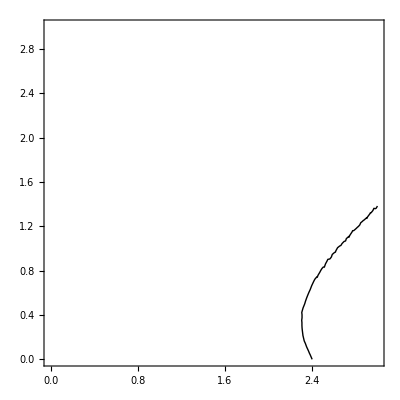

```mathematica
cyclePlot[1/2,0,1/50,3,Black]
```

### Plots

```mathematica
leg=LineLegend[{Directive[Thickness[0.02],Darker[Green]],Directive[Thickness[0.02],Red],Directive[Thickness[0.02],Darker[Purple]],Black},{Style["R_o(0)=1",Black,16],Style["R_o(1/2)=1",Black,16],Style["R_o(1)=1",Black,16],Style["Im[λ_max]=0",Black,14]},Background->White,LegendFunction->"Frame",LegendMargins->Automatic]
```

```mathematica
R0Region[range_,δin_,γin_,αin_]:=Show[R0Plot[δin,γin,αin,0,range,Darker[Green],Top,ColorData["GreenPinkTones"][0.2]],R0Plot[δin,γin,αin,0,range,Darker[Green],Bottom,ColorData["GreenPinkTones"][0.4]],R0Plot[δin,γin,αin,0.5,range,Red,Bottom,ColorData["GreenPinkTones"][0.6]],R0Plot[δin,γin,αin,0.99,range,Purple,Bottom,ColorData["GreenPinkTones"][0.8]],XYPlot[range],cyclePlot[δin,γin,αin,range,Black],AspectRatio->1,Frame->True,FrameTicks->None,(*FrameLabel->{{"Mismatching Transmission Y",None},{"Matching Transmission X",None}},*)LabelStyle->Directive[Bold,Black, 16],ImageSize->Large,Epilog->{Text[Style["Not Valid:\n X<Y",18,White],Scaled[{0.2,0.7}]],
Text[Style["Disease \n always spreads",18,Black],Scaled[{0.85,0.7}]],
Text[Style["Coevolution facilitated \n disease spread ",18,Black],Scaled[{0.62,0.27}]],Text[Style["Coevolution \n driven \n disease free",18,Black],Scaled[{0.46,0.08}]],Text[Style["Always \n disease free",18,Black],Scaled[{0.2,0.08}]],Text[Style["No Cycles",14,Black,Italic],Scaled[{0.9,0.15}]],Inset[leg,Scaled[{0.15,0.4}]]}]
```

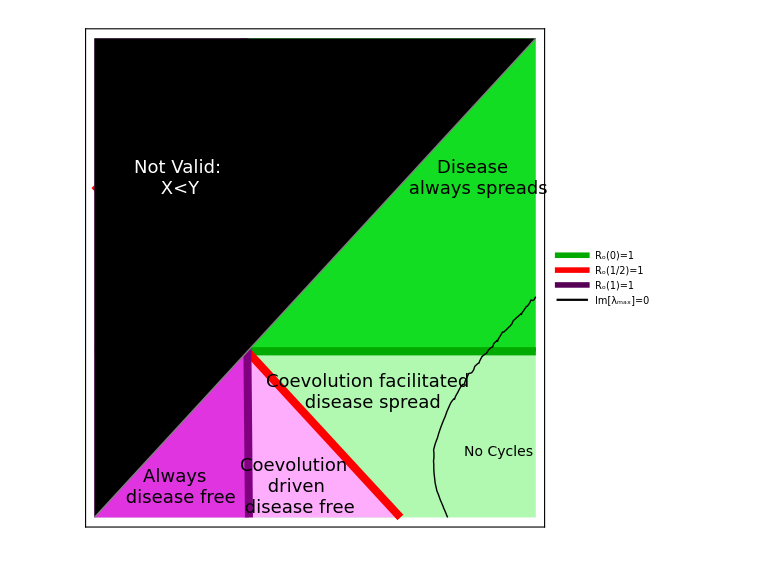

```mathematica
R0Region[3,0.5,0,0.02]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/Region.pdf",R0Region[3,0.5,0,0.02],ImageResolution->500];
```

Neutral Expectation

Given a sample path (s[1,t], s[2,t], i[1,1,t], i[1,2,t] i[2,1,t],i[2,2,t]) we can derive a differential for the heterozygosity at a neutral (unlinked) locus. We do so by considering the effect of each the 6 possible events (susceptible birth, infected birth, susceptible death, infected death, transmission, and recovery) on the allele frequency at the neutral locus and hence on the heterozygosity at the neutral locus.  Since the population is structured into susceptible and infected compartments we calculate the population level heterozygosity by first calculating the dynamics within each component (Hs[t] and Hi[t]) as well as between components Hsi[t].

H[t]=(Ns/(Ns+Ni))^2 Hi[t]+2(Ns/(Ns+Ni))(Ni/(Ns+Ni))Hsi[t]+(Ni/(Ns+Ni))^2 Hi[t]
Ns=s[1,t]+s[2,t]

Letting the rate of susceptible births be λS, infected births λI, susceptible deaths μS, infected deaths μI, and transmission events be B, the resulting differential equations are given by:

```mathematica
dHs[t]/dt=λS ()+λI()+μS()+B ()
dHi[t]/dt=μI()+B ()
dHsi[t]/dt=λI()+B ()
```

```mathematica
ratesSub={λS->b(s[1,t]+s[2,t])(1-(s[1,t]+s[2,t]+i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])/κ),λI->b(i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])(1-(s[1,t]+s[2,t]+i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])/κ),μS->δ(s[1,t]+s[2,t]),μI->(δ+α)(i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t]),Β-> X/κ(s[1,t](i[1,1,t]+i[1,2,t])+s[2,t](i[2,1,t]+i[2,2,t]))+Y/κ(s[2,t](i[1,1,t]+i[1,2,t])+s[1,t](i[2,1,t]+i[2,2,t])),Γ->γ(i[1,1,t]+i[1,2,t]+i[2,1,t]+i[2,2,t])};
```

## Effect of individual events

### Heterozygosity within the susceptible population

Susceptible Birth

```mathematica
temp=(pS 2pS2 qS2/.qS2->1-pS2/.pS2->(Ns pS+1)/(Ns+1))+((1-pS)2pS2 qS2/.qS2->1-pS2/.pS2->(Ns pS)/(Ns+1))-2 pS(1-pS)//Simplify;
Hsλs=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}]
```

-Hs[t]/(1+Ns)^2

Infected Birth

```mathematica
temp=(pI 2pS2 qS2/.qS2->1-pS2/.pS2->(Ns pS+1)/(Ns+1))+((1-pI)2pS2 qS2/.qS2->1-pS2/.pS2->(Ns pS)/(Ns+1))-2 pS(1-pS)//FullSimplify;
Hsλi=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//FullSimplify
```

(-(1+2 Ns) Hs[t]+2 Ns Hsi[t])/(1+Ns)^2

Susceptible Death

```mathematica
temp=(pS 2 pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS-1)/(Ns-1) )+((1-pS)2pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS)/(Ns-1))-2 pS(1-pS)//FullSimplify;
Hsμs=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}]
```

-Hs[t]/(-1+Ns)^2

Infected Death- No effect

Transmission

```mathematica
temp=(pS 2 pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS-1)/(Ns-1) )+((1-pS)2pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS)/(Ns-1))-2 pS(1-pS)//FullSimplify;
HsΒ=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}]
```

-Hs[t]/(-1+Ns)^2

Recovery

```mathematica
temp=(pI 2 pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS+1)/(Ns+1) )+((1-pI)2pS2 qS2/.qS2-> 1-pS2/.pS2->(Ns pS)/(Ns+1))-2 pS(1-pS)//FullSimplify;
HsΓ=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//FullSimplify
```

(-(1+2 Ns) Hs[t]+2 Ns Hsi[t])/(1+Ns)^2

### Heterozygosity within the infected population

Susceptible Birth - No effect

Infected Birth- No effect

Susceptible Death- No effect

Infected Death

```mathematica
temp=(pI 2 pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI-1)/(Ni-1) )+((1-pI)2pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI)/(Ni-1))-2 pI(1-pI)//FullSimplify;
Hiμi=FullSimplify[Expand[temp]/.{pI^2-> (2pI-Hi[t])/2}]
```

-Hi[t]/(-1+Ni)^2

Transmission

```mathematica
temp=(pS 2pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI+1)/(Ni+1))+((1-pS)2pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI)/(Ni+1))-2 pI(1-pI)//FullSimplify;
HiΒ=FullSimplify[Expand[temp]/.{pI^2-> (2pI-Hi[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//Simplify
```

(-(1+2 Ni) Hi[t]+2 Ni Hsi[t])/(1+Ni)^2

Recovery

```mathematica
temp=(pI 2 pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI-1)/(Ni-1) )+((1-pI)2pI2 qI2/.qI2-> 1-pI2/.pI2->(Ni pI)/(Ni-1))-2 pI(1-pI)//FullSimplify;
HiΓ=FullSimplify[Expand[temp]/.{pI^2-> (2pI-Hi[t])/2}]
```

-Hi[t]/(-1+Ni)^2

### Cross Heterozygosity

Susceptible Birth- No effect

Infected Birth

```mathematica
temp=(pI (pS2(1-pI)+pI(1-pS2))/.pS2->(Ns pS+1)/(Ns+1))+((1-pI) (pS2(1-pI)+pI(1-pS2))/.pS2->(Ns pS)/(Ns+1))-pS(1-pI)-pI(1-pS)//Simplify;
Hsiλi=FullSimplify[Expand[temp]/.{pI^2-> (2pI-Hi[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//Simplify
```

(Hi[t]-Hsi[t])/(1+Ns)

Susceptible Death- No effect

Infected Death- No effect

Transmission

```mathematica
temp=(pS (pS2(1-pI2)+pI2(1-pS2))/.pS2->(Ns pS-1)/(Ns-1)/.pI2->(Ni pI+1)/(Ni+1))+((1-pS) (pS2(1-pI2)+pI2(1-pS2))/.pS2->(Ns pS)/(Ns-1)/.pI2->(Ni pI)/(Ni+1))-pS(1-pI)-pI(1-pS)//Simplify;
HsiΒ=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}/.{pI^2-> (2pI-Hi[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//FullSimplify
```

(Ns Hs[t]+Hsi[t]-Ns Hsi[t])/((1+Ni) (-1+Ns))

Recovery

```mathematica
temp=(pI (pS2(1-pI2)+pI2(1-pS2))/.pS2->(Ns pS+1)/(Ns+1)/.pI2->(Ni pI-1)/(Ni-1))+((1-pI) (pS2(1-pI2)+pI2(1-pS2))/.pS2->(Ns pS)/(Ns+1)/.pI2->(Ni pI)/(Ni-1))-pS(1-pI)-pI(1-pS)//Simplify;
HsiΓ=FullSimplify[Expand[temp]/.{pS^2-> (2pS-Hs[t])/2}/.{pI^2-> (2pI-Hi[t])/2}]/.{pI->(-Hsi[t]+pS)/(-1+2 pS)}//FullSimplify
```

(Ni Hi[t]+Hsi[t]-Ni Hsi[t])/((-1+Ni) (1+Ns))

## Differential Equations

```mathematica
odes={D[Hs[t],t]==λs Hsλs+ λi Hsλi+μs Hsμs+Β HsΒ+Γ HsΓ,D[Hi[t],t]== μi Hiμi+Β HiΒ+Γ HiΓ,D[Hsi[t],t]==λi Hsiλi+ Β HsiΒ+Γ HsiΓ,Hs[0]==0.5,Hi[0]==0.5,Hsi[0]==0.5}(*/.{λs->b sTot[t](1-(sTot[t]+iTot[t])/κ),λi->b iTot[t](1-(sTot[t]+iTot[t])/κ),μs->δ sTot[t],μi->(δ+α) iTot[t],Β->β sTot[t]iTot[t]}*)
```

{Hs'[t]==-(Β Hs[t])/(-1+Ns)^2-(λs Hs[t])/(1+Ns)^2-(μs Hs[t])/(-1+Ns)^2+(Γ (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]))/(1+Ns)^2+(λi (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]))/(1+Ns)^2,Hi'[t]==-(Γ Hi[t])/(-1+Ni)^2-(μi Hi[t])/(-1+Ni)^2+(Β (-(1+2 Ni) Hi[t]+2 Ni Hsi[t]))/(1+Ni)^2,Hsi'[t]==(λi (Hi[t]-Hsi[t]))/(1+Ns)+(Γ (Ni Hi[t]+Hsi[t]-Ni Hsi[t]))/((-1+Ni) (1+Ns))+(Β (Ns Hs[t]+Hsi[t]-Ns Hsi[t]))/((1+Ni) (-1+Ns)),Hs[0]==0.5,Hi[0]==0.5,Hsi[0]==0.5}

```mathematica
{D[Hs[t],t]==λs Hsλs+ λi Hsλi+μs Hsμs+Β HsΒ+Γ HsΓ,D[Hi[t],t]== μi Hiμi+Β HiΒ+Γ HiΓ,D[Hsi[t],t]==λi Hsiλi+ Β HsiΒ+Γ HsiΓ,Hs[0]==0.5,Hi[0]==0.5,Hsi[0]==0.5}/.{λs->b sTot[t](1-(sTot[t]+iTot[t])/κ),λi->b iTot[t](1-(sTot[t]+iTot[t])/κ),μs->δ sTot[t],μi->(δ+α) iTot[t],Β->β sTot[t]iTot[t],Γ-> γ iTot[t]}
```

{Hs'[t]==(γ (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]) iTot[t])/(1+Ns)^2-(δ Hs[t] sTot[t])/(-1+Ns)^2-(β Hs[t] iTot[t] sTot[t])/(-1+Ns)^2+(b (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]) iTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns)^2-(b Hs[t] sTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns)^2,Hi'[t]==-(γ Hi[t] iTot[t])/(-1+Ni)^2-((α+δ) Hi[t] iTot[t])/(-1+Ni)^2+(β (-(1+2 Ni) Hi[t]+2 Ni Hsi[t]) iTot[t] sTot[t])/(1+Ni)^2,Hsi'[t]==(γ (Ni Hi[t]+Hsi[t]-Ni Hsi[t]) iTot[t])/((-1+Ni) (1+Ns))+(β (Ns Hs[t]+Hsi[t]-Ns Hsi[t]) iTot[t] sTot[t])/((1+Ni) (-1+Ns))+(b (Hi[t]-Hsi[t]) iTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns),Hs[0]==0.5,Hi[0]==0.5,Hsi[0]==0.5}

## Simulations

```mathematica
λ[s1_,s2_,i1_,i2_]:=Max[0,b (1-(s1+s2+i1+i2)/κ)];
μS[s1_,s2_,i1_,i2_]:=δ ;
μI[s1_,s2_,i1_,i2_]:=(δ+α);
Β[s1_,s2_,i1_,i2_]:=β(i1+i2)
Γ[s1_,s2_,i1_,i2_]:=γ
```

```mathematica
TotalRate[s1_,s2_,i1_,i2_,pars_]:=λ[s1,s2,i1,i2](s1+s2+i1+i2)+μS[s1,s2,i1,i2](s1+s2)+μI[s1,s2,i1,i2](i1+i2)+Β[s1,s2,i1,i2](s1+s2)+Γ[s1,s2,i1,i2](i1+i2)/.pars
samp[s1_,s2_,i1_,i2_,pars_]:=Block[{out,Δt},
Δt=RandomVariate[ExponentialDistribution[TotalRate[s1,s2,i1,i2,pars]]];
RandomChoice[{λ[s1,s2,i1,i2](s2+i2)/.pars,λ[s1,s2,i1,i2](s1+i1)/.pars,μS[s1,s2,i1,i2]s2/.pars,μS[s1,s2,i1,i2]s1/.pars,μI[s1,s2,i1,i2]i2/.pars,μI[s1,s2,i1,i2]i1/.pars,Β[s1,s2,i1,i2]s2/.pars,Β[s1,s2,i1,i2]s1/.pars,Γ[s1,s2,i1,i2]i2/.pars,Γ[s1,s2,i1,i2]i1/.pars}-> 
{{Δt,0,1,0,0},{Δt,1,0,0,0},{Δt,0,-1,0,0},{Δt,-1,0,0,0},{Δt,0,0,0,-1},{Δt,0,0,-1,0},{Δt,0,-1,0,1},{Δt,-1,0,1,0},{Δt,0,1,0,-1},{Δt,1,0,-1,0}}]]
```

```mathematica
sim[s0_,i0_,nRep_,pars_]:=Module[{out,OUT,e,r},OUT={};
For[r=1,r≤nRep,r++,
out={{0,Round[s0/2],Round[s0/2],Round[i0/2],Round[i0/2]}};
While[out[[-1,1]]<tMax/.pars,
If[Total[out[[-1,{2,3,4,5}]]]==0,AppendTo[out,{tMax/.pars,0,0}],
AppendTo[out,out[[-1]]+samp[out[[-1,2]],out[[-1,3]],out[[-1,4]],out[[-1,5]],pars]]
]
];
AppendTo[OUT,out]
];
OUT
]
```

```mathematica
Pars={b->1,δ->0.1,α->0.1,β->0.01,γ->0.1,κ->500,tMax->1};
```

```mathematica
ExampleSims=sim[100,30,2000,Pars];
Clear[NDyn,AFDyn]
NDyn[vec_]:=NDyn[vec]=Map[Map[{#[[1]],Total[#[[vec]]]}&,#]&,ExampleSims];
AFDyn[vec1_,vec2_]:=AFDyn[vec1,vec2]=Map[Map[{#[[1]],Total[#[[vec1]]]/(Total[#[[vec1]]]+Total[#[[vec2]]])//N}&,#]&,ExampleSims];
```

```mathematica
Clear[AFDynTab]
AFDynTab[npts_,AFDyn_,pars_]:=AFDynTab[npts,AFDyn,pars]=Block[{f,e,r,out,OUT},OUT={};
For[r=1,r≤Length[AFDyn],r++,
out={{0,0.5}};
f=Interpolation[AFDyn[[r]],InterpolationOrder->0];
For[e=1,e≤npts,e++,
AppendTo[out,{e (tMax/.pars)/npts,f[e (tMax/.pars)/npts]}];
];
AppendTo[OUT,out];
];
OUT//N]
```

```mathematica
GV[npts_,AFDyn_,pars_]:=Map[Map[{#[[1]],2#[[2]](1-#[[2]])}&,#]&, AFDynTab[npts,AFDyn,pars]]
```

```mathematica
Clear[GVExp];(*Clear[finalnum];*)
GVExp[npts_,NDyn_,pars_]:=GVExp[npts,NDyn,pars]=Block[{r,sTot,iTot,nSol,HsSol,HiSol,HsiSol,out},out={};
For[r=1,r≤Min[50,Length[NDyn]](*Approximation for speed purposes*),r++,
sTot=Interpolation[Map[{#[[1]],#[[2]]+#[[3]]}&,ExampleSims[[r,;;]]],InterpolationOrder->0];
iTot=Interpolation[Map[{#[[1]],#[[4]]+#[[5]]}&,ExampleSims[[r,;;]]],InterpolationOrder->0];
nSol=Flatten[NDSolve[{Hs'[t]==(γ (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]) iTot[t])/(1+Ns)^2-(δ Hs[t] sTot[t])/(-1+Ns)^2-(β Hs[t] iTot[t] sTot[t])/(-1+Ns)^2+(b (-(1+2 Ns) Hs[t]+2 Ns Hsi[t]) iTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns)^2-(b Hs[t] sTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns)^2,Hi'[t]==-(γ Hi[t] iTot[t])/(-1+Ni)^2-((α+δ) Hi[t] iTot[t])/(-1+Ni)^2+(β (-(1+2 Ni) Hi[t]+2 Ni Hsi[t]) iTot[t] sTot[t])/(1+Ni)^2,Hsi'[t]==(γ (Ni Hi[t]+Hsi[t]-Ni Hsi[t]) iTot[t])/((-1+Ni) (1+Ns))+(β (Ns Hs[t]+Hsi[t]-Ns Hsi[t]) iTot[t] sTot[t])/((1+Ni) (-1+Ns))+(b (Hi[t]-Hsi[t]) iTot[t] (1-(iTot[t]+sTot[t])/κ))/(1+Ns),Hs[0]==0.5,Hi[0]==0.5,Hsi[0]==0.5}/.{Ns->sTot[t],Ni->iTot[t]}/.pars,{Hs[t],Hi[t],Hsi[t]},{t,0,tMax/.pars}]];
Clear[HsSol,HiSol,HsiSol];
HsSol[τ_]:=HsSol[τ]=Hs[t]/.nSol/.{t->τ};
HiSol[τ_]:=HiSol[τ]=Hi[t]/.nSol/.{t->τ};
HsiSol[τ_]:=HsiSol[τ]=Hsi[t]/.nSol/.{t->τ};
AppendTo[out,Table[{τ,(sTot[τ]/(sTot[τ]+iTot[τ]))^2 HsSol[τ]+(iTot[τ]/(sTot[τ]+iTot[τ]))^2 HiSol[τ]+2(sTot[τ]/(sTot[τ]+iTot[τ]))(iTot[τ]/(sTot[τ]+iTot[τ]))HsiSol[τ](*(1/2 (1-√(1-2 HiSol[τ]) √(1-2 HsSol[τ])))*)},{τ,0,tMax/.pars, (tMax/.pars)/npts}]];
];
out
]
```

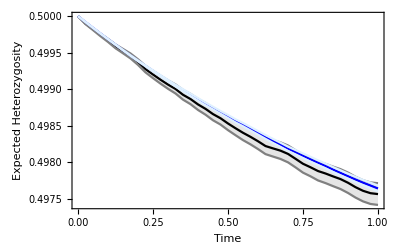

```mathematica
Show[ListLinePlot[{Mean[GV[40,AFDyn[{2,4},{3,5}],Pars]],Mean[GV[40,AFDyn[{2,4},{3,5}],Pars]]+2 StandardDeviation[GV[40,AFDyn[{2,4},{3,5}],Pars]]/Sqrt[Length[GV[40,AFDyn[{2,4},{3,5}],Pars]]],Mean[GV[40,AFDyn[{2,4},{3,5}],Pars]]-2 StandardDeviation[GV[40,AFDyn[{2,4},{3,5}],Pars]]/Sqrt[Length[GV[40,AFDyn[{2,4},{3,5}],Pars]]]},PlotStyle->{Black,Gray,Gray},Filling->2->{3}],ListLinePlot[{Mean[GVExp[40,NDyn[{2,3,4,5}],Pars]],Mean[GVExp[40,NDyn[{2,3,4,5}],Pars]]+2 StandardDeviation[GVExp[40,NDyn[{2,3,4,5}],Pars]]/Sqrt[Length[GVExp[40,NDyn[{2,3,4,5}],Pars]]],Mean[GVExp[40,NDyn[{2,3,4,5}],Pars]]-2 StandardDeviation[GVExp[40,NDyn[{2,3,4,5}],Pars]]/Sqrt[Length[GVExp[40,NDyn[{2,3,4,5}],Pars]]]},PlotStyle->{Blue,LightBlue,LightBlue},Filling->2->{3}],Frame->True,FrameLabel->{"Time","Expected Heterozygosity"}]
```

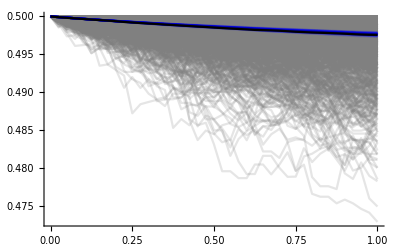

```mathematica
Show[ListLinePlot[GV[40,AFDyn[{2,4},{3,5}],Pars],PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.2]]],
ListLinePlot[GVExp[40,NDyn[{2,3,4,5}],Pars],PlotStyle->Directive[Blue, Opacity[0.1]]],ListLinePlot[GVExp[40,NDyn[{2,3,4,5}],Pars]//Mean,PlotStyle->Darker[Blue]],ListLinePlot[Mean[GV[40,AFDyn[{2,4},{3,5}],Pars]],PlotStyle->Black]]
```

Numerical Integration

This section uses the parameters from the simulations.  To obtain these parameters run section Individual-Based Simulations>Importing Data>Parameters and Data

```mathematica
ODEs[pars_]:=Flatten[Join[Table[D[s[h,t],t]==f1[h,t],{h,1,2}],Table[D[i[h,p,t],t]==f2[h,p,t],{h,1,2},{p,1,2}]]]/.pars
```

```mathematica
Inits[pars_]:=Flatten[Join[Table[s[h,0]==Sum[s[k,t],{k,1,2}]*If[h==1,0.8,0.2],{h,1,2}],Table[i[h,p,0]==Sum[i[k,l,t],{k,1,2},{l,1,2}]*If[h==1,0.8,0.2]*If[p==1,0.8,0.2],{h,1,2},{p,1,2}]]]/.equEnd/.pars
```

```mathematica
vars=Flatten[Join[Table[s[h,t],{h,1,2}],Table[ i[h,p,t],{h,1,2},{p,1,2}]]];
```

```mathematica
Clear[nsol]
nsol[pars_]:=nsol[pars]=Flatten[NDSolve[Join[ODEs[pars],Inits[pars]],vars,{t,0,1000}]]
pHsol[pars_,τ_]:=(s[1,t]+Sum[i[1,p,t],{p,1,2}])/Sum[s[h,t]+Sum[i[h,p,t],{p,1,2}],{h,1,2}]/.nsol[pars]/.{t->τ}
pPsol[pars_,τ_]:=Sum[i[h,1,t],{h,1,2}]/Sum[i[h,p,t],{h,1,2},{p,1,2}]/.nsol[pars]/.{t->τ}
```

```mathematica
DetAFPlot[file_,run_,rep_,color_]:=Show[ListLinePlot[Table[{pHsol[simPars[file,run,rep],τ],pPsol[simPars[file,run,rep],τ]},{τ,0,500}],PlotStyle->color]/.Line[x_]:>{Arrowheads[Table[.05,{r,{2}}]],Arrow[x]},
ListPlot[{{pHsol[simPars[file,run,rep],0],pPsol[simPars[file,run,rep],0]}},PlotStyle->Red,PlotMarkers->{●,14}],PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

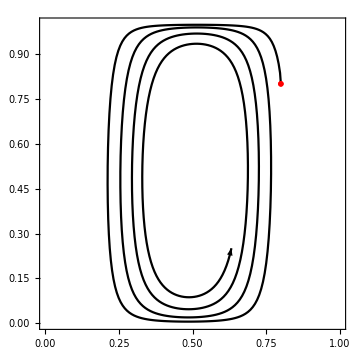

```mathematica
DetAFPlot[fileE,1,3,Black]
Export[NotebookDirectory[]<>"Plots/Epi_Det_AF.pdf",%,ImageResolution->300];
```

```mathematica
DetHetPlot[file_,run_,rep_,color_]:=Show[ListLinePlot[Table[{τ,2pHsol[simPars[file,run,rep],τ](1-pHsol[simPars[file,run,rep],τ])},{τ,0,500}],PlotStyle->color,PlotRange->{0,0.5}],ListPlot[{{0,2pHsol[simPars[file,run,rep],0](1-pHsol[simPars[file,run,rep],0])}},PlotStyle->Red,PlotMarkers->{●,14}],ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

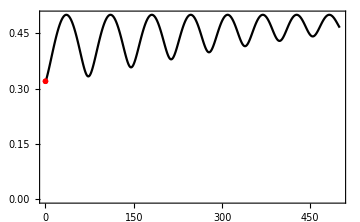

```mathematica
DetHetPlot[fileE,1,3,Black]
Export[NotebookDirectory[]<>"Plots/Epi_Det_Het.pdf",%,ImageResolution->300];
```

## Ensemble Moment Dynamics

## Substituitons

### Moment Substitutions

```mathematica
first=Join[Table[δS[h]->μδS[h],{h,1,2}],Table[δI[k,p]->μδI[k,p],{k,1,2},{p,1,2}]]//Flatten;
```

```mathematica
second=Block[{out},out={};
Table[AppendTo[out,Solve[CδSS[h1,h2]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])]/.δS[h1]δS[h2]->X,X][[1]]/.first/.X-> δS[h1]δS[h2]],{h1,1,2},{h2,h1,2}];
Table[AppendTo[out,Solve[CδSI[h1,p1,k1]==Expand[(δS[h1]-μδS[h1])(δI[p1,k1]-μδI[p1,k1])]/.δS[h1]δI[p1,k1]->X,X][[1]]/.first/.X->δS[h1]δI[p1,k1]],{h1,1,2},{p1,1,2},{k1,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2,Solve[CδII[p1,k1,p2,k2]==Expand[(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])]/.δI[p1,k1]δI[p2,k2]->X,X][[1]]/.first/.X->δI[p1,k1]δI[p2,k2],{}]],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}];
Flatten[out]
];
```

```mathematica
third=Block[{out},out={};
Table[AppendTo[out,Solve[CδSSS[h1,h2,h3]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])(δS[h3]-μδS[h3])]/.δS[h1]δS[h2]δS[h3]->X,X][[1]]/.second/.first/.X->δS[h1]δS[h2]δS[h3]],{h1,1,2},{h2,h1,2},{h3,h2,2}];
Table[AppendTo[out,Solve[CδSSI[h1,h2,p1,k1]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])(δI[p1,k1]-μδI[p1,k1])]/.δS[h1]δS[h2]δI[p1,k1]->X,X][[1]]/.second/.first/.X->δS[h1]δS[h2]δI[p1,k1]],{h1,1,2},{h2,h1,2},{p1,1,2},{k1,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2,Solve[CδSII[h1,p1,k1,p2,k2]==Expand[(δS[h1]-μδS[h1])(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])]/.δS[h1]δI[p1,k1]δI[p2,k2]->X,X][[1]]/.second/.first/.X->δS[h1]δI[p1,k1]δI[p2,k2],{}]],{h1,1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2≤2p3+k3,Solve[CδIII[p1,k1,p2,k2,p3,k3]==Expand[(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])(δI[p3,k3]-μδI[p3,k3])]/.δI[p1,k1]δI[p2,k2]δI[p3,k3]->X,X][[1]]/.second/.first/.X->δI[p1,k1]δI[p2,k2]δI[p3,k3],{}]],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2}];
Flatten[out]
];
```

```mathematica
fourth=Block[{out},out={};
Table[AppendTo[out,Solve[CδSSSS[h1,h2,h3,h4]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])(δS[h3]-μδS[h3])(δS[h4]-μδS[h4])]/.δS[h1]δS[h2]δS[h3]δS[h4]->X,X][[1]]/.second/.first/.X->δS[h1]δS[h2]δS[h3]δS[h4]],{h1,1,2},{h2,h1,2},{h3,h2,2},{h4,h3,2}];
Table[AppendTo[out,Solve[CδSSSI[h1,h2,h3,p1,k1]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])(δS[h3]-μδS[h3])(δI[p1,k1]-μδI[p1,k1])]/.δS[h1]δS[h2]δS[h3]δI[p1,k1]->X,X][[1]]/.second/.first/.X->δS[h1]δS[h2]δS[h3]δI[p1,k1]],{h1,1,2},{h2,h1,2},{h3,h2,2},{p1,1,2},{k1,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2,Solve[CδSSII[h1,h2,p1,k1,p2,k2]==Expand[(δS[h1]-μδS[h1])(δS[h2]-μδS[h2])(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])]/.δS[h1]δS[h2]δI[p1,k1]δI[p2,k2]->X,X][[1]]/.second/.first/.X->δS[h1]δS[h2]δI[p1,k1]δI[p2,k2],{}]],{h1,1,2},{h2,h1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2≤2p3+k3,
Solve[CδSIII[h1,p1,k1,p2,k2,p3,k3]==Expand[(δS[h1]-μδS[h1])(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])(δI[p3,k3]-μδI[p3,k3])]/.δS[h1]δI[p1,k1]δI[p2,k2]δI[p3,k3]->X,X][[1]]/.second/.first/.X->δS[h1]δI[p1,k1]δI[p2,k2]δI[p3,k3],{}]],{h1,1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2}];
Table[AppendTo[out,If[2p1+k1≤2p2+k2≤2p3+k3≤2p4+k4,Solve[CδIIII[p1,k1,p2,k2,p3,k3,p4,k4]==Expand[(δI[p1,k1]-μδI[p1,k1])(δI[p2,k2]-μδI[p2,k2])(δI[p3,k3]-μδI[p3,k3])(δI[p4,k4]-μδI[p4,k4])]/.δI[p1,k1]δI[p2,k2]δI[p3,k3]δI[p4,k4]->X,X][[1]]/.second/.first/.X->δI[p1,k1]δI[p2,k2]δI[p3,k3]δI[p4,k4],{}]],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2},{p4,p3,2},{k4,1,2}];
Flatten[out]
];
```

### Simplification

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
```

Let δH[i]=H[i]-OverHat[H[i]] and δP[i]=P-OverHat[P[i]].  We will assume that the deviations from equilibrium, δH and δP, are small.

Note that the covariance between the deviations from equilibrium are equal to the the covariance in the original variables.

```mathematica
eSub=Join[Table[s[h]->s[h,t]+ϵ δS[h],{h,1,2}],Table[i[h,p]->i[h,p,t]+ϵ δI[h,p],{h,1,2},{p,1,2}]]/.equEnd//Flatten//Simplify;
```

```mathematica
μeSubRev=Flatten[Join[Table[μδS[h]->μS[h,t]-s[h,t],{h,1,2}],Table[μδI[h,p]->μI[h,p,t]-i[h,p,t],{h,1,2},{p,1,2}],Table[CδSS[h1,h2]-> CSS[h1,h2,t],{h1,1,2},{h2,h1,2}],Table[CδSI[h1,p1,k1]-> CSI[h1,p1,k1,t],{h1,1,2},{p1,1,2},{k1,1,2}],Table[If[2p1+k1≤2p2+k2,CδII[p1,k1,p2,k2]-> CII[p1,k1,p2,k2,t],{}],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}],Table[CδSSS[h1,h2,h3]-> CSSS[h1,h2,h3,t],{h1,1,2},{h2,h1,2},{h3,h2,2}],Table[CδSSI[h1,h2,p1,k1]-> CSSI[h1,h2,p1,k1,t],{h1,1,2},{h2,h1,2},{p1,1,2},{k1,1,2}],Table[If[2p1+k1≤2p2+k2,CδSII[h1,p1,k1,p2,k2]-> CSII[h1,p1,k1,p2,k2,t],{}],{h1,1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}],Table[If[2p1+k1≤2p2+k2≤2p3+k3,CδIII[p1,k1,p2,k2,p3,k3]-> CIII[p1,k1,p2,k2,p3,k3,t],{}],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2}]]]/.equEnd//Flatten;
```

### Moment Closure

```mathematica
assump3=Flatten[Join[Table[CδSSSS[h1,h2,h3,h4]->0,{h1,1,2},{h2,h1,2},{h3,h2,2},{h4,h3,2}],Table[CδSSSI[h1,h2,h3,p1,k1]->0,{h1,1,2},{h2,h1,2},{h3,h2,2},{p1,1,2},{k1,1,2}],Table[If[2p1+k1≤2p2+k2,CδSSII[h1,h2,p1,k1,p2,k2]->0,{}],{h1,1,2},{h2,h1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}],Table[If[2p1+k1≤2p2+k2≤2p3+k3,CδSIII[h1,p1,k1,p2,k2,p3,k3]->0,{}],{h1,1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2}],Table[If[2p1+k1≤2p2+k2≤2p3+k3≤2p4+k4,CδIIII[p1,k1,p2,k2,p3,k3,p4,k4]->0,{}],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2},{p4,p3,2},{k4,1,2}]]];
```

```mathematica
assump2=Flatten[Join[Table[CδSSS[h1,h2,h3]->0,{h1,1,2},{h2,h1,2},{h3,h2,2}],Table[CδSSI[h1,h2,p1,k1]->0,{h1,1,2},{h2,h1,2},{p1,1,2},{k1,1,2}],
Table[If[2p1+k1≤2p2+k2,CδSII[h1,p1,k1,p2,k2]->0,{}],{h1,1,2},{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}],
Table[If[2p1+k1≤2p2+k2≤2p3+k3,CδIII[p1,k1,p2,k2,p3,k3]->0,{}],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2},{p3,p2,2},{k3,1,2}],assump3]];
```

```mathematica
assump1=Join[Table[CδSS[h1,h2]->0,{h1,1,2},{h2,h1,2}],
Table[CδSI[h1,p1,k1]->0,{h1,1,2},{p1,1,2},{k1,1,2}],
Table[If[2p1+k1≤2p2+k2,CδII[p1,k1,p2,k2]->0,{}],{p1,1,2},{k1,1,2},{p2,p1,2},{k2,1,2}],assump2]//Flatten;
```

Rates f[x] and change in x

```mathematica
fEpi=Join[(*Host birth*)Table[b(s[h]+Sum[i[h,l],{l,1,2}])(1-Sum[s[k]+Sum[i[k,l],{l,1,2}],{k,1,2}]/κ),{h,1,2}],
(*Susceptible Host death*)Table[δ s[h],{h,1,2}],
(*Infection*)Table[β[h,p] s[h]Sum[i[k,p],{k,1,2}],{h,1,2},{p,1,2}],
(*Infected Host Death*)Table[(δ+α) i[h,p],{h,1,2},{p,1,2}],
(*Pathogen Clearance*)Table[γ i[h,p],{h,1,2},{p,1,2}]
]/.βSub//Flatten;
```

```mathematica
ΔS[h1_]:=Join[(*Host birth*)Table[If[h==h1,1,0],{h,1,2}],
(*Susceptible Host death*)Table[If[h==h1,-1,0],{h,1,2}],
(*Infection*)Table[If[h==h1,-1,0],{h,1,2},{p,1,2}],
(*Infected Host Death*)Table[0,{h,1,2},{p,1,2}],
(*Pathogen Clearance*)Table[If[h==h1,1,0],{h,1,2},{p,1,2}]
]/.βSub//Flatten
```

```mathematica
ΔI[h1_,p1_]:=Join[(*Host birth*)Table[0,{h,1,2}],
(*Susceptible Host death*)Table[0,{h,1,2}],
(*Infection*)Table[If[h==h1&&p==p1,1,0],{h,1,2},{p,1,2}],
(*Infected Host Death*)Table[If[h==h1&&p==p1,-1,0],{h,1,2},{p,1,2}],
(*Pathogen Clearance*)Table[If[h==h1&&p==p1,-1,0],{h,1,2},{p,1,2}]
]/.βSub//Flatten
```

Differential Equations

## Means

```mathematica
Clear[dμSdt]
dμSdt[h_,t_]:=dμSdt[h,t]=Expand[Normal[Series[fEpi.ΔS[h]/.eSub,{ϵ,0,2}]]]/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dμIdt]
dμIdt[h_,p_,t_]:=dμIdt[h,p,t]=Expand[Normal[Series[fEpi.ΔI[h,p]/.eSub,{ϵ,0,2}]]]/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev/.{τ->t}
```

## Variances

```mathematica
Clear[dSSdt]
dSSdt[h1_,h2_,t_]:=dSSdt[h1,h2,t]=Expand[Normal[Series[Simplify[fEpi.Simplify[(s[h1]+ΔS[h1])(s[h2]+ΔS[h2])-s[h1]s[h2]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dSIdt]
dSIdt[h1_,p1_,k1_,t_]:=dSIdt[h1,p1,k1,t]=Expand[Normal[Series[Simplify[fEpi.Simplify[(s[h1]+ΔS[h1])(i[p1,k1]+ΔI[p1,k1])-s[h1]i[p1,k1]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dIIdt]
dIIdt[p1_,k1_,p2_,k2_,t_]:=dIIdt[p1,k1,p2,k2,t]=Expand[Normal[Series[Simplify[fEpi.Simplify[(i[p1,k1]+ΔI[p1,k1])(i[p2,k2]+ΔI[p2,k2])-i[p1,k1]i[p2,k2]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev/.{τ->t}
```

## Genetic Variance

```mathematica
HEM=Expand[Normal[Series[2 ((s[1]+Sum[i[1,p],{p,1,2}])/Sum[s[h]+Sum[i[h,p],{p,1,2}],{h,1,2}])(1-(s[1]+Sum[i[1,p],{p,1,2}])/Sum[s[h]+Sum[i[h,p],{p,1,2}],{h,1,2}])/.eSub,{ϵ,0,2}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev
```

## Individual-Based Simulations

Choosing Parameters

```mathematica
R0[1/2]//Simplify
```

((X+Y) (b-δ))/(2 b (α+γ+δ))

```mathematica
Solve[((X+Y) (b-δ))/(2 b (A+δ))==1,A]/.b->1//FullSimplify
```

{{A→1/2 (X+Y-(2+X+Y) δ)}}

```mathematica
fPstar=Sum[i[h,p,t],{h,1,2},{p,1,2}]/κ/.equEnd//Simplify;
```

```mathematica
fHstar=(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}])/κ/.equEnd//Simplify;
```

### Randomly sampling parameter space

Fixing the time scale assume b=1

Stability

```mathematica
Solve[(R0[1/2]/.{α->A-γ}/.b->1)==1,A]//FullSimplify
```

{{A→1/2 (X+Y-(2+X+Y) δ)}}

If 0<Y<X<1 then α+γ+δ<1

```mathematica
Clear[randParsEpi]
randParsEpi[npts_]:=randParsEpi[npts]=Block[{ct,fHr,fPr,Xr,Yr,δr,αr,γr,br,temp,temp2,out},out={};
For[ct=1,ct≤npts,ct++,
br=1;
Xr=RandomReal[{0,1}];Yr=RandomReal[{0,Xr}];
δr=RandomReal[{0.1,1}];
γr=RandomReal[{0.1,1/2 (Xr+Yr-(2+Xr+Yr) δr)}];
αr=RandomReal[{0,1/2 (Xr+Yr-(2+Xr+Yr) δr)-γr}];
temp2={X->Xr,Y->Yr,α->αr,γ->γr,b->br,δ->δr};
temp={fH->(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}])/κ/.equEnd/.temp2,fP->Sum[i[h,p,t],{h,1,2},{p,1,2}]/κ/.equEnd/.temp2,X->Xr,Y->Yr,α->αr,γ->γr,b->br,δ->δr};
If[(R0[1/2]/.temp)>1&&0.1<δr<br,
(*Print[temp];*)
AppendTo[out,temp],ct--
];
];
out
]
```

### γ=0;

```mathematica
Clear[randPars2Epi]
randPars2Epi[npts_]:=randPars2Epi[npts]=Block[{ct,fHr,fPr,Xr,Yr,δr,αr,γr,br,temp2,temp,out},out={};
For[ct=1,ct≤npts,ct++,
br=1;
Xr=RandomReal[{0,1}];Yr=RandomReal[{0,Xr}];
δr=RandomReal[{0.1,1}];
γr=0;
αr=RandomReal[{0,1/2 (Xr+Yr-(2+Xr+Yr) δr)-γr}];
temp2={X->Xr,Y->Yr,α->αr,γ->γr,b->br,δ->δr};
temp={fH->(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}])/κ/.equEnd/.temp2,fP->Sum[i[h,p,t],{h,1,2},{p,1,2}]/κ/.equEnd/.temp2,X->Xr,Y->Yr,α->αr,γ->γr,b->br,δ->δr};
If[(R0[1/2]/.temp)>1&&0.1<δr<br,
(*Print[temp];*)
AppendTo[out,temp],ct--
];
];
out
]
```

### Epidemiological Model

```mathematica
κSol[pars_,rep_]:=κ/.Flatten[Solve[(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.pars)== 10^(2+0.25*(rep-1)),κ],1]
nRep=7;
nDemes=1000;
gmax=250;
(*sampFreq=1;*)
```

```mathematica
epiFile[pars_]:=Block[{out,rep},
out="Input file for Ecological simulations

number of reps (nRep): "<> ToString[nRep]<>"
number of demes (nDemes): "<> ToString[nDemes]<>"
maximum number of generations (gmax): "<> ToString[gmax]<>"
host birth rate (b): "<> ToString[b/.pars]<>"
matching infection rate (X): "<> ToString[X/.pars]<>"
mismatching infection rate (Y): "<> ToString[Y/.pars]<>"
host natural death rate (delta): "<> ToString[δ/.pars]<>"
death probability (alpha): "<> ToString[α/.pars]<>"
pathogen death rate (gamma): "<>ToString[γ/.pars]<>"
carrying capacity (kappa): ";
For[rep=1,rep≤nRep,rep++,out=out<>ToString[κSol[pars,rep]]<>" "];
out
]
```

```mathematica
Do[Export[NotebookDirectory[]<>"/sims_11_1/inputEpi_"<>ToString[i]<>".txt",epiFile[randPars2Epi[100][[i]]]],{i,1,100}]
```

Importing Data

## Parameters and Data

```mathematica
(*Random Sampling*)
fileE=NotebookDirectory[]<>"sims_11_1/epi_11_4/runEpi_";
fileE2=NotebookDirectory[]<>"sims_11_1/epi_11_4/";
nRuns=100;
```

```mathematica
(*γ=0*)
(*fileE=NotebookDirectory[]<>"sims_11_1/epi_11_6/runEpi_";
fileE2=NotebookDirectory[]<>"sims_11_1/epi_11_6/";*)
```

```mathematica
Clear[pars]
pars[file_,run_]:=pars[file,run]=Import[file<>ToString[run]<>"/out.csv"];
```

```mathematica
pars[fileE,1]
```

{{RandomSeed:,1572884839},{number of reps (nRep):,7},{number of demes (nDemes):,1000},{maximum generations (gmax):,250},{host birth (b):,1},{matching infection rate (X):,7.86185},{mismatching infection rate (Y):,6.38572},{host death (delta):,0.358061},{virulent death probability (alpha):,0.947992},{pathogen death rate (gamma):,0.744909},{Values for kappa:,255.525,454.395,808.04,1436.92,2555.25,4543.95,8080.4,}}

```mathematica
Clear[nReps,nDemes,gmax]
Clear[X,Y,δ,α,γ,κ]
nReps[file_,run_]:=pars[file,run][[2,2]];
nDemes[file_,run_]:=pars[file,run][[3,2]];
gmax[file_,run_]:=pars[file,run][[4,2]];
b[file_,run_]:=pars[file,run][[5,2]]
X[file_,run_]:=pars[file,run][[6,2]]
Y[file_,run_]:=pars[file,run][[7,2]]
δ[file_,run_]:=pars[file,run][[8,2]]
α[file_,run_]:=pars[file,run][[9,2]]
γ[file_,run_]:=pars[file,run][[10,2]]
κ[file_,run_,rep_]:=pars[file,run][[11,rep+1]]
```

```mathematica
simPars[file_,run_,rep_]:={b->b[file,run],X->X[file,run],Y->Y[file,run],δ->δ[file,run],α->α[file,run],γ->γ[file,run],gmax->gmax[file,run],κ->κ[file,run,rep]}
```

```mathematica
Clear[time,state,stateN]
time[file_,run_,rep_]:=time[file,run,rep]=Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/time.csv"][[;;,;;-2]]
state[file_,run_,rep_]:=state[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,1,6}]//N
stateN[file_,run_,rep_]:=stateN[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,7,12}]//N
```

```mathematica
fileExist[file_,run_,rep_,t_]:=FileExistsQ[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[t]<>".csv"]
```

```mathematica
Clear[MoranNeut]
MoranNeut[file_,run_,rep_]:=MoranNeut[file,run,rep]=Table[0.5(1-2/(Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]))^g,{g,1,gmax[file,run]}]/.equEnd/.simPars[file,run,rep]
```

## Processing

### Bootstrap Functions

```mathematica
BootstrapMean[data_,nBoot_]:=BootstrapMean[data,nBoot]=Block[{out,b},out={};
For[b=1,b≤nBoot,b++,
AppendTo[out,Mean[RandomChoice[data,Length[data]]]]
];
out]
```

```mathematica
Bootstrap[data_,dummy_]:=Bootstrap[data,dummy]=RandomChoice[data,Length[data]]
```

### Equilibrium Population Size

```mathematica
Clear[nHEqu]
nHEqu[file_,run_,rep_]:=nHEqu[file,run,rep]=Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep]
```

```mathematica
Clear[nPEqu]
nPEqu[file_,run_,rep_]:=nPEqu[file,run,rep]=Sum[i[h,p,t],{p,1,2},{h,1,2}]/.equEnd/.simPars[file,run,rep]
```

### Allele Frequency

```mathematica
Clear[pHMtrx]
pHMtrx[file_,run_,rep_]:=pHMtrx[file,run,rep]=(state[file,run,rep][[1]]+state[file,run,rep][[3]]+state[file,run,rep][[4]])/Total[state[file,run,rep]]
```

```mathematica
Clear[pHNMtrx]
pHNMtrx[file_,run_,rep_]:=pHNMtrx[file,run,rep]=(stateN[file,run,rep][[1]]+stateN[file,run,rep][[3]]+stateN[file,run,rep][[4]])/Total[stateN[file,run,rep]]
```

### Heterozygosity

```mathematica
Clear[HetMtrx,HetMtrx2]
HetMtrx[file_,run_,rep_]:=HetMtrx[file,run,rep]=2pHMtrx[file,run,rep](1-pHMtrx[file,run,rep])//Chop
HetMtrx2[file_,run_,rep_]:=HetMtrx2[file,run,rep]=Table[HetMtrx[file,run,rep][[;;,g]]/.Indeterminate->0,{g,1,250}]//Transpose
```

```mathematica
Clear[HetNMtrx,HetNMtrx2]
HetNMtrx[file_,run_,rep_]:=HetNMtrx[file,run,rep]=2pHNMtrx[file,run,rep](1-pHNMtrx[file,run,rep])//Chop
HetNMtrx2[file_,run_,rep_]:=HetNMtrx2[file,run,rep]=Table[HetNMtrx[file,run,rep][[;;,g]]/.Indeterminate->MoranNeut[file,run,rep][[g]],{g,1,250}]//Transpose
```

### Heterozygosity at generation τ

```mathematica
Clear[HetCompMtrx2]
HetCompMtrx2[file_,rep_,τ_]:=HetCompMtrx2[file,rep,τ]=Import[fileE2<>"/HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv"]
```

### Harmonic Mean Population Size

```mathematica
Clear[NeMtrx]
NeMtrx[rep_]:=NeMtrx[rep]=Import[fileE2<>"/NeMtrx/NeMtrx_"<>ToString[rep]<>".csv"]
```

```mathematica
Clear[NeMtrx2]
NeMtrx2[rep_,g_]:=NeMtrx2[rep,g]=Import[fileE2<>"/NeMtrx/NeMtrx_"<>ToString[rep]<>"_"<>ToString[g]<>".csv"]
```

Processing- Run only once

### Preprocessing- RUN ONLY ONCE!

```mathematica
Clear[HetCompMtrx]
HetCompMtrx[file_,rep_,τ_]:=HetCompMtrx[file,rep,τ]=Table[{Mean[HetNMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetNMtrx2[file,run,rep][[;;,τ]],1000]],Mean[HetMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetMtrx2[file,run,rep][[;;,τ]],1000]]},{run,1,100}]
```

```mathematica
(*Run This Only Once*)
(*CreateDirectory[fileE2<>"/HetMtrx"];*)
Table[Export[fileE2<>"/HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv",HetCompMtrx[fileE,rep,τ]],{rep,3,7},{τ,10,250,10}];
```

### Harmonic Mean Population Size

```mathematica
state[fileE,1,3]//Dimensions
```

{6,1000,250}

```mathematica
Clear[HarmonicMeanNe]
HarmonicMeanNe[file_,run_,rep_,g_]:=HarmonicMeanNe[file,run,rep]=Block[{temp},temp=Total[state[file,run,rep][[;;,;;,;;g]]];
Map[If[Min[#]==0,0,g/Total[#^-1]]&,temp]]
```

```mathematica
NeExp[gen_]:=Do[Export[fileE2<>"NeMtrx/NeMtrx_"<>ToString[rep]<>"_"<>ToString[gen]<>".csv",Table[HarmonicMeanNe[fileE,run,rep,gen],{run,1,100}]];Print[rep],{rep,1,7}];
```

```mathematica
(*Run This Only Once*)
(*CreateDirectory[fileE2<>"NeMtrx"];*)
NeExp[10]
```

1

2

3

4

5

6

7

Plotting

## Dynamics of a single rep

```mathematica
dynPlot[file_,run_,rep_]:=Show[
(*Neutral Simulations*)
ListLinePlot[{Mean[HetNMtrx[file,run,rep]],Mean[HetNMtrx[file,run,rep]]+2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetNMtrx[file,run,rep]]-2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Black,Gray,Gray},Filling->2->{3},FillingStyle->Directive[Gray,Opacity[0.2]]],
(*Coevolutionary Simulations*)
(*ListLinePlot[Table[Mean[Bootstrap[Htable[file,run,rep],bs]],{bs,0,100}],PlotStyle->Directive[Pink,Opacity[0.1]]],*)ListLinePlot[{Mean[HetMtrx[file,run,rep]],Mean[HetMtrx[file,run,rep]]+2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetMtrx[file,run,rep]]-2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Red,Pink,Pink},Filling->2->{3},FillingStyle->Directive[Pink,Opacity[0.2]]],
(*Moran Neutral Expectation*)
ListLinePlot[MoranNeut[file,run,rep],PlotStyle->Purple](*,PlotRange->{{0,5},{0.48,0.5}}*)]
```

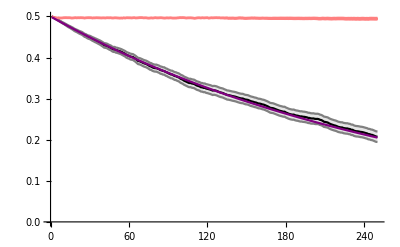

```mathematica
dynPlot[fileE,8,4]
```

## Mean Heterozygosity

### Mean Smoothing

Project data onto the X=Y line.

```mathematica
Clear[dataNew]
dataNew[data_]:=dataNew[data]=Transpose[{Cos[Abs[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]]*Sqrt[Total[Transpose[data^2]]],Sin[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]*Sqrt[Total[Transpose[data^2]]]}]
```

A gaussian weighting of the data  near the point xNew along the X=Y line

```mathematica
Clear[weights]
weights[xNew_,αW_,data_]:=weights[xNew,αW,data]=Exp[-(dataNew[data][[;;,1]]-xNew)^2/(2 αW^2)]//Chop;
```

Find the weighted mean and standard deviation and standard error.

```mathematica
Clear[meanNew]
meanNew[xNew_,αW_,data_]:=meanNew[xNew,αW,data]=Total[weights[xNew,αW,data]dataNew[data][[;;,2]]]/Total[weights[xNew,αW,data]]
```

```mathematica
SDNew[xNew_,αW_,data_]:=Sqrt[Total[weights[xNew,αW,data]*(dataNew[data][[;;,2]]-meanNew[xNew,αW,data])^2]/Total[weights[xNew,αW,data]]]
```

```mathematica
SENew[xNew_,αW_,data_]:=SDNew[xNew,αW,data]/Sqrt[Total[weights[xNew,αW,data]]]
```

The rolling average fit along the X+Y line (rotated plot)

```mathematica
Clear[RollFit]
RollFit[αW_,npts_,data_]:=RollFit[αW,npts,data]=Table[{x,meanNew[x,αW,data]},{x,0.001,Sqrt[2*0.5^2]-0.001,Sqrt[2*0.5^2]/npts}];
```

Projecting back into the original coordinates.

```mathematica
RollFitOld[αW_,npts_,data_]:=Transpose[{Cos[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2],Sin[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2]}]
```

### WF Diploid Over-dominance as a comparison

transition probability of i copies to j copies of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==0,If[j==0,1,0],If[i==n,If[j==n,1,0],Binomial[ n,j]((i/n (1+w[i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^j(((n-i)/n (1+w[n-i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^(n-j)]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t].p0Vec[n]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hNeut[n_,t_]:=1/2 Exp[-t/n]
```

```mathematica
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],0.01,250]},{npower,2,2.75,0.25}]
```

{{1/(2 ⅇ^(5/2)),0.0899257},{1/(2 ⅇ^(125/89)),0.239548},{1/(2 ⅇ^(125/158)),0.374202},{1/(2 ⅇ^(125/281)),0.443671}}

```mathematica
HetOver=Join[{{0,0}},temp,{{0.5,0.5}}]//N;
```

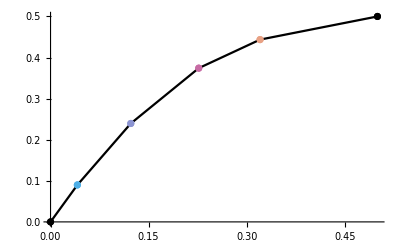

```mathematica
Show[ListLinePlot[HetOver,PlotStyle->Black],ListPlot[Map[{#}&,HetOver],PlotStyle->Join[{Black},Table[ ColorData["CMYKColors"][(rep-1)/6],{rep,1,4}],{Black}]]]
```

### Moran Diploid Over-dominance as a comparison

transition probability of i copies to j copies (out of n total copies) of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
wA[i_,n_,s_]:=((i/n)(1-s)+(n-i)/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
wa[i_,n_,s_]:=((n-i)/n(1-s)+i/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(wA[p[t]n,n,s]-1)p[t]/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==j,1-wA[i,n,s] i/n(n-i)/n-wa[i,n,s](n-i)/n i/n,If[j==i+1,wA[i,n,s] i/n(n-i)/n,If[j==i-1,wa[i,n,s](n-i)/n i/n,0]]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t n].p0Vec[n]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hNeut[n_,t_]:=1/2 (1-2/n)^t//N
```

```mathematica
Clear[HetOver]
HetOver[s_,τ_]:=HetOver[s,τ]=Block[{temp},
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],s,τ]},{npower,2,3.25,0.25}];
Join[{{0,0}},temp,{{0.5,0.5}}]//N]
```

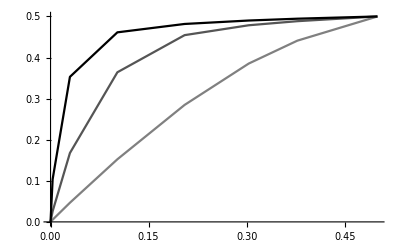

```mathematica
ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}]
```

### Variation within versus across replicates

```mathematica
?ErrorListPlot
```

RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TI"]}], "}"}], "]"}] plots points corresponding to a list of values RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", " ", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", " ", StyleBox["…", "TR"]}], with corresponding error bars. The errors have magnitudes RowBox[{SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}].
RowBox[{"ErrorListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], "1"], "]"}]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], StyleBox["2", "TR"]], "]"}]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates and error magnitudes.

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

```mathematica
VarVisual[rep_]:=Block[{temp},temp=Sort[Map[{#[[3]],1.96#[[4]]}&,HetCompMtrx2[fileE,rep,250]],#1[[1]]<#2[[1]]&];
ErrorListPlot[temp,PlotRange->{Min[Map[#[[1]]-#[[2]]&,temp]]0.95,Max[Map[#[[1]]+#[[2]]&,temp]]*1.05},Frame->True,FrameTicksStyle->Directive[Black,12],ImageSize->Medium,PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]]
```

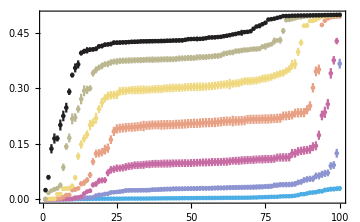

```mathematica
Show[Table[VarVisual[rep],{rep,1,7}],PlotRange->All]
Export[NotebookDirectory[]<>"Plots/Epi_Variation.pdf",%,ImageResolution->300];
```

```mathematica
VarWB=Table[{Round[Mean[HetCompMtrx2[fileE,rep,250][[;;,4]]],0.0001],Round[StandardDeviation[HetCompMtrx2[fileE,rep,250][[;;,3]]],0.001],Round[StandardDeviation[HetCompMtrx2[fileE,rep,250][[;;,3]]]/Mean[HetCompMtrx2[fileV,rep,250][[;;,4]]],0.01]},{rep,1,7}]
```

{{0.0013,0.007,5.74},{0.003,0.04,13.21},{0.0047,0.08,17.05},{0.0053,0.111,21.02},{0.0047,0.123,26.43},{0.0035,0.116,33.22},{0.0024,0.091,37.29}}

```mathematica
Clear[temp]
```

```mathematica
ErrorListPlot2[file_,rep_,τ_]:=Block[{temp},

temp=Sort[HetCompMtrx2[file,rep,τ],#1[[3]]<#2[[3]]&];
Show[ListLinePlot[Table[{{r,temp[[r,3]]-2temp[[r,4]]},{r,temp[[r,3]]+2temp[[r,4]]}},{r,1,100}],PlotStyle->Directive[Lighter[ColorData["CMYKColors"][(rep-1)/6]]],PlotRange->{0,0.5}],
ListPlot[Table[{r,temp[[r,3]]},{r,1,100}],PlotStyle->ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{"●",4}]
]
]
```

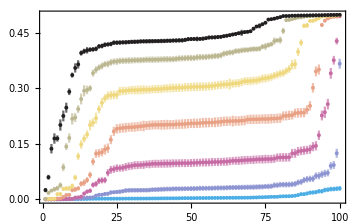

```mathematica
Show[Table[ErrorListPlot2[fileE,rep,250],{rep,1,7}],PlotRange->All,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
Export[NotebookDirectory[]<>"Plots/Epi_Variation.pdf",%,ImageResolution->300];
```

```mathematica
Export[fileE2<>"VarWB.csv",VarWB]
```

/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/epi_11_4/VarWB.csv

### Comparison to the simulated neutral expectation

```mathematica
meanPlot[file_,τ_]:=Block[{sigData,meanData},
meanData=Flatten[Table[HetCompMtrx2[file,rep,τ][[;;,{1,3}]],{rep,1,7}],1];
sigData[rep_]:=sigData[rep]=Select[HetCompMtrx2[file,rep,τ],(#[[3]]-2 #[[4]])>(#[[1]]+2#[[2]])||(#[[3]]+2 #[[4]])<(#[[1]]-2#[[2]])&];
Show[
Table[
ListPlot[{sigData[rep][[;;,{1,3}]],Complement[HetCompMtrx2[file,rep,τ],sigData[rep]][[;;,{1,3}]]},PlotStyle-> ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{●,○}],{rep,1,7}],
ListLinePlot[Table[RollFitOld[0.1,40,Bootstrap[meanData,x]],{x,1,100}],PlotStyle->Directive[Lighter[Blue](*Lighter[RGBColor[{76/255,135/255,68/255}]]*),Opacity[0.1]]],
ListLinePlot[RollFitOld[0.1,40,meanData],PlotStyle->(*RGBColor[{76/255,135/255,68/255}]*)Blue],Plot[x,{x,0,0.5},PlotStyle->{Black,Thick,Dashing[0.02]}],
(*Compariosn to Overdominance*)
ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}],
(*Plot Options*)
PlotRange->{{0,0.5},{0,0.5}},AspectRatio->1,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]]
```

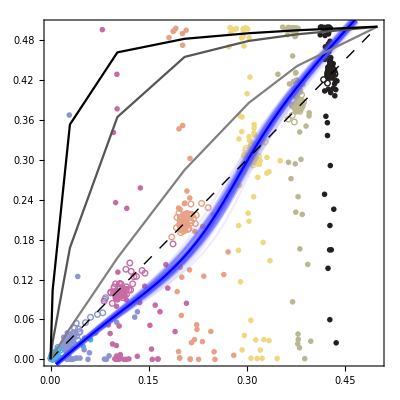

```mathematica
meanPlot[fileE,250]
Export[NotebookDirectory[]<>"Plots/Epi_MeanHet_Rand2.pdf",%,ImageResolution->300];
```

```mathematica
meanData[file_,τ_]:=Flatten[Table[HetCompMtrx2[file,rep,τ][[;;,{1,3}]],{rep,1,7}],1];
```

```mathematica
meanExport[file_,τ_]:=Transpose[Flatten[Join[{Transpose[RollFitOld[0.1,50,meanData[file,τ]]]},Table[Transpose[RollFitOld[0.1,50,Bootstrap[meanData[file,τ],x]]],{x,1,100}]],1]]
```

```mathematica
meanExport[fileE,250]
```

{{0.00344878,-0.00203457,0.00297084,-0.00155663,0.00296952,-0.00155531,0.00252988,188,-0.00164902,0.00335252,-0.00193831,0.00226175,-0.000847537,0.00316267,-0.00174846},48,{1}}
 |  |  |  |

```mathematica
Export[fileE2<>"MeanHet.csv",meanExport[fileE,250]];
```

### Explaining Variation

#### Perturbations

```mathematica
γδPlot[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Transpose[{Table[(δ[file,run]Sum[s[h,t],{h,1,2}]-γ[file,run]Sum[i[h,p,t],{h,1,2},{p,1,2}])/.equEnd/.simPars[file,run,rep],{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervalus"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameLabel->{"γ-δ","ΔH"},ImageSize->Large]
]
```

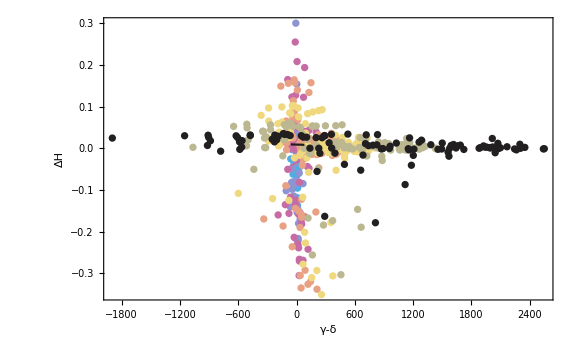

```mathematica
γδPlot[fileE,100]
```

#### λMax

```mathematica
λMaxPlot[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Transpose[{Table[-λMaxRe[simPars[file,run,rep]],{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Table[R2[rep]=lm[data[rep],"RSquared"],{rep,1,7}];
Table[Slope[rep]={lm[data[rep],"BestFitParameters"][[2]],lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]-lm[data[rep],"BestFitParameters"][[2]]},{rep,1,7}];
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
]
```

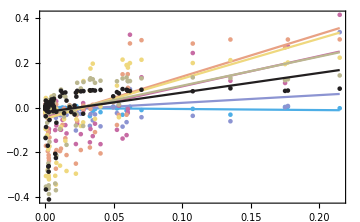

```mathematica
λMaxPlot[fileE,250]
Export[NotebookDirectory[]<>"Plots/Epi_lambda.pdf",%,ImageResolution->300];
```

```mathematica
Table[Join[Round[{R2[rep]},0.01],Round[Slope[rep],0.001]],{rep,1,7}]
Export[NotebookDirectory[]<>"RSquaredTemp.csv",%];
```

{{0.06,-0.048,0.039},{0.1,0.346,0.214},{0.35,1.357,0.37},{0.37,1.893,0.499},{0.28,1.795,0.58},{0.17,1.304,0.569},{0.13,0.879,0.453}}

#### Harmonic Mean Population Size

Does harmonic mean population size at time t explain ΔH at time t

```mathematica
NePlot[file_,τ_]:=Block[{eqTab,data,plot,min,max,lm},
eqTab[rep_]:=Table[Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=Transpose[{(Mean[Transpose[NeMtrx[rep]]]-eqTab[rep])/eqTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*Storing Fit Info*)
FitTab=Table[Flatten[{StandardDeviation[data[rep][[;;,1]]],lm[data[rep],"BestFitParameters"],lm[data[rep],"ParameterConfidenceIntervals"]}],{rep,1,7}];
(*Making Plot*)
Show[Table[plot[rep],{rep,1,7}],Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[lm[data[rep],"RSquared"],0.001]],12,ColorData["CMYKColors"][(rep-1)/6]],Scaled[{0.2,1.2-0.06 rep}]],{rep,5,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,(*FrameLabel->{"Ne-N̂","ΔH"},*)FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

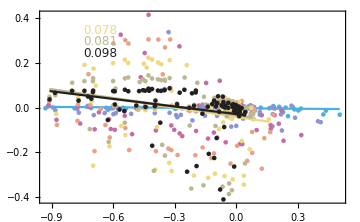

```mathematica
NePlot[fileE,250]
Export[NotebookDirectory[]<>"Plots/Epi_Ne.pdf",%,ImageResolution->300];
```

Does the harmonic mean at time g explain ΔH at time t

```mathematica
NePlot2[file_,τ_,g_]:=Block[{eqTab,data,plot,min,max,lm},
eqTab[rep_]:=Table[Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=Transpose[{(Mean[Transpose[NeMtrx2[rep,g]]]-eqTab[rep])/eqTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y,ConfidenceLevel->.99][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*Storing Fit Info*)
FitTab2[g]=Table[Flatten[{StandardDeviation[data[rep][[;;,1]]],lm[data[rep],"BestFitParameters"],lm[data[rep],"ParameterConfidenceIntervals"],lm[data[rep],"RSquared"]}],{rep,1,7}];
(*Plotting*)
Show[Table[plot[rep],{rep,1,7}],(*Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[lm[data[rep],"RSquared"],0.001]],12,ColorData["CMYKColors"][(rep-1)/6]],Scaled[{0.2,1.2-0.06 rep}]],{rep,5,7}],*)PlotRange->All,AxesOrigin->{0,0},Frame->True,(*FrameLabel->{"Ne-N̂","ΔH"},*)FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

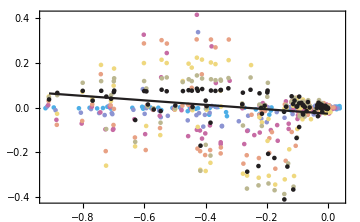

```mathematica
NePlot2[fileE,250,10]
(*Export[NotebookDirectory[]<>"Plots/Epi_Ne_50.pdf",%,ImageResolution->300];*)
```

```mathematica
Round[FitTab2[10],0.001]//MatrixForm
```

(0.257 | -0.001 | 0.005 | -0.004 | 0.001 | -0.003 | 0.012 | 0.026
0.254 | -0.003 | 0.014 | -0.019 | 0.012 | -0.031 | 0.058 | 0.007
0.251 | -0.016 | -0.007 | -0.047 | 0.016 | -0.099 | 0.086 | 0.
0.25 | -0.018 | -0.019 | -0.062 | 0.026 | -0.146 | 0.107 | 0.002
0.248 | -0.037 | -0.091 | -0.084 | 0.01 | -0.228 | 0.045 | 0.03
0.247 | -0.031 | -0.099 | -0.074 | 0.012 | -0.224 | 0.026 | 0.042
0.247 | -0.027 | -0.1 | -0.06 | 0.006 | -0.196 | -0.004 | 0.071)

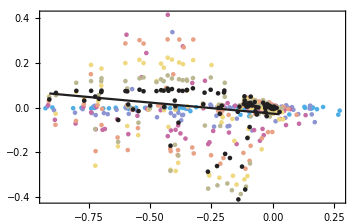

```mathematica
NePlot2[fileE,250,50]
```

```mathematica
Round[FitTab2[50],0.001]//MatrixForm
```

(0.273 | -0.003 | -0.002 | -0.005 | 0. | -0.009 | 0.006 | 0.004
0.268 | -0.007 | -0.003 | -0.021 | 0.007 | -0.045 | 0.04 | 0.
0.264 | -0.019 | -0.025 | -0.048 | 0.01 | -0.113 | 0.063 | 0.006
0.259 | -0.021 | -0.035 | -0.062 | 0.02 | -0.157 | 0.087 | 0.006
0.255 | -0.037 | -0.097 | -0.083 | 0.009 | -0.23 | 0.036 | 0.036
0.251 | -0.031 | -0.101 | -0.073 | 0.012 | -0.224 | 0.022 | 0.045
0.249 | -0.027 | -0.099 | -0.06 | 0.006 | -0.195 | -0.004 | 0.071)

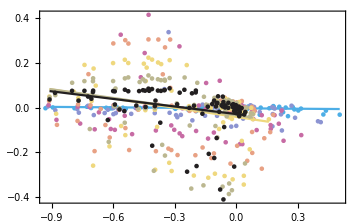

```mathematica
NePlot2[fileE,250,250]
(*Export[NotebookDirectory[]<>"Plots/Epi_Ne_50.pdf",%,ImageResolution->300];*)
```

```mathematica
Round[FitTab2[250],0.001]//MatrixForm
```

(0.293 | -0.003 | -0.007 | -0.005 | -0.002 | -0.012 | -0.002 | 0.07
0.278 | -0.009 | -0.018 | -0.018 | 0.001 | -0.048 | 0.013 | 0.013
0.271 | -0.021 | -0.051 | -0.041 | -0.002 | -0.115 | 0.013 | 0.025
0.268 | -0.028 | -0.084 | -0.056 | 0. | -0.171 | 0.004 | 0.035
0.266 | -0.042 | -0.137 | -0.073 | -0.011 | -0.231 | -0.043 | 0.078
0.262 | -0.035 | -0.129 | -0.064 | -0.005 | -0.217 | -0.042 | 0.081
0.256 | -0.029 | -0.113 | -0.052 | -0.006 | -0.182 | -0.044 | 0.098)

Does the effective population size at generation g explain ΔH at generation g?

```mathematica
NePlot3[file_,g_]:=Block[{eqTab,data,plot,min,max,lm},
eqTab[rep_]:=Table[Sum[s[h,t],{h,1,2}]+Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=Transpose[{(Mean[Transpose[NeMtrx2[rep,g]]]-eqTab[rep])/eqTab[rep],HetCompMtrx2[file,rep,g][[;;,3]]-HetCompMtrx2[file,rep,g][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=lm[data,x]=LinearModelFit[data,y,y,ConfidenceLevel->.99][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*Storing Fit Info*)
FitTab3[g]=Table[Flatten[{StandardDeviation[data[rep][[;;,1]]],lm[data[rep],"BestFitParameters"],lm[data[rep],"ParameterConfidenceIntervals"],lm[data[rep],"RSquared"]}],{rep,1,7}];
(*Plotting*)
Show[Table[plot[rep],{rep,1,7}],(*Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[lm[data[rep],"RSquared"],0.001]],12,ColorData["CMYKColors"][(rep-1)/6]],Scaled[{0.2,1.2-0.06 rep}]],{rep,5,7}],*)PlotRange->All,AxesOrigin->{0,0},Frame->True,(*FrameLabel->{"Ne-N̂","ΔH"},*)FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

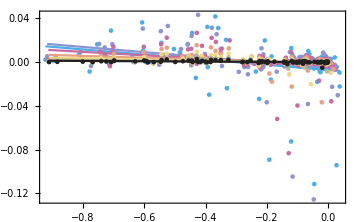

```mathematica
NePlot3[fileE,10]
```

```mathematica
FitTab3[10]
```

{{0.257202,-0.00707219,-0.0233991,-0.0145238,0.000379428,-0.0453106,-0.00148755,0.0743324},{0.254466,-0.0052207,-0.0238961,-0.0121412,0.00169978,-0.0440967,-0.00369552,0.0896981},{0.251415,-0.00313392,-0.0156784,-0.00772954,0.0014617,-0.0290511,-0.00230582,0.088251},{0.249679,-0.00111272,-0.00855509,-0.00328114,0.00105571,-0.0148576,-0.00225254,0.114844},{0.248132,-0.000499928,-0.00506269,-0.00170322,0.000703363,-0.00855956,-0.00156582,0.128613},{0.247361,-0.000137972,-0.00271686,-0.000733294,0.00045735,-0.00444694,-0.000986788,0.147958},{0.246807,-0.0000533812,-0.00148426,-0.000370877,0.000264115,-0.00240692,-0.000561612,0.15414}}

#### Relative Turnover rate

```mathematica
turnoverPlot[file_,τ_]:=Block[{δTab,γTab,βTab,data,plot,min,max,lm},
δTab[rep_]:=Table[δ Sum[s[h,t],{h,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
γTab[rep_]:=Table[γ Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
βTab[rep_]:=Table[Sum[β[h,p]s[h,t]i[k,p,t],{h,1,2},{p,1,2},{k,1,2}]/.equEnd/.βSub/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=data[rep]=Transpose[{δTab[rep]-γTab[rep]-βTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
(*lm[data_,x_]:=lm[data,x]=NonlinearModelFit[data,{y0+-L/(1+Exp[k(y-x0)]),0<L,0<k},{y0,L,k,x0},y][x];*)
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*plot[rep_]:=Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]];*)
Show[Table[plot[rep],{rep,1,7}],(*Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[lm[data[rep],"RSquared"],0.001]],12,ColorData["CMYKColors"][(rep-1)/6]],Scaled[{0.2,1.2-0.06 rep}]],{rep,5,7}],*)PlotRange->All,AxesOrigin->{0,0},Frame->True,(*FrameLabel->{"Ne-N̂","ΔH"},*)FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

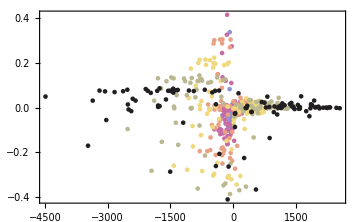

```mathematica
turnoverPlot[fileE,250]
```

```mathematica
turnoverPlot2[file_,τ_]:=Block[{δTab,γTab,βTab,data,plot,min,max,lm},
δTab[rep_]:=Table[δ Sum[s[h,t],{h,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
γTab[rep_]:=Table[γ Sum[i[h,p,t],{h,1,2},{p,1,2}]/.equEnd/.simPars[file,run,rep],{run,1,100}];
βTab[rep_]:=Table[Sum[β[h,p]s[h,t]i[k,p,t],{h,1,2},{p,1,2},{k,1,2}]/.equEnd/.βSub/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=data[rep]=Transpose[{δTab[rep]-γTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
(*lm[data_,x_]:=lm[data,x]=NonlinearModelFit[data,y0+-L/(1+Exp[k(y-x0)]),{y0,0<L,0<k,x0},y][x];*)
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Show[Table[plot[rep],{rep,1,7}],(*Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[lm[data[rep],"RSquared"],0.001]],12,ColorData["CMYKColors"][(rep-1)/6]],Scaled[{0.2,1.2-0.06 rep}]],{rep,5,7}],*)PlotRange->All,AxesOrigin->{0,0},Frame->True,(*FrameLabel->{"Ne-N̂","ΔH"},*)FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

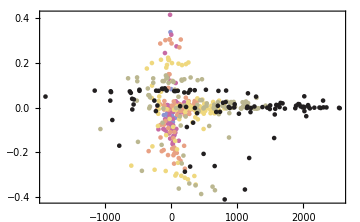

```mathematica
turnoverPlot2[fileE,250]
```

## Allele Frequency Dynamics

```mathematica
Clear[smallest,largest]
```

```mathematica
(*The really small element of rep=3*)
smallest[rep_]:=Ordering[HetCompMtrx2[fileE,rep,250][[;;,3]],1]
```

```mathematica
largest[4]
```

{72}

```mathematica
(*The really high element of rep=3*)
largest[rep_]:=Ordering[HetCompMtrx2[fileE,rep,250][[;;,3]],-1]
```

```mathematica
AFPlot[file_,run_,rep_,nd_]:=Block[{h1,h2,p1,p2,coev,dirSel,fixed,extinct,all},
{h1,h2,p1,p2}={SparseArray[Total[state[file,run,rep][[{1,3,4},1;;nd,;;]]]],SparseArray[Total[state[file,run,rep][[{2,5,6},1;;nd,;;]]]],SparseArray[Total[state[file,run,rep][[{3,5},1;;nd,;;]]]],SparseArray[Total[state[file,run,rep][[{4,6},1;;nd,;;]]]]};
all=Flatten[Table[{deme,g},{deme,1,nd},{g,1,250}],1];
coev=Intersection[h1["NonzeroPositions"],h2["NonzeroPositions"],p1["NonzeroPositions"],p2["NonzeroPositions"]];
fixed=Union[Complement[all,h1["NonzeroPositions"]],Complement[all,h2["NonzeroPositions"]]];
extinct=Complement[Intersection[Complement[all,p1["NonzeroPositions"]],Complement[all,p2["NonzeroPositions"]]],fixed];
dirSel=Complement[Union[Complement[p1["NonzeroPositions"],p2["NonzeroPositions"]],Complement[p2["NonzeroPositions"],p1["NonzeroPositions"]]],Union[fixed,extinct]];
coev=Table[Select[coev,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];dirSel=Table[Select[dirSel,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];fixed=Table[Select[fixed,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];
extinct=Table[Select[extinct,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];

Show[ListLinePlot[Table[pHMtrx[file,run,rep][[d,coev[[d]]]],{d,1,nd}],PlotStyle->Directive[Gray,Opacity[0.2]]],ListLinePlot[Table[If[Length[dirSel[[d]]]>0,Transpose[{dirSel[[d]],pHMtrx[file,run,rep][[d,dirSel[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Red,Opacity[0.3]]],ListLinePlot[Table[If[Length[extinct[[d]]]>0,Transpose[{extinct[[d]],pHMtrx[file,run,rep][[d,extinct[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Green,Opacity[0.3]]],ListLinePlot[Table[If[Length[fixed[[d]]]>0,Transpose[{fixed[[d]],pHMtrx[file,run,rep][[d,fixed[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Blue,Opacity[0.2]]],Epilog->Text[Style["λ_Max="<>ToString[Round[λMaxRe[simPars[file,run,rep]],0.001]],14,Black],Scaled[{0.8,0.8}]],PlotRange->{0,1},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]
]
```

```mathematica
Clear[h1,h2,p1,p2]
```

```mathematica
smallest[4]
```

{1}

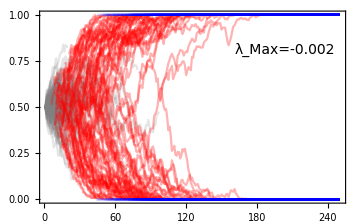

```mathematica
AFPlot[fileE,1,4,100]
Export[NotebookDirectory[]<>"Plots/Epi_AF_1.pdf",%,ImageResolution->300];
```

```mathematica
largest[4]
```

{72}

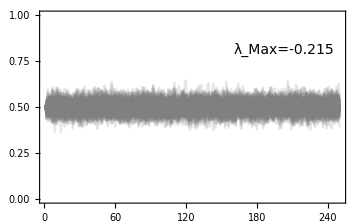

```mathematica
AFPlot[fileE,72,4,100]
Export[NotebookDirectory[]<>"Plots/Epi_AF_2.pdf",%,ImageResolution->300];
```

## Fixation Order

```mathematica
Clear[hpState]
hpState[file_,run_,rep_]:=hpState[file,run,rep]={Total[state[file,run,rep][[{1,3,4}]]],Total[state[file,run,rep][[{2,5,6}]]],Total[state[file,run,rep][[{3,5}]]],Total[state[file,run,rep][[{4,6}]]]}
```

```mathematica
hostFixTime[file_,run_,rep_]:=Table[FirstPosition[hpState[file,run,rep][[{1,2},d,;;]],0.],{d,1,1000}]
```

```mathematica
pathFixTime[file_,run_,rep_]:=Table[FirstPosition[hpState[file,run,rep][[{3,4},d,;;]],0.],{d,1,1000}]
```

```mathematica
pathExtinctTime[file_,run_,rep_]:=Table[FirstPosition[Total[hpState[file,run,rep][[{3,4},d,;;]]],0.],{d,1,1000}]
```

```mathematica
Clear[fixOrder]
fixOrder[file_,rep_]:=fixOrder[file,rep]=Block[{temp1,temp2,temp3,temp4,temp5,run,out},out={};
For[run=1,run≤100,run++,
(*All Data Points*)
temp1=Transpose[{hostFixTime[file,run,rep],pathFixTime[file,run,rep],pathExtinctTime[file,run,rep]}];
(*Host Fixed*)
temp2=DeleteCases[temp1,_?(#[[1]]==Missing["NotFound"]&)];
(*Host Fixed and Pathogen Fixed*)
temp3=DeleteCases[temp2,_?(#[[2]]==Missing["NotFound"]&)];
(*Pathogen Fixed (Pathogen may have gone extict) then Host fixed*)
temp4=Select[temp3,#[[1,2]]>#[[2,2]]&];
(*Pathogen Fixed, Pathogen Extinct, then Host fixed*)
temp5=Select[temp4,#[[1,2]]>#[[3,1]]&];
AppendTo[out,{Length[temp1]-Length[temp2](*Host Polymorphic*),Length[temp2]-Length[temp3](*Host Fixed, Pathogen Polymorphic*),Length[temp3]-Length[temp4](*Host Fixed First*),Length[temp4]-Length[temp5](*Pathogen Fixed then Host Fixed*),Length[temp5](*Pathogen Fixed then Pathogen Extinct, then Host Fixed*)}];
];
out/nRuns
]
```

```mathematica
fixBarChart[file_,rep_,τ_]:=BarChart[fixOrder[file,rep][[Ordering[HetCompMtrx2[file,rep,τ][[;;,3]]]]],ChartLayout->"Stacked",ChartStyle->{Gray,Blue,Blue,Red,Green},Frame->True,FrameTicks->{{True,False},{True,False}},ImageSize->Medium,FrameTicksStyle->Directive[Black,14]]
```

Gray= Host and pathogen polymorphic at generation 250
Blue= Host fixed before pathogen
Red= Pathogen  fixes then host fixes
Green= Pathogen fixes, pathogen goes extinct, then host fixes
Runs (bars) are ordered in terms of increasing heterozygosity

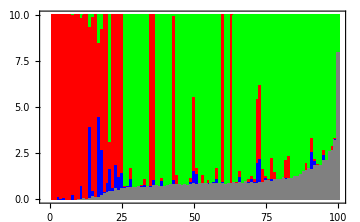

/Users/ailenemacpherson/Desktop/EcoEpiDrift/Plots/Epi_DirSel_Rand.pdf

```mathematica
(*GraphicsRow[{fixBarChart[fileE,2,250],fixBarChart[fileE,4,250]}]*)
fixBarChart[fileE,2,250]
Export[NotebookDirectory[]<>"Plots/Epi_DirSel_Rand.pdf",%,ImageResolution-> 300]
```

Model Comparison

```mathematica
constModel=Import["/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/const_11_20_2/MeanHet.csv"];
ecoModel=Import["/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/eco_11_6/MeanHet.csv"];
epiModel=Import["/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/epi_11_6/MeanHet.csv"];
```

```mathematica
constModel2[i_]:=constModel[[;;,{2i-1,2i}]]
ecoModel2[i_]:=ecoModel[[;;,{2i-1,2i}]]
epiModel2[i_]:=epiModel[[;;,{2i-1,2i}]]
```

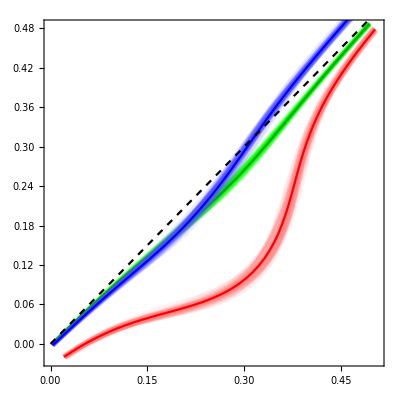

```mathematica
Show[ListLinePlot[Table[constModel2[i],{i,2,100}],PlotStyle->Directive[Pink,Opacity[0.1]]],
ListLinePlot[constModel2[1],PlotStyle->Red],ListLinePlot[Table[ecoModel2[i],{i,2,100}],PlotStyle->Directive[Green,Opacity[0.1]]],
ListLinePlot[ecoModel2[1],PlotStyle->Darker[Green]],ListLinePlot[Table[epiModel2[i],{i,2,100}],PlotStyle->Directive[Lighter[Blue],Opacity[0.1]]],
ListLinePlot[epiModel2[1],PlotStyle->Blue],
Plot[x,{x,0,0.5},PlotStyle->{Black,Dashed}],AspectRatio->1,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,14],Axes->False]
Export[NotebookDirectory[]<>"Plots/ModelComparison.pdf",%,ImageResolution->300];
```